# Semi Inclusive Deep Inelastic Scattering in Wandzura-Wilczek-type approximations. Based on paper: “Semi-Inclusive Deep Inelastic Scattering in Wandzura-Wilczek-type approximation” S. Bastami, H. Avakian, A. V. Efremov, A. Kotzinian, B. U. Musch, T. O’Connell, B. Parsamyan, A. Prokudin, M. Schlegel, P. Schweitzer, W. Vogelsang author: Alexei Prokudin email: prokudin@jlab.org

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/avp5627/GIT/TMD-SIDIS-WW/mathematica

```mathematica
<<ErrorBarLogPlots`
```

## Collinear functions

## Read and interpolate DSS collinear fragmentation functions.

```mathematica
DSShplus= ReadList["fragmentationpiplus.dat",Real,RecordLists-> True];
DSShminus= ReadList["fragmentationpiminus.dat",Real,RecordLists-> True];
```

```mathematica
uhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,3]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}]
dhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,4]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
shplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,5]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
ubhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,6]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
dbhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,7]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
sbhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,8]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
```

InterpolatingFunction[{{0.0001, 0.989902}, {1., 89.11}}, <>]

```mathematica
uhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,3]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}]
dhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,4]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
shminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,5]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
ubhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,6]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
dbhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,7]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
sbhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,8]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
```

InterpolatingFunction[{{0.0001, 0.989902}, {1., 89.11}}, <>]

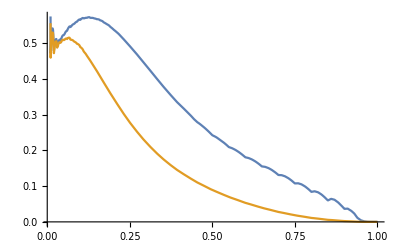

```mathematica
Plot[{z uhplus[z,3.],z dhplus[z,3.]},{z,0.01,1}]
```

## Read and interpolate MSTW collinear distribution functions.

```mathematica
<<mstwpdf.m
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

```mathematica
?ReadPDFGrid
```

The function ReadPDFGrid[prefix,ih] reads the PDF grid corresponding to eigenvector set ih, where ih=0 is the central set, into memory from the location specified by prefix.

```mathematica
?xf
```

The function xf[ih,x,q,f] returns x times the parton distribution of flavour f corresponding to eigenvector set ih, where ih=0 is the central set, at a given momentum fraction x and scale q in GeV.  Note that ih and f must be integers, and x and q must be numeric quantities.  The PDG convention is used for the flavour f (apart from the gluon has f=0, not 21), that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t.  The valence quark distributions can also be obtained directly with f = 7, 8, 9, 10, 11, 12 corresponding to dv, uv, sv, cv, bv, tv.  The photon distribution is obtained with f = 13.

```mathematica
Use of the central PDF set
```

central of PDF set the Use

```mathematica
prefix="Grids/mstw2008lo";
Timing[ReadPDFGrid[prefix,0]]
```

PDF grid read from Grids/mstw2008lo.00.dat

{5.69658,Null}

```mathematica
Clear[upv,dnv,usea,dsea,str,sbar];
```

```mathematica
upv[x_,Q2_]:=xf[0,x,Sqrt[Q2],8]/x
dnv[x_,Q2_]:=xf[0,x,Sqrt[Q2],7]/x
usea[x_,Q2_]:=xf[0,x,Sqrt[Q2],-2]/x
dsea[x_,Q2_]:=xf[0,x,Sqrt[Q2],-1]/x
str[x_,Q2_]:=xf[0,x,Sqrt[Q2],3]/x
sbar[x_,Q2_]:=xf[0,x,Sqrt[Q2],-3]/x
up[x_,Q2_]:=upv[x,Sqrt[Q2]]+usea[x,Sqrt[Q2]]
dn[x_,Q2_]:=dnv[x,Sqrt[Q2]]+dsea[x,Sqrt[Q2]]
upbar[x_,Q2_]:=usea[x,Sqrt[Q2]]
dnbar[x_,Q2_]:=dsea[x,Sqrt[Q2]]
```

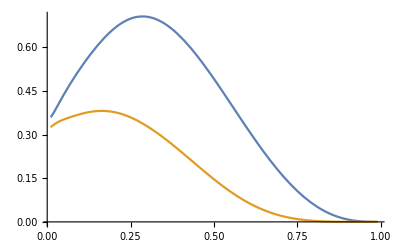

```mathematica
Plot[{x up[x,1.],x dn[x,1.]},{x,0.01,0.99}]
```

## Read and interpolate helicity collinear distribution functions. Gluck:1998xa

```mathematica
g1param= ReadList["g1.dat",Real,RecordLists-> True];
```

```mathematica
g1u=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,3]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
g1d=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,4]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
g1s=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,5]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
g1ubar=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,6]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
g1dbar=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,7]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
g1sbar=Interpolation[Table[{{g1param[[i,1]],g1param[[i,2]]},g1param[[i,8]]},{i,1,Length[g1param]}],InterpolationOrder->{3,3}];
```

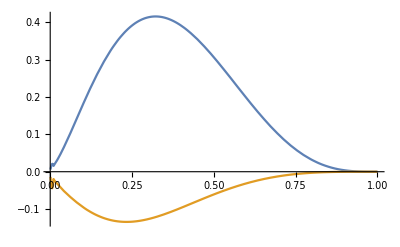

```mathematica
Plot[{x*g1u[x,1.],x*g1d[x,1.]},{x,0.001,1}]
```

## Read and interpolate pion collinear distribution functions.

```mathematica
pion= ReadList["pion_mrss.dat",Real,RecordLists-> True];
```

```mathematica
pionu=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,3]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
piond=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,4]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
pions=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,5]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
pionubar=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,6]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
piondbar=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,7]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
pionsbar=Interpolation[Table[{{pion[[i,1]],pion[[i,2]]},pion[[i,8]]},{i,1,Length[pion]}],InterpolationOrder->{3,3}];
```

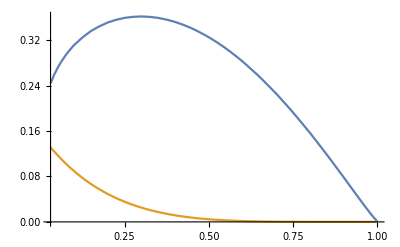

```mathematica
Plot[{x*pionu[x,1.],x*piond[x,1.]},{x,0.03,1}]
```

## Read and interpolate Soffer Bound collinear distribution functions.

```mathematica
sb= ReadList["SofferBound.dat",Real,RecordLists-> True];
```

```mathematica
sb1u=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,3]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1d=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,4]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1s=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,5]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1ubar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,6]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1dbar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,7]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1sbar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,8]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
```

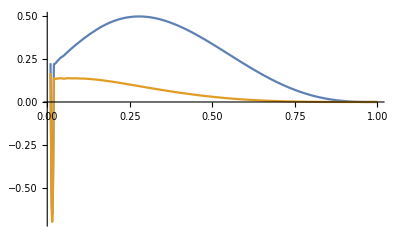

```mathematica
Plot[{x*sb1u[x,1.],x*sb1d[x,1.]},{x,0.01,1}]
```

## 8 “basis” functions f_1, D_1, h_1, g_1, H_1^⊥, f_(1T)^⊥,h_(1T)^⊥, h_1^⊥

## f_1

```mathematica
(*2005 fit*)
Clear[avk];
avk=0.25;
(* distribution*)


f1u[x_,Q2_ ]:= up[x,Q2];
f1d[x_,Q2_ ]:= dn[x,Q2] ;
f1ubar[x_,Q2_ ]:= upbar[x,Q2];  
f1dbar[x_,Q2_ ]:= dnbar[x,Q2] ; 
f1s[x_,Q2_ ]:= str[x,Q2];
f1sdbar[x_,Q2_ ]:= sbar[x,Q2];


f1uTMD[x_,Q2_ ,kt_]:= up[x,Q2]1/(π avk) Exp[-kt^2/avk];
f1dTMD[x_,Q2_,kt_ ]:= dn[x,Q2] 1/(π avk) Exp[-kt^2/avk];
f1ubarTMD[x_,Q2_,kt_ ]:= upbar[x,Q2]  1/(π avk) Exp[-kt^2/avk];
f1dbarTMD[x_,Q2_ ,kt_]:= dnbar[x,Q2]  1/(π avk) Exp[-kt^2/avk];
f1sTMD[x_,Q2_,kt_ ]:= str[x,Q2]1/(π avk) Exp[-kt^2/avk];
f1sdbarTMD[x_,Q2_,kt_ ]:= sbar[x,Q2]1/(π avk) Exp[-kt^2/avk];
```

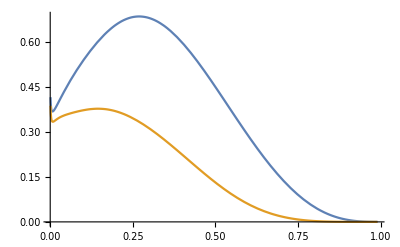

```mathematica
Plot[{x f1u[x,1.7], x f1d[x,1.7]},{x,0.001,0.99}]
```

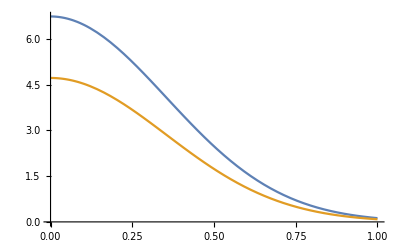

```mathematica
Plot[{f1uTMD[0.1,1.,kt],f1dTMD[0.1,1.,kt]},{kt,0,1}]
```

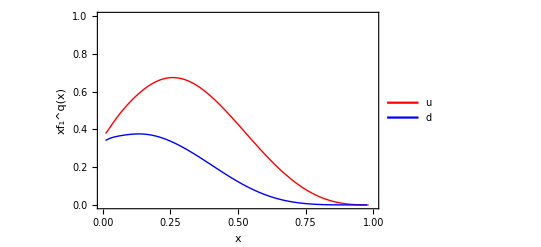

```mathematica
f1plot =Plot[{x f1u[x,2.4],x f1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xf_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/f1.pdf",%,Background->None]
```

../tex/figs/f1.pdf

```mathematica
ExpandFileName["../tex/figs/f1.pdf"]
```

/Users/avp5627/GIT/TMD-SIDIS-WW/tex/figs/f1.pdf

```mathematica
ExpandFileName["/Users/avp5627/GIT/TMD-SIDIS-WW/tex/figs/f1.pdf"]
```

/Users/avp5627/GIT/TMD-SIDIS-WW/tex/figs/f1.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/Users/avp5627/GIT/TMD-SIDIS-WW/tex/figs/f1.pdf"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["../tex/figs/f1.pdf"]]]
```

## D_1

```mathematica
(*2005 fit*)
Clear[avp];
avp=0.2;
(* fragmentation*)
D1uTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",uhplus[z,Q2],If[pion == "pi-",uhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1dTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",dhplus[z,Q2],If[pion == "pi-",dhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1ubarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",ubhplus[z,Q2],If[pion == "pi-",ubhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1dbarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",dbhplus[z,Q2],If[pion == "pi-",dbhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1sTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",shplus[z,Q2],If[pion == "pi-",shminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1sbarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",sbhplus[z,Q2],If[pion == "pi-",sbhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]


D1u[pion_,z_,Q2_ ]:= If[pion == "pi+",uhplus[z,Q2],If[pion == "pi-",uhminus[z,Q2]]]  
D1d[pion_,z_,Q2_ ]:= If[pion == "pi+",dhplus[z,Q2],If[pion == "pi-",dhminus[z,Q2]]]  
D1ubar[pion_,z_,Q2_ ]:= If[pion == "pi+",ubhplus[z,Q2],If[pion == "pi-",ubhminus[z,Q2]]]  
D1dbar[pion_,z_,Q2_ ]:= If[pion == "pi+",dbhplus[z,Q2],If[pion == "pi-",dbhminus[z,Q2]]]  
D1s[pion_,z_,Q2_ ]:= If[pion == "pi+",shplus[z,Q2],If[pion == "pi-",shminus[z,Q2]]]  
D1sbar[pion_,z_,Q2_ ]:= If[pion == "pi+",sbhplus[z,Q2],If[pion == "pi-",sbhminus[z,Q2]]]
```

InterpolatingFunction::dmval: Input value {0.0000204286,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

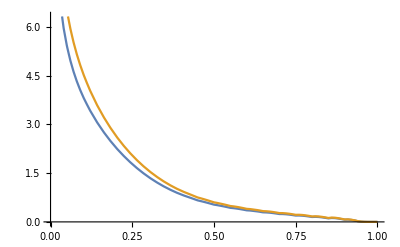

```mathematica
Plot[{D1u["pi+",z,1.],D1d["pi-",z,1.]},{z,0,1}]
```

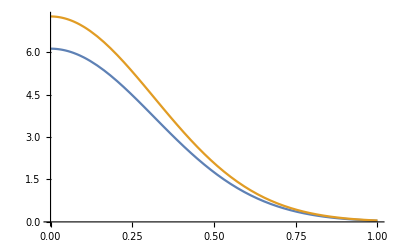

```mathematica
Plot[{D1uTMD["pi+",0.1,1.,pt],D1dTMD["pi-",0.1,1.,pt]},{pt,0,1}]
```

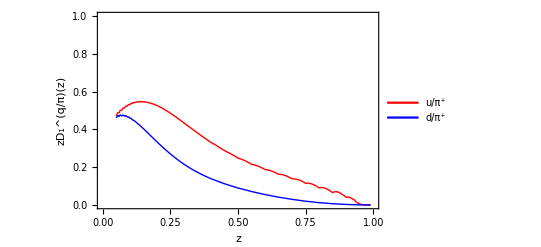

```mathematica
D1plot =Plot[{x D1u["pi+",x,2.4],x D1d["pi+",x,2.4]},{x,0.05,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"z","zD_1^(q/π)(z)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u/π^+","d/π^+"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/D1.pdf",%,Background->None]
```

../tex/figs/D1.pdf

## D_1 (with removed interpolation bug in DSSV package) (for Fig.3)

```mathematica
zD1uINTERPOLATED=Interpolation[Join[Table[{x,x D1u["pi+",x,2.4]},{x,0.05,0.90,0.05}],{{1.0,0.0}}]];
zD1dINTERPOLATED=Interpolation[Join[Table[{x,x D1d["pi+",x,2.4]},{x,0.05,0.90,0.05}],{{1.0,0.0}}]];
```

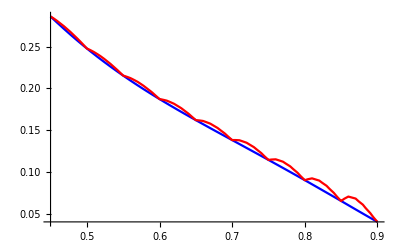

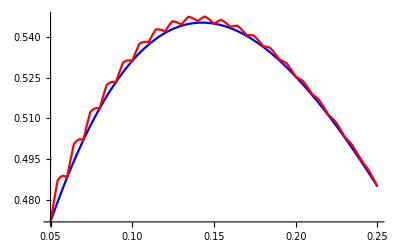

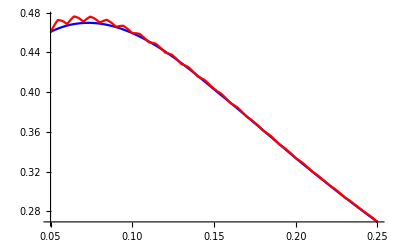

```mathematica
Plot[{zD1uINTERPOLATED[z],z D1u["pi+",z,2.4]},{z,0.45,0.9},PlotStyle->{Blue,Red}]
Plot[{zD1uINTERPOLATED[z],z D1u["pi+",z,2.4]},{z,0.05,0.25},PlotStyle->{Blue,Red}]
Plot[{zD1dINTERPOLATED[z],z D1d["pi+",z,2.4]},{z,0.05,0.25},PlotStyle->{Blue,Red}]
```

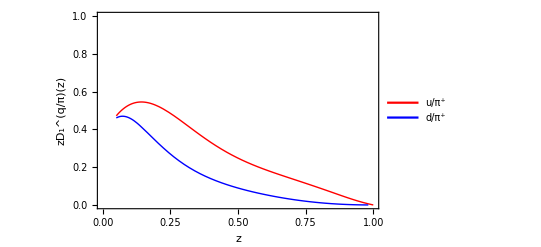

```mathematica
D1plot =Plot[{zD1uINTERPOLATED[x],zD1dINTERPOLATED[x]},{x,0.05,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"z","zD_1^(q/π)(z)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u/π^+","d/π^+"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/D1.pdf",%,Background->None]
```

../tex/figs/D1.pdf

## h_1

```mathematica
(*2013 fit*)
Clear[NuT,NdT,alphaT,betaT];
NuT=0.46;
NdT=-1.000;
alphaT=1.11;
betaT=3.64;

(* Transversity function with DGLAP Evolution*)
h1u[x_,Q2_]:=(NuT x^alphaT (1-x)^betaT(alphaT+ betaT)^(alphaT+ betaT)/((alphaT^alphaT)( betaT^betaT))) sb1u[x,Q2];
h1d[x_,Q2_]:=(NdT x^alphaT (1-x)^betaT (alphaT+ betaT)^(alphaT+ betaT)/((alphaT^alphaT)( betaT^betaT)))sb1d[x,Q2];

h1uTMD[x_,Q2_,kt_]:=h1u[x,Q2]1/(π avk) Exp[-kt^2/avk];
h1dTMD[x_,Q2_,kt_]:=h1d[x,Q2]1/(π avk) Exp[-kt^2/avk];


year = 2013;
width = 25;
MyLabel= StringForm["`` fit ⟨k_⊥^2⟩ = 0.`` (GeV^2).",year,width]
```

2013 fit ⟨k_⊥^2⟩ = 0.25 (GeV^2).

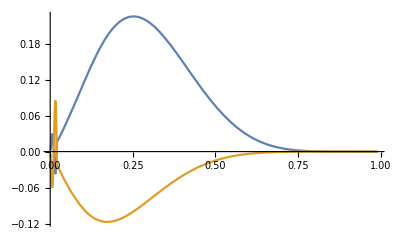

```mathematica
Plot[{x h1u[x,1.], x h1d[x,1.]},{x,0.001,0.99}]
```

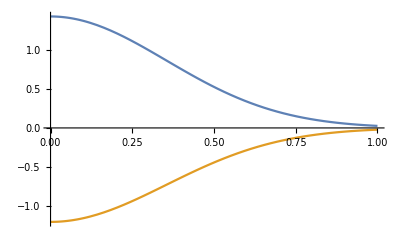

```mathematica
Plot[{h1uTMD[0.1,1.,kt],h1dTMD[0.1,1.,kt]},{kt,0,1}]
```

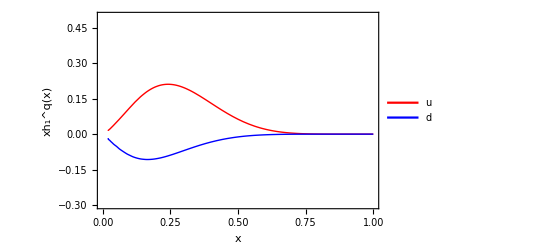

```mathematica
h1plot =Plot[{x h1u[x,2.4],x h1d[x,2.4]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.3,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xh_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/h1.pdf",%,Background->None]
```

../tex/figs/h1.pdf

## g_1

```mathematica
(*Lattice fit*)
Clear[avkg];
avkg=avk 0.76 ;
 

(* Helicity functions with DGLAP Evolution*)


g1uTMD[x_,Q2_,kt_]:=g1u[x,Q2]1/(π avkg) Exp[-kt^2/avkg];
g1dTMD[x_,Q2_,kt_]:=g1d[x,Q2]1/(π avkg) Exp[-kt^2/avkg];
```

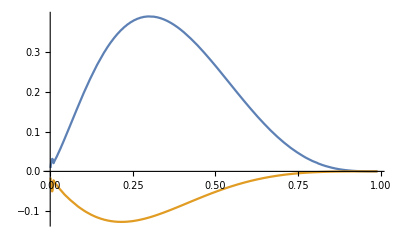

```mathematica
Plot[{x g1u[x,1.7], x g1d[x,1.7]},{x,0.001,0.99}]
```

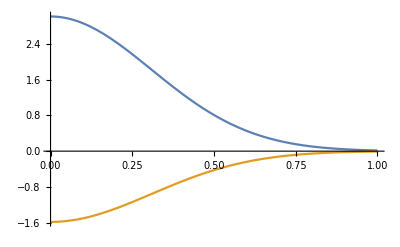

```mathematica
Plot[{g1uTMD[0.1,1.,kt],g1dTMD[0.1,1.,kt]},{kt,0,1}]
```

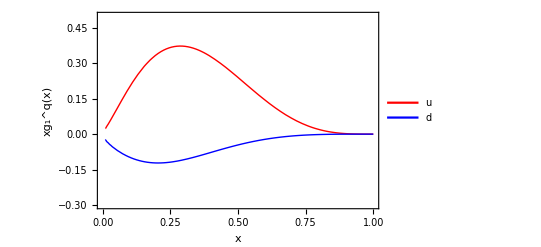

```mathematica
g1plot =Plot[{x g1u[x,2.4],x g1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.3,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xg_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/g1.pdf",%,Background->None]
```

../tex/figs/g1.pdf

## H_1^⊥

```mathematica
(*2013 fit*)
Clear[MC,NCfav,NCunf,alphaC,betaC, Mh];
MC=Sqrt[1.5];
NCfav=0.49;
NCunf=-1.000;
alphaC=1.06;
betaC=0.07;
Mh = 0.135;

(*Collins function with DGLAP Evolution*)
H1perpFavHalfMoment[x_,Q2_]:=√(2 ⅇ)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC))) D1u["pi+",x,Q2]/4 √((π avp)/((MC^2+avp)^3));
H1perpUnfHalfMoment[x_,Q2_]:=√(2 ⅇ)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1d["pi+",x,Q2]/4 √((π avp)/((MC^2+avp)^3));

H1perpFavFirstMoment[x_,Q2_]:=√(ⅇ/2)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC))) D1u["pi+",x,Q2] (MC^3 avp)/(Mh x(MC^2+avp)^2);
H1perpUnfFirstMoment[x_,Q2_]:=√(ⅇ/2)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1d["pi+",x,Q2] (MC^3 avp)/(Mh x(MC^2+avp)^2);

H1perpFavTMD[x_,Q2_,kt_]:=(x Mh)/MC Exp[-kt^2/MC^2] √(2 ⅇ)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1u["pi+",x,Q2]1/(π avp) Exp[-kt^2/avp];
H1perpUnfTMD[x_,Q2_,kt_]:=(x Mh)/MC Exp[-kt^2/MC^2] √(2 ⅇ)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1d["pi+",x,Q2]1/(π avp) Exp[-kt^2/avp];


year = 2013;
width = 2;
MyLabel= StringForm["`` fit ⟨p_⊥^2⟩ = 0.`` (GeV^2).",year,width]

H1perpFirstMoment[quark_,pion_,x_,Q2_] := If[(quark == "u" && pion == "pi+") || (quark == "bard" && pion == "pi+") || (quark == "d" && pion == "pi-") || (quark == "baru" && pion == "pi-"),H1perpFavFirstMoment[x,Q2],H1perpUnfFirstMoment[x,Q2]]
```

2013 fit ⟨p_⊥^2⟩ = 0.2 (GeV^2).

InterpolatingFunction::dmval: Input value {0.0000204286,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

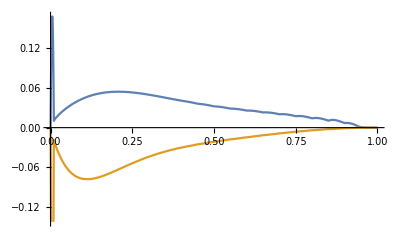

```mathematica
Plot[{H1perpFavHalfMoment[z,1.],H1perpUnfHalfMoment[z,1.]},{z,0,1}]
```

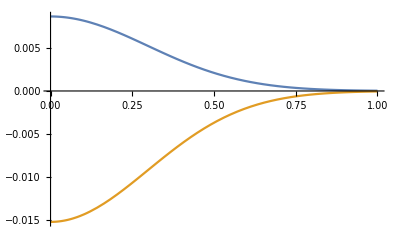

```mathematica
Plot[{H1perpFavTMD[0.1,1.,pt],H1perpUnfTMD[0.1,1.,pt]},{pt,0,1}]
```

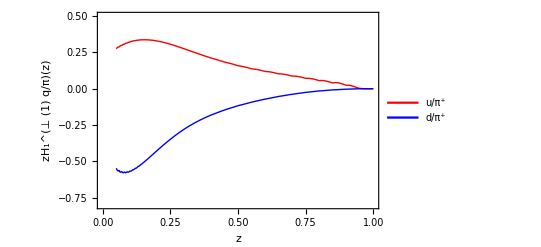

```mathematica
H1perpplot =Plot[{x H1perpFavFirstMoment[x,2.4],x H1perpUnfFirstMoment[x,2.4]},{x,0.05,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.8,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"z","zH_1^(⊥ (1) q/π)(z)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u/π^+","d/π^+"},{0.7,0.3}]]
```

```mathematica
Export["../tex/figs/H1perp.pdf",%,Background->None]
```

../tex/figs/H1perp.pdf

## H_1^⊥(with removed interpolation bug in D_1^q(z) , see above) (for Fig.3)

```mathematica
(*2013 fit*)
Clear[MC,NCfav,NCunf,alphaC,betaC, Mh];
MC=Sqrt[1.5];
NCfav=0.49;
NCunf=-1.000;
alphaC=1.06;
betaC=0.07;
Mh = 0.135;

(*Collins function with DGLAP Evolution  ONLY FOR Q2=2.4 GeV2*)
H1perpFavHalfMoment[x_,Q2_]:=√(2 ⅇ)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC))) (zD1uINTERPOLATED[x]/x)/4 √((π avp)/((MC^2+avp)^3));
H1perpUnfHalfMoment[x_,Q2_]:=√(2 ⅇ)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))(zD1dINTERPOLATED[x]/x)/4 √((π avp)/((MC^2+avp)^3));

H1perpFavFirstMoment[x_,Q2_]:=√(ⅇ/2)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC))) (zD1uINTERPOLATED[x]/x) (MC^3 avp)/(Mh x(MC^2+avp)^2);
H1perpUnfFirstMoment[x_,Q2_]:=√(ⅇ/2)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))(zD1dINTERPOLATED[x]/x) (MC^3 avp)/(Mh x(MC^2+avp)^2);

H1perpFavTMD[x_,Q2_,kt_]:=(x Mh)/MC Exp[-kt^2/MC^2] √(2 ⅇ)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))(zD1uINTERPOLATED[x]/x)1/(π avp) Exp[-kt^2/avp];
H1perpUnfTMD[x_,Q2_,kt_]:=(x Mh)/MC Exp[-kt^2/MC^2] √(2 ⅇ)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))(zD1uINTERPOLATED[x]/x) 1/(π avp) Exp[-kt^2/avp];


year = 2013;
width = 2;
MyLabel= StringForm["`` fit ⟨p_⊥^2⟩ = 0.`` (GeV^2).",year,width]

H1perpFirstMoment[quark_,pion_,x_,Q2_] := If[(quark == "u" && pion == "pi+") || (quark == "bard" && pion == "pi+") || (quark == "d" && pion == "pi-") || (quark == "baru" && pion == "pi-"),H1perpFavFirstMoment[x,Q2],H1perpUnfFirstMoment[x,Q2]]
```

2013 fit ⟨p_⊥^2⟩ = 0.2 (GeV^2).

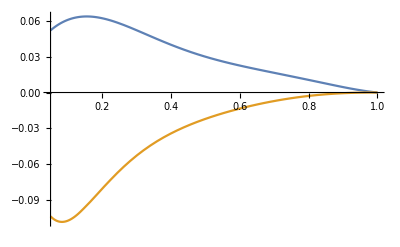

```mathematica
Plot[{H1perpFavHalfMoment[z,1.],H1perpUnfHalfMoment[z,1.]},{z,0.05,1}]
```

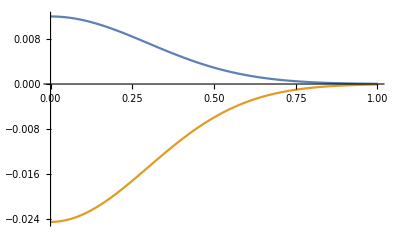

```mathematica
Plot[{H1perpFavTMD[0.1,1.,pt],H1perpUnfTMD[0.1,1.,pt]},{pt,0,1}]
```

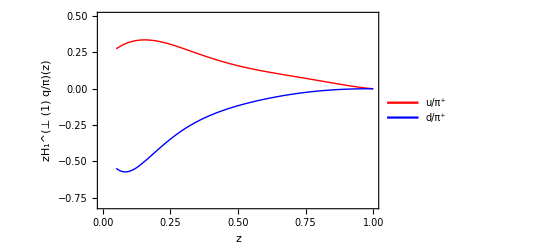

```mathematica
H1perpplot =Plot[{x H1perpFavFirstMoment[x,2.4],x H1perpUnfFirstMoment[x,2.4]},{x,0.05,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.8,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"z","zH_1^(⊥ (1) q/π)(z)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u/π^+","d/π^+"},{0.7,0.3}]]
```

```mathematica
Export["../tex/figs/H1perp.pdf",%,Background->None]
```

../tex/figs/H1perp.pdf

## f_(1T)^⊥

```mathematica
(*(*2009 fit*)
Clear[Ms,avks,Nu,Nusea,Nd,Ndsea,Nst,Nstbar,alphauv,alphadv,asea,beta, Mp];
Ms=Sqrt[0.34];
avks=avk Ms^2/(avk +Ms^2);
Nu=0.35;
Nusea=0.04;
Nd=-0.9000;
Ndsea=-0.4;
Nst=-0.24;
Nstbar=1.0000;
alphauv=0.73;
alphadv=1.08;
asea=0.79;
beta=3.46;
avPTs[z_]:= Sqrt[avp^2+avks^2 z^2]
Mp=0.938;
*)

(*2011 fit*)
Clear[Ms,avks,Nu,Nusea,Nd,Ndsea,Nst,Nstbar,alphauv,alphadv,asea,beta, Mp];
Ms=Sqrt[0.19];
avks=avk Ms^2/(avk +Ms^2);
Nu=0.4;
Nd=-0.97;
alphauv=0.35;
alphadv=0.44;
betauv=2.6;
betadv=0.9;
avPTs[z_]:= Sqrt[avp^2+avks^2 z^2]
Mp=0.938;

(* Sivers function with DGLAP Evolution*)
usiv[x_,Q2_]:=(Nu x^alphauv (1-x)^betauv (alphauv+ betauv)^(alphauv+ betauv)/((alphauv^alphauv)( betauv^betauv))) up[x,Q2]
dsiv[x_,Q2_]:=(Nd x^alphadv (1-x)^betadv (alphadv+ betadv)^(alphadv+ betadv)/((alphadv^alphadv)( betadv^betadv)))dn[x,Q2]
ubarsiv[x_,Q2_]:=0.
dbarsiv[x_,Q2_]:=0.
ssiv[x_,Q2_]:=0.
sbarsiv[x_,Q2_]:=0.

 (*Sivers function with DGLAP Evolution*)
f1TperpuFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)usiv[x,Q2] avks^2/avk ;
f1TperpdFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)dsiv[x,Q2] avks^2/avk;
f1TperpubarFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)ubarsiv[x,Q2] avks^2/avk ;
f1TperpdbarFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)dbarsiv[x,Q2] avks^2/avk;
f1TperpsFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)ssiv[x,Q2] avks^2/avk ;
f1TperpsbFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp Ms)sbarsiv[x,Q2] avks^2/avk;


f1TperpuTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)usiv[x,Q2]1/(π avk) Exp[-kt^2/avks];
f1TperpdTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)dsiv[x,Q2]1/(π avk) Exp[-kt^2/avks];
f1TperpubarTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)ubarsiv[x,Q2]1/(π avk) Exp[-kt^2/avks];
f1TperpdbarTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)dbarsiv[x,Q2]1/(π avk) Exp[-kt^2/avks];
f1TperpsTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)ssiv[x,Q2]1/(π avk) Exp[-kt^2/avks];
f1TperpsbTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)sbarsiv[x,Q2]1/(π avk) Exp[-kt^2/avks];
```

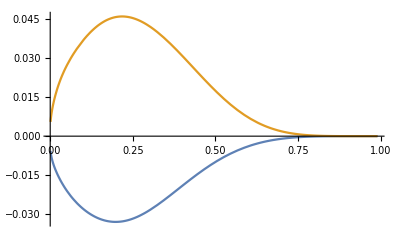

```mathematica
Plot[{x f1TperpuFirstMoment[x,1.],x f1TperpdFirstMoment[x,1.]},{x,0.001,0.99}]
```

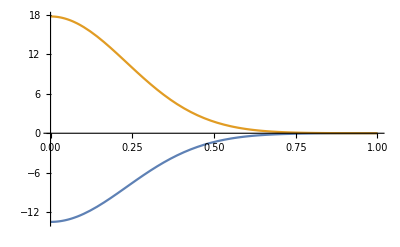

```mathematica
Plot[{f1TperpuTMD[0.1,1.,kt],f1TperpdTMD[0.1,1.,kt]},{kt,0,1}]
```

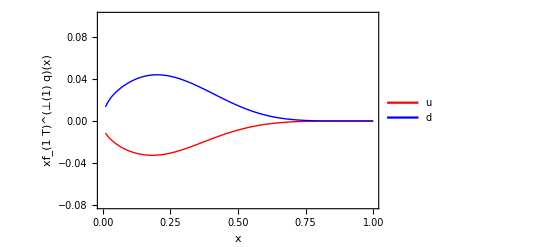

```mathematica
f1Tperpplot =Plot[{x f1TperpuFirstMoment[x,2.4],x f1TperpdFirstMoment[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.08,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xf_(1  T)^(⊥(1) q)(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/f1Tperp.pdf",%,Background->None]
```

../tex/figs/f1Tperp.pdf

## h_(1T)^⊥

```mathematica
(*2015 fit*)
Clear[MTT,avkTT,NuTT,NdTT,alphaTT,betaTT];
MTT=Sqrt[0.18];
avkTT=avk MTT^2/(avk+MTT^2);
NuTT=1;
NdTT=-1;
alphaTT=2.5;
betaTT=2.;
(* Pretzelosity function with DGLAP Evolution*)
huTT[x_,Q2_]:=ⅇ(NuTT x^alphaTT (1-x)^betaTT (alphaTT+ betaTT)^(alphaTT+ betaTT)/((alphaTT^alphaTT)( betaTT^betaTT))) (up[x,Q2]-g1u[x,Q2])
hdTT[x_,Q2_]:=ⅇ(NdTT x^alphaTT(1-x)^betaTT (alphaTT+ betaTT)^(alphaTT+ betaTT)/((alphaTT^alphaTT)( betaTT^betaTT)))(dn[x,Q2]-g1d[x,Q2])


 (*Pretzelosity function with DGLAP Evolution*)
h1TperpuFirstMoment[x_,Q2_]:=1/(2 MTT^2)huTT[x,Q2] avkTT^2/avk ;
h1TperpdFirstMoment[x_,Q2_]:=1/(2 MTT^2)hdTT[x,Q2] avkTT^2/avk;



h1TperpuTMD[x_,Q2_,kt_]:=Mp^2/MTT^2  huTT[x,Q2]1/(π avk) Exp[-kt^2/avkTT];
h1TperpdTMD[x_,Q2_,kt_]:=Mp^2/MTT^2  hdTT[x,Q2]1/(π avk) Exp[-kt^2/avkTT];


h1TperpuSecondMoment[x_,Q2_]:=1/(2 Mp^2 MTT^2)huTT[x,Q2] avkTT^3/avk ;
h1TperpdSecondMoment[x_,Q2_]:=1/(2 Mp^2 MTT^2)hdTT[x,Q2] avkTT^3/avk;
```

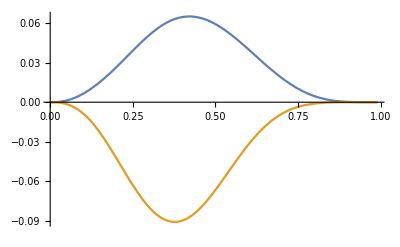

```mathematica
Plot[{x h1TperpuFirstMoment[x,1.],x h1TperpdFirstMoment[x,1.]},{x,0.001,0.99}]
```

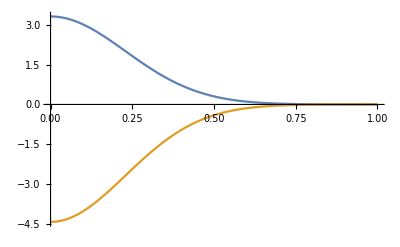

```mathematica
Plot[{h1TperpuTMD[0.1,1.,kt],h1TperpdTMD[0.1,1.,kt]},{kt,0,1}]
```

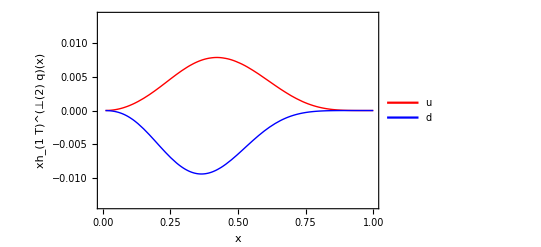

```mathematica
h1Tperpplot =Plot[{x h1TperpuSecondMoment[x,2.4],x h1TperpdSecondMoment[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.014,0.014}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xh_(1  T)^(⊥(2) q)(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.8,0.75}]]
```

```mathematica
Export["../tex/figs/h1Tperp.pdf",%,Background->None]
```

../tex/figs/h1Tperp.pdf

## h_1^⊥

```mathematica
(*(*2015 fit Boglione et al https://arxiv.org/pdf/1502.04214.pdf*)
Clear[MBM,avkBM,NuBM,NdBM];
MBM=Sqrt[0.1];
avkBM=avk MBM^2/(avk+MBM^2);
NuBM=-0.49;
NdBM=-1;

(* Boer-Mulders function with DGLAP Evolution*)
h1perpu[x_,Q2_]:=NuBM up[x,Q2]
h1perpd[x_,Q2_]:=NdBM dn[x,Q2] 


(*Boer-Mulders function with DGLAP Evolution*)
h1perpuFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MBM)h1perpu[x,Q2] avkBM^2/avk ;
h1perpdFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MBM)h1perpd[x,Q2] avkBM^2/avk;



h1perpuTMD[x_,Q2_,kt_]:=-√(2 ⅇ)Mp/MBM Exp[-kt^2/avkBM] h1perpu[x,Q2]/(π avk);
h1perpdTMD[x_,Q2_,kt_]:=-√(2 ⅇ)Mp/MBM Exp[-kt^2/avkBM] h1perpd[x,Q2]/(π avk);

*)


(*2010 fit Barone et al https://arxiv.org/pdf/0912.5194.pdf*)
MsBM=Sqrt[0.34];
avksBM=avk Ms^2/(avk +Ms^2);
avkBM =avksBM;
NuBM=2.1*0.35;
NuseaBM=-1.*0.04;
NdBM=(-1.111)*(-0.9000);
NdseaBM=-1.*0.4;
NstBM=0;
NstbarBM=0;
alphauvBM=0.73;
alphadvBM=1.08;
aseaBM=0.79;
betaBM=3.46;
avPTsBM[z_]:= Sqrt[avp^2+avksBM^2 z^2] 



 (*Boer-Mulders function with DGLAP Evolution*)
usivBM[x_,Q2_]:=(NuBM x^alphauvBM (1-x)^betaBM (alphauvBM+ betaBM)^(alphauvBM+ betaBM)/((alphauvBM^alphauvBM)( betaBM^betaBM))) up[x,Q2]
dsivBM[x_,Q2_]:=(NdBM x^alphadvBM (1-x)^betaBM (alphadvBM+ betaBM)^(alphadvBM+ betaBM)/((alphadvBM^alphadvBM)( betaBM^betaBM)))dn[x,Q2]
ubarsivBM[x_,Q2_]:=(NuseaBM x^aseaBM (1-x)^betaBM (aseaBM+ betaBM)^(aseaBM+ betaBM)/((aseaBM^aseaBM)( betaBM^betaBM))) upbar[x,Q2]
dbarsivBM[x_,Q2_]:=(NdseaBM x^aseaBM (1-x)^betaBM(aseaBM+ betaBM)^(aseaBM+ betaBM)/((aseaBM^aseaBM)( betaBM^betaBM))) dnbar[x,Q2]
ssivBM[x_,Q2_]:=(NstBM x^aseaBM (1-x)^betaBM (aseaBM+ betaBM)^(aseaBM+ betaBM)/((aseaBM^aseaBM)( betaBM^betaBM))) str[x,Q2]
sbarsivBM[x_,Q2_]:=(NstbarBM x^aseaBM (1-x)^betaBM (aseaBM+ betaBM)^(aseaBM+ betaBM)/((aseaBM^aseaBM)( betaBM^betaBM))) sbar[x,Q2]

 (*Sivers function with DGLAP Evolution*)
h1perpuFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)usivBM[x,Q2] avksBM^2/avk ;
h1perpdFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)dsivBM[x,Q2] avksBM^2/avk;
h1perpubarFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)ubarsivBM[x,Q2] avksBM^2/avk ;
h1perpdbarFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)dbarsivBM[x,Q2] avksBM^2/avk;
h1perpsFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)ssivBM[x,Q2] avksBM^2/avk ;
h1perpsbFirstMoment[x_,Q2_]:=-√(ⅇ/2)1/(Mp MsBM)sbarsivBM[x,Q2] avksBM^2/avk;


h1perpuTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)usivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
h1perpdTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)dsivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
h1perpubarTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)ubarsivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
h1perpdbarTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)dbarsivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
h1perpsTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)ssivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
h1perpsbTMD[x_,Q2_,kt_]:=-Mp/Ms √(2 ⅇ)sbarsivBM[x,Q2]1/(π avk) Exp[-kt^2/avksBM];
```

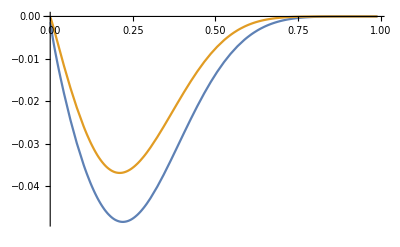

```mathematica
Plot[{x h1perpuFirstMoment[x,1.],x h1perpdFirstMoment[x,1.]},{x,0.001,0.99}]
```

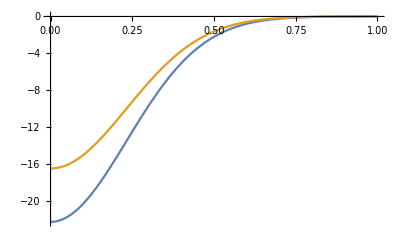

```mathematica
Plot[{h1perpuTMD[0.1,1.,kt],h1perpdTMD[0.1,1.,kt]},{kt,0,1}]
```

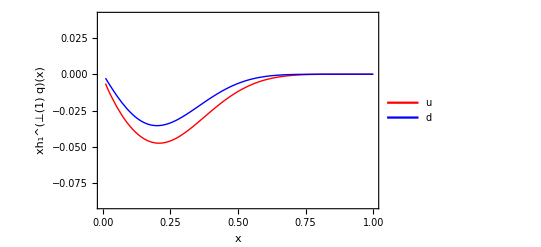

```mathematica
h1perpplot =Plot[{x h1perpuFirstMoment[x,2.4],x h1perpdFirstMoment[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.09,0.04}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xh_1^(⊥(1) q)(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.17}]]
```

```mathematica
Export["../tex/figs/h1perpBM.pdf",%,Background->None]
```

../tex/figs/h1perpBM.pdf

## WW-type relations

## Error band 40%

```mathematica
ErrorBand[func_,xmin_,xmax_, npt_,color_] := {
xstep = (xmax - xmin)/npt;
min = Table[{0,0},npt+1];
max = Table[{0,0},npt+1];

For[i=0,i≤npt,i++,
x = xmin + xstep i;

min[[i+1,1]] = x;
max[[i+1,1]] =  x;

xeps = If[1.2 x≤ 1,1.2 x, 1];

funct = func[0.8 x];
functeps = func[xeps];

min[[i+1,2]] = 1.2 functeps;
max[[i+1,2]] =  1.2 functeps;

t1 = 0.8 funct;
t2 = 1.2 funct;
t3 = 0.8 functeps;

If[min[[i+1,2]] ≥ t1, min[[i+1,2]] = t1];
If[min[[i+1,2]] ≥ t2, min[[i+1,2]] = t2];
If[min[[i+1,2]] ≥ t3, min[[i+1,2]] = t3];

If[max[[i+1,2]] ≤  t1, max[[i+1,2]] = t1];
If[max[[i+1,2]] ≤  t2, max[[i+1,2]] = t2];
If[max[[i+1,2]]≤  t3, max[[i+1,2]] = t3];

];

ListPlot[{max,min},Filling->{1->{2}},FillingStyle->Directive[color,Opacity[0.2]],Frame-> False,PlotStyle->None, Joined-> True]};

(*Plot[{1.2 func[1.2 x],0.8 func[0.8 x],1.2 func[0.8 x],0.8 func[1.2 x]},{x,xmin,xmax},Filling->{1->{2},3->{4}},Frame-> False, PlotPoints->10,MaxRecursion->1,PlotStyle->None]*)
```

```mathematica
ϵ1:=0.20
ϵ2[x_]:=0.20*(1-x)^0.05

ErrorBandX[func_,xmin_,xmax_, npt_,color_] := {
xstep = (xmax - xmin)/npt;
min = Table[{0,0},npt+1];
max = Table[{0,0},npt+1];

For[i=0,i≤npt,i++,
x = xmin + xstep i;

min[[i+1,1]] = x;
max[[i+1,1]] =  x;

xeps = If[(1+ϵ2[x]) x≤ 1,(1+ϵ2[x]) x, 1];

funct = func[(1-ϵ2[x]) x];
functeps = func[xeps];

min[[i+1,2]] = (1+ϵ1) functeps;
max[[i+1,2]] =  (1+ϵ1) functeps;

t1 = (1-ϵ1) funct;
t2 = (1+ϵ1) funct;
t3 = (1-ϵ1) functeps;

If[min[[i+1,2]] ≥ t1, min[[i+1,2]] = t1];
If[min[[i+1,2]] ≥ t2, min[[i+1,2]] = t2];
If[min[[i+1,2]] ≥ t3, min[[i+1,2]] = t3];

If[max[[i+1,2]] ≤  t1, max[[i+1,2]] = t1];
If[max[[i+1,2]] ≤  t2, max[[i+1,2]] = t2];
If[max[[i+1,2]]≤  t3, max[[i+1,2]] = t3];

];

ListPlot[{max,min},Filling->{1->{2}},FillingStyle->Directive[color,Opacity[0.2]],Frame-> False,PlotStyle->{{Thin,color},{Thin,color}}, Joined-> True]};

(*Plot[{1.2 func[1.2 x],0.8 func[0.8 x],1.2 func[0.8 x],0.8 func[1.2 x]},{x,xmin,xmax},Filling->{1->{2},3->{4}},Frame-> False, PlotPoints->10,MaxRecursion->1,PlotStyle->None]*)
```

```mathematica
ErrorBandPrint[func_,xmin_,xmax_, npt_,file_] := {
xstep = (xmax - xmin)/npt;
min = Table[{0,0},npt+1];
max = Table[{0,0},npt+1];
central = Table[{0,0},npt+1];

For[i=0,i≤npt,i++,
x = xmin + xstep i;

min[[i+1,1]] = x;
max[[i+1,1]] =  x;
central[[i+1,1]] =  x;

xeps = If[1.2 x≤ 1,1.2 x, 1];

funct = func[0.8 x];
functeps = func[xeps];

min[[i+1,2]] = 1.2 functeps;
max[[i+1,2]] =  1.2 functeps;
central[[i+1,2]] = functeps;

t1 = 0.8 funct;
t2 = 1.2 funct;
t3 = 0.8 functeps;

If[min[[i+1,2]] ≥ t1, min[[i+1,2]] = t1];
If[min[[i+1,2]] ≥ t2, min[[i+1,2]] = t2];
If[min[[i+1,2]] ≥ t3, min[[i+1,2]] = t3];

If[max[[i+1,2]] ≤  t1, max[[i+1,2]] = t1];
If[max[[i+1,2]] ≤  t2, max[[i+1,2]] = t2];
If[max[[i+1,2]]≤  t3, max[[i+1,2]] = t3];

];

Export[file,{central,min,max},"CSV"]};
```

```mathematica
(*based on numbers from Bakur*)
ϵ1:=0.20
ϵ2[x_]:=0.20*(1-x)^0.05

ErrorBandCOMPASS[func_,pion_,color_,file_] := {



Clear[data];
data=Cases[Import["./data/compass_bins_average.dat","Table"],{_?NumberQ,___}]; 
npt = Length[data];

central = Table[{0,0},npt];
min = Table[{0,0},npt];
max = Table[{0,0},npt];


For[i=1,i≤npt,i++,
xcom = data[[i]][[1]];
ycom = data[[i]][[2]] ;
zcom = data[[i]][[3]] ;
PTcom = data[[i]][[4]] ;
Wcom = data[[i]][[5]] ;
Q2com = data[[i]][[6]] ;


min[[i,1]] = xcom;
max[[i,1]] =  xcom;
central[[i,1]] =  xcom;

central[[i,2]] =  func[pion,xcom,zcom,Q2com,PTcom];

xeps = If[(1+ϵ2[xcom]) xcom≤ 1,(1+ϵ2[xcom]) xcom, 1];

funct = func[pion,(1-ϵ2[xcom]) xcom,zcom,Q2com,PTcom];
functeps = func[pion,xeps,zcom,Q2com,PTcom];

min[[i,2]] = (1-ϵ1) functeps;
max[[i,2]] = (1+ϵ1) functeps;

t1 = (1-ϵ1) funct;
t2 = (1+ϵ1) funct;
t3 = (1-ϵ1) functeps;

If[min[[i,2]] ≥ t1, min[[i,2]] = t1];
If[min[[i,2]] ≥ t2, min[[i,2]] = t2];
If[min[[i,2]] ≥ t3, min[[i,2]] = t3];

If[max[[i,2]] ≤  t1, max[[i,2]] = t1];
If[max[[i,2]] ≤  t2, max[[i,2]] = t2];
If[max[[i,2]]≤  t3, max[[i,2]] = t3];


];
(*plotting here*)
Export[file,{central,min,max},"CSV"];
ListPlot[{max,min},Filling->{1->{2}},FillingStyle->Directive[color,Opacity[0.2]],Frame-> False,PlotStyle->{{Thin,color},{Thin,color}}, Joined-> True,InterpolationOrder->4]
(*  ListPlot[{central},PlotStyle->{{color, Thick}},Frame-> False,PlotStyle->None, Joined-> True,InterpolationOrder->4,Frame-> True] *) 



};
```

## WW-type relation for h_(1L)^⊥

```mathematica
h1Lu[x_,Q_] :=-x^2 NIntegrate[h1u[y,Q]/y^2,{y,x,1.}];
h1Ld[x_,Q_] :=-x^2  NIntegrate[h1d[y,Q]/y^2,{y,x,1.}];
```

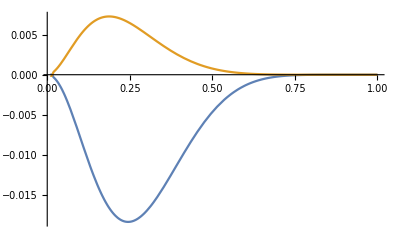

```mathematica
Plot[{x h1Lu[x,1.],x h1Ld[x,1.]},{x,0.01,1}]
```

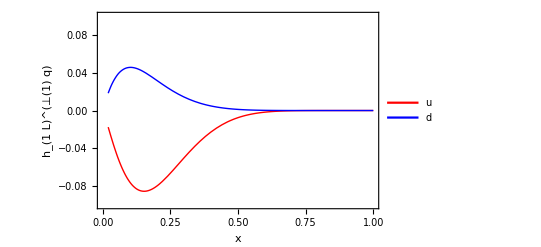

```mathematica
Plot[{h1Lu[x,2.4],h1Ld[x,2.4]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.1,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","h_(1  L)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/h1Lperp.pdf",%,Background->None]
```

../tex/figs/h1Lperp.pdf

## WW relation for g_T

```mathematica
gTu[x_,Q2_] := NIntegrate[g1u[y,Q2]/y,{y,x,1.}];
gTd[x_,Q2_] := NIntegrate[g1d[y,Q2]/y,{y,x,1.}];
gTubar[x_,Q2_] := NIntegrate[g1ubar[y,Q2]/y,{y,x,1.}];
gTdbar[x_,Q2_] := NIntegrate[g1dbar[y,Q2]/y,{y,x,1.}];
gTs[x_,Q2_] := NIntegrate[g1s[y,Q2]/y,{y,x,1.}];
gTsbar[x_,Q2_] := NIntegrate[g1sbar[y,Q2]/y,{y,x,1.}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0204173}. NIntegrate obtained 6.16095 and 0.0000104912 for the integral and error estimates.

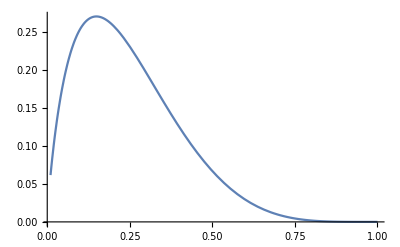

```mathematica
Plot[{x*gTu[x,1.]},{x,0.01,1}]
```

Data for g2

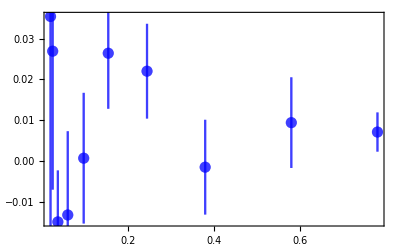

```mathematica
Clear[data,tab];
data=Cases[Import["/Users/avp5627/Dropbox/Miniproject/mathematica/data/g2_e155_neutron.dat","Table"],{_?NumberQ,___}];
tab =  Table[{{data[[i]][[3]],data[[i]][[9]]},ErrorBar[data[[i]][[10]]]},{i,Length[data]},{j,1}];
plotdatag2n=ErrorListPlot[tab, Frame-> True,PlotRange->{All,All}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]},{Blue,PointSize[0.02],Opacity[0.5]}}]
```

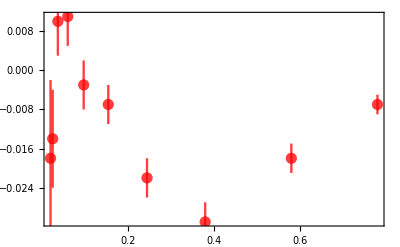

```mathematica
Clear[data,tab];
data=Cases[Import["/Users/avp5627/Dropbox/Miniproject/mathematica/data/g2_e155_all_proton.dat","Table"],{_?NumberQ,___}];
tab =  Table[{{data[[i]][[3]],data[[i]][[9]]},ErrorBar[data[[i]][[10]]]},{i,Length[data]},{j,1}];
plotdatag2=ErrorListPlot[tab, Frame-> True,PlotRange->{All,All}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]},{Red,PointSize[0.02],Opacity[0.5]}}]
```

WW relation for g2

```mathematica
g2[x_,Q2_] := 1/2 * (4./9.  gTu[x,Q2]+1./9. gTd[x,Q2] + 4./9. gTubar[x,Q2]+1./9. gTdbar[x,Q2] + 1./9. gTs[x,Q2]+1./9. gTsbar[x,Q2]) - 1/2 * (4./9. g1u[x,Q2]+  1./9. g1d[x,Q2] + 4./9. g1ubar[x,Q2]+1./9. g1dbar[x,Q2] + 1./9. g1s[x,Q2]+1./9. g1sbar[x,Q2]);

g2n[x_,Q2_] := 1/2 * (4./9.  gTd[x,Q2]+1./9. gTu[x,Q2] + 4./9. gTdbar[x,Q2]+1./9. gTubar[x,Q2] + 1./9. gTs[x,Q2]+1./9. gTsbar[x,Q2]) - 1/2 * (4./9. g1d[x,Q2]+  1./9. g1u[x,Q2] + 4./9. g1dbar[x,Q2]+1./9. g1ubar[x,Q2] + 1./9. g1s[x,Q2]+1./9. g1sbar[x,Q2]);
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.03031206937143339497087168865618878044188022613525390625}. NIntegrate obtained 6.29799 and 6.90735×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.03031206937143339497087168865618878044188022613525390625}. NIntegrate obtained -3.26498 and 8.42643×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0411332}. NIntegrate obtained 0.324507 and 5.45211×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

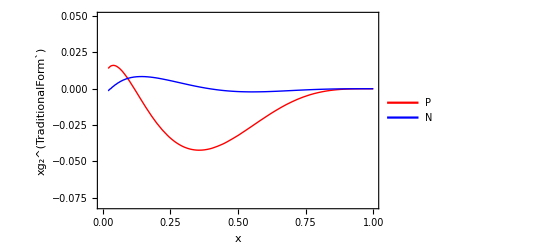

```mathematica
g2plot = Plot[{x*g2[x,7.1],x*g2n[x,7.1]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.08,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xg_2^(TraditionalForm`)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"P","N"},{0.7,0.1}]]
```

Error band for g2

```mathematica
g2func[x_] :=x*g2[x,7.1];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained 6.92886 and 0.0000219193 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained -3.77057 and 0.0000263667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained 0.470829 and 0.0000110711 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.,7.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

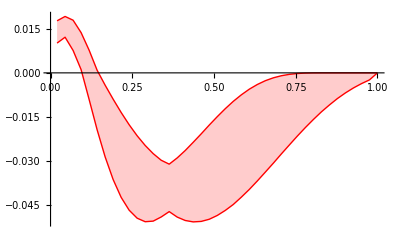

```mathematica
g2errorband = ErrorBandX[g2func,0.02,1,40,Red]
```

```mathematica
g2nfunc[x_] :=x*g2n[x,7.1];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained -3.77057 and 0.0000263667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained 6.92886 and 0.0000219193 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained -1.31853 and 8.47196×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.,7.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

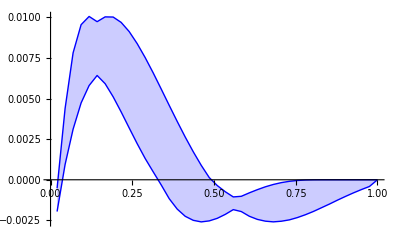

```mathematica
g2nerrorband = ErrorBandX[g2nfunc,0.02,1,40,Blue]
```

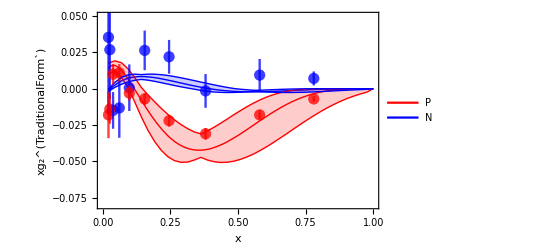

```mathematica
Show[g2plot,g2errorband,g2nerrorband ,plotdatag2n,plotdatag2]
```

```mathematica
Export["../tex/figs/g2.pdf",%,Background->None]
```

../tex/figs/g2.pdf

## WW relation for g_T (plotting g_2(x) with "consistent uncertainty band")

```mathematica
g1p[y_,Q2_] := (4/9 g1u[y,Q2]+4/9 g1ubar[y,Q2]+1/9 g1d[y,Q2]+1/9 g1dbar[y,Q2]+1/9 g1s[y,Q2]+1/9 g1sbar[y,Q2]);
g1n[y_,Q2_] := (4/9 g1d[y,Q2]+4/9 g1dbar[y,Q2]+1/9 g1u[y,Q2]+1/9 g1ubar[y,Q2]+1/9 g1s[y,Q2]+1/9 g1sbar[y,Q2]);
gTp[x_,Q2_] := NIntegrate[g1p[y,Q2]/y,{y,x,1.}];
gTn[x_,Q2_] := NIntegrate[g1n[y,Q2]/y,{y,x,1.}];

g2pNEW[x_,Q2_]:=(gTp[x,Q2] -g1p[x,Q2] )/2 ;
g2nNEW[x_,Q2_]:=(gTn[x,Q2] -g1n[x,Q2] )/2 ;
```

```mathematica
g2pNEW[0.3,2.4]
g2[0.3,2.4]
g2nNEW[0.3,2.4]
g2n[0.3,2.4]
```

-0.140355

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.31508114686476587466834597961451436276547610759735107421875}. NIntegrate obtained -0.00369216 and 4.59079×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.31508114686476587466834597961451436276547610759735107421875}. NIntegrate obtained 0.00219968 and 2.53866×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-0.140355

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.3150811468647659}. NIntegrate obtained 0.00264129 and 1.46039×10^-8 for the integral and error estimates.

0.016622

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.31508114686476587466834597961451436276547610759735107421875}. NIntegrate obtained -0.00369216 and 4.59079×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.31508114686476587466834597961451436276547610759735107421875}. NIntegrate obtained 0.00219968 and 2.53866×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.016622

### uncertainty band (as described in paper)

```mathematica
ϵ1:=0.20
ϵ2[x_]:=0.20*(1-x)^0.05

g2pNEWmax[x_,Q2_]:=D[xx*NIntegrate[g1p[y(1+ϵ2[y]),Q2]/y,{y,xx,1.}]/2,xx]/.xx->x
g2nNEWmax[x_,Q2_]:=D[xx*NIntegrate[g1n[y(1+ϵ2[y]),Q2]/y,{y,xx,1.}]/2,xx]/.xx->x
g2pNEWmin[x_,Q2_]:=D[xx*NIntegrate[g1p[y(1-ϵ2[y]),Q2]/y,{y,xx,1.}]/2,xx]/.xx->x
g2nNEWmin[x_,Q2_]:=D[xx*NIntegrate[g1n[y(1-ϵ2[y]),Q2]/y,{y,xx,1.}]/2,xx]/.xx->x
```

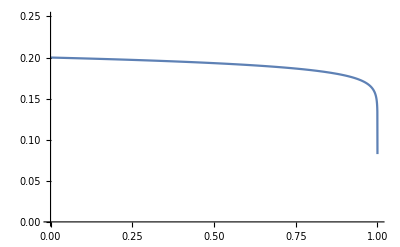

```mathematica
Plot[ϵ2[x],{x,0,1},PlotRange->{0,0.25}]
```

### define tables

```mathematica
xg2pTABLEmax[Q2_]:=Table[{x,x*Max[
(1+ϵ1)D[xx*NIntegrate[g1p[y(1+ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1+ϵ1)D[xx*NIntegrate[g1p[y(1-ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1-ϵ1)D[xx*NIntegrate[g1p[y(1+ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1-ϵ1)D[xx*NIntegrate[g1p[y(1-ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x]},{x,0.01,1,0.04}]

xg2pTABLEopt[Q2_]:=Table[{x,
x*D[xx*NIntegrate[g1p[y,Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x},{x,0.01,1,0.04}]

xg2pTABLEmin[Q2_]:=Table[{x,x*Min[
(1+ϵ1)D[xx*NIntegrate[g1p[y(1+ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1+ϵ1)D[xx*NIntegrate[g1p[y(1-ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1-ϵ1)D[xx*NIntegrate[g1p[y(1+ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1-ϵ1)D[xx*NIntegrate[g1p[y(1-ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x]},{x,0.01,1,0.04}]

xg2nTABLEmax[Q2_]:=Table[{x,x*Max[
(1+ϵ1)D[xx*NIntegrate[g1n[y(1+ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1+ϵ1)D[xx*NIntegrate[g1n[y(1-ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1-ϵ1)D[xx*NIntegrate[g1n[y(1+ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1-ϵ1)D[xx*NIntegrate[g1n[y(1-ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x]},{x,0.01,1,0.04}]

xg2nTABLEopt[Q2_]:=Table[{x,
x*D[xx*NIntegrate[g1n[y,Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x},{x,0.01,1,0.04}]

xg2nTABLEmin[Q2_]:=Table[{x,x*Min[
(1+ϵ1)D[xx*NIntegrate[g1n[y(1+ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1+ϵ1)D[xx*NIntegrate[g1n[y(1-ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1-ϵ1)D[xx*NIntegrate[g1n[y(1+ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x,
(1-ϵ1)D[xx*NIntegrate[g1n[y(1-ϵ2[y]),Q2]/y,{y,xx,0.999}]/2,xx]/.xx->x]},{x,0.01,1,0.04}]
```

### produce tables at Q^2=7.1 GeV^2

```mathematica
QQ2=7.1;
xg2pTABLEopt[QQ2]
```

NIntegrate::nlim: y = xx is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0203868}. NIntegrate obtained 3.30657 and 0.0000180242 for the integral and error estimates.

{{0.01,0.0106867},{0.05,0.0155579},{0.09,0.00769146},{0.13,-0.00405895},{0.17,-0.0159248},{0.21,-0.0261474},{0.25,-0.0339893},{0.29,-0.039172},{0.33,-0.0418224},{0.37,-0.0421749},{0.41,-0.0405605},{0.45,-0.0375035},{0.49,-0.0332931},{0.53,-0.028459},{0.57,-0.0233946},{0.61,-0.0184366},{0.65,-0.013856},{0.69,-0.00981132},{0.73,-0.00648694},{0.77,-0.00392957},{0.81,-0.00211584},{0.85,-0.000961126},{0.89,-0.000327945},{0.93,-0.0000662155},{0.97,-2.69992×10^-6}}

```mathematica
QQ2=7.1;
xg2pTABLEmax[QQ2]
```

NIntegrate::nlim: y = xx is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.016844660759139963579489318590276525355875492095947265625}. NIntegrate obtained 3.08424 and 3.58065×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0130713441189487327397100724368783630779944360256195068359375}. NIntegrate obtained 3.37142 and 0.000204208 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.016844660759139963579489318590276525355875492095947265625}. NIntegrate obtained 3.08424 and 3.58065×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.00462,7.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.01,0.0230196},{0.05,0.0239518},{0.09,0.0177167},{0.13,0.00512011},{0.17,-0.00629469},{0.21,-0.0158313},{0.25,-0.0243072},{0.29,-0.0281667},{0.33,-0.0276338},{0.37,-0.0254917},{0.41,-0.0222585},{0.45,-0.0184288},{0.49,-0.0144234},{0.53,-0.0106078},{0.57,-0.00725139},{0.61,-0.00453828},{0.65,-0.0025225},{0.69,-0.00118486},{0.73,-0.000431592},{0.77,-0.000097967},{0.81,-6.94841×10^-6},{0.85,-2.91012×10^-8},{0.89,2.52924×10^-6},{0.93,5.36412×10^-6},{0.97,8.32067×10^-6}}

```mathematica
QQ2=7.1;
xg2pTABLEmin[QQ2]
```

NIntegrate::nlim: y = xx is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.016844660759139963579489318590276525355875492095947265625}. NIntegrate obtained 3.08424 and 3.58065×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0130713441189487327397100724368783630779944360256195068359375}. NIntegrate obtained 3.37142 and 0.000204208 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.016844660759139963579489318590276525355875492095947265625}. NIntegrate obtained 3.08424 and 3.58065×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.00462,7.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.01,0.0074568},{0.05,0.00956532},{0.09,0.00181583},{0.13,-0.0117376},{0.17,-0.0245946},{0.21,-0.0341693},{0.25,-0.0399901},{0.29,-0.0468949},{0.33,-0.0548},{0.37,-0.0601345},{0.41,-0.0629617},{0.45,-0.0635426},{0.49,-0.0621458},{0.53,-0.0589739},{0.57,-0.054584},{0.61,-0.0492387},{0.65,-0.0431888},{0.69,-0.0368902},{0.73,-0.0305953},{0.77,-0.0244917},{0.81,-0.0188753},{0.85,-0.0139061},{0.89,-0.0095861},{0.93,-0.00608872},{0.97,-0.00330962}}

```mathematica
QQ2=7.1;
xg2nTABLEopt[QQ2]
```

NIntegrate::nlim: y = xx is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0203868}. NIntegrate obtained -2.07229 and 0.0000420851 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0611927804726627548592698957463653641752898693084716796875}. NIntegrate obtained -0.444925 and 6.43429×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.161001}. NIntegrate obtained -0.179923 and 2.71149×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.01,-0.00133859},{0.05,0.00316841},{0.09,0.00696152},{0.13,0.00829734},{0.17,0.00811926},{0.21,0.00706897},{0.25,0.00557567},{0.29,0.00389781},{0.33,0.00225883},{0.37,0.000792153},{0.41,-0.000404846},{0.45,-0.00129184},{0.49,-0.00185108},{0.53,-0.00211532},{0.57,-0.00213411},{0.61,-0.00196714},{0.65,-0.00167742},{0.69,-0.00131723},{0.73,-0.000952458},{0.77,-0.000624766},{0.81,-0.000361749},{0.85,-0.000175925},{0.89,-0.000064009},{0.93,-0.0000137361},{0.97,-6.18233×10^-7}}

```mathematica
QQ2=7.1;
xg2nTABLEmax[QQ2]
```

NIntegrate::nlim: y = xx is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.016844660759139963579489318590276525355875492095947265625}. NIntegrate obtained -1.8049 and 5.06632×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0130713441189487327397100724368783630779944360256195068359375}. NIntegrate obtained -3.18357 and 0.000672961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.016844660759139963579489318590276525355875492095947265625}. NIntegrate obtained -1.8049 and 5.06632×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.00462,7.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.01,0.0285705},{0.05,0.00437633},{0.09,0.00849178},{0.13,0.0115343},{0.17,0.0125369},{0.21,0.0121958},{0.25,0.0110149},{0.29,0.00931841},{0.33,0.00735521},{0.37,0.0053081},{0.41,0.00331525},{0.45,0.00150996},{0.49,-0.0000281371},{0.53,-0.000865881},{0.57,-0.000947424},{0.61,-0.000660798},{0.65,-0.000403357},{0.69,-0.000206078},{0.73,-0.0000810541},{0.77,-0.0000198029},{0.81,-1.54009×10^-6},{0.85,-7.00511×10^-9},{0.89,5.95444×10^-7},{0.93,1.2631×10^-6},{0.97,1.95941×10^-6}}

```mathematica
QQ2=7.1;
xg2nTABLEmin[QQ2]
```

NIntegrate::nlim: y = xx is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.016844660759139963579489318590276525355875492095947265625}. NIntegrate obtained -1.8049 and 5.06632×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0130713441189487327397100724368783630779944360256195068359375}. NIntegrate obtained -3.18357 and 0.000672961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.016844660759139963579489318590276525355875492095947265625}. NIntegrate obtained -1.8049 and 5.06632×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.00462,7.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.01,-0.00235074},{0.05,0.00177617},{0.09,0.00521326},{0.13,0.00555536},{0.17,0.00486783},{0.21,0.00368637},{0.25,0.00235153},{0.29,0.00108239},{0.33,0.0000199298},{0.37,-0.00113906},{0.41,-0.00185082},{0.45,-0.00214153},{0.49,-0.00209797},{0.53,-0.00182243},{0.57,-0.00223505},{0.61,-0.00285177},{0.65,-0.00316487},{0.69,-0.00323266},{0.73,-0.00308551},{0.77,-0.00277149},{0.81,-0.00236058},{0.85,-0.00189655},{0.89,-0.00141342},{0.93,-0.000965132},{0.97,-0.000564255}}

### my laptop is slow, so produce tables at Q^2= 7.1 GeV^2 for faster plotting

```mathematica
xg2pOPT=Interpolation[{{0.01,0.01068668907942301},{0.05,0.015557934759414664},{0.09,0.007691461480110476},{0.13,-0.004058949432586},{0.17,-0.015924830266623766},{0.21,-0.02614736677194213},{0.25,-0.03398930413188044},{0.29,-0.03917202290114099},{0.33,-0.0418224124210971},{0.37,-0.04217492987878583},{0.41,-0.0405604624114547},{0.45,-0.0375034510439458},{0.49,-0.03329312492664232},{0.53,-0.02845896441870566},{0.57,-0.023394563380262367},{0.61,-0.018436647632515107},{0.65,-0.013855993852983164},{0.69,-0.00981131827988031},{0.73,-0.006486943283791474},{0.77,-0.003929569378045121},{0.81,-0.002115835356308412},{0.85,-0.0009611261904629966},{0.89,-0.0003279452007726575},{0.93,-0.00006621547298072754},{0.97,-2.6999162296264106*^-6},{1.0,0.0}}];

xg2pMAX=Interpolation[{{0.01,0.023019616820813122},{0.05,0.023951791369159744},{0.09,0.017716735231327087},{0.13,0.005120110015150908},{0.17,-0.006294686133294676},{0.21,-0.015831343218701995},{0.25,-0.02430718256876188},{0.29,-0.02816666756432914},{0.33,-0.027633795972044992},{0.37,-0.025491730281200886},{0.41,-0.02225846802449361},{0.45,-0.0184288111726495},{0.49,-0.014423384832990906},{0.53,-0.010607806035878353},{0.57,-0.007251393999300332},{0.61,-0.004538276680966712},{0.65,-0.002522497568791892},{0.69,-0.0011848629230761876},{0.73,-0.0004315920047240201},{0.77,-0.00009796698903658796},{0.81,-6.948413731069016*^-6},{0.85,-2.9101240595394865*^-8},{0.89,2.5292415844625926*^-6},{0.93,5.364121665513444*^-6},{0.97,8.320668269262335*^-6},{1.0,0.0}}];

xg2pMIN=Interpolation[{{0.01,0.0074567984706386346},{0.05,0.009565324917604935},{0.09,0.0018158297552566878},{0.13,-0.01173760468433521},{0.17,-0.0245946239539983},{0.21,-0.03416928703213165},{0.33,-0.054799954942295254},{0.37,-0.06013447585902606},{0.41,-0.06296174891717464},{0.45,-0.06354259400253644},{0.49,-0.06214581901583941},{0.53,-0.05897393457201082},{0.57,-0.05458401903887673},{0.61,-0.04923869042541562},{0.65,-0.043188795911295624},{0.69,-0.036890165011333374},{0.73,-0.030595289069410295},{0.77,-0.024491722041412114},{0.81,-0.018875270423784476},{0.85,-0.013906070621055384},{0.89,-0.00958609954238148},{0.93,-0.0060887150232514595},{0.97,-0.0033096231386689702},{1.0,0.0}}];

xg2nOPT=Interpolation[{{0.01,-0.001338585526227718},{0.05,0.0031684107211322615},{0.09,0.006961520174982238},{0.13,0.008297344780096055},{0.17,0.008119262949727904},{0.21,0.007068967426451336},{0.25,0.00557566619835954},{0.29,0.0038978148750268104},{0.33,0.002258834420668854},{0.37,0.0007921532245602796},{0.41,-0.0004048463568989388},{0.45,-0.0012918368438196539},{0.49,-0.0018510753125527725},{0.53,-0.0021153159042884033},{0.57,-0.0021341116842551223},{0.61,-0.0019671358131067304},{0.65,-0.0016774214844866302},{0.69,-0.001317229353286556},{0.73,-0.0009524577122324208},{0.77,-0.00062476622734396},{0.81,-0.00036174894803489994},{0.85,-0.0001759247798276916},{0.89,-0.00006400900574680996},{0.93,-0.000013736059195003458},{0.97,-6.182332228044906*^-7},{1.0,0.0}}];

xg2nMAX=Interpolation[{{0.01,0.00128570452418000377},{0.05,0.004376334920530879},{0.09,0.008491776117160867},{0.13,0.011534345950706655},{0.17,0.012536932952766195},{0.21,0.012195804289509848},{0.25,0.011014865954702649},{0.29,0.009318409143228876},{0.33,0.007355209367724511},{0.37,0.005308099101429886},{0.41,0.0033152519828720944},{0.45,0.001509956016854515},{0.49,-0.00002813713872918637},{0.53,-0.0008658813135887902},{0.57,-0.0009474236268450454},{0.61,-0.0006607979192113325},{0.65,-0.00040335651883534633},{0.69,-0.00020607796589719546},{0.73,-0.00008105408354363086},{0.77,-0.0000198029461725132},{0.81,-1.5400925729514743*^-6},{0.85,-7.005106061428311*^-9},{0.89,5.954439250491229*^-7},{0.93,1.263098783316005*^-6},{0.97,1.9594083436913264*^-6},{1.0,0.0}}];

xg2nMIN=Interpolation[{{0.01,-0.0023507446870702138},{0.05,0.0017761730752249274},{0.09,0.005213261967918429},{0.13,0.005555364984504292},{0.17,0.004867825995349203},{0.21,0.003686367384482033},{0.25,0.002351526063436809},{0.29,0.0010823889763876768},{0.33,0.000019929754458139776},{0.37,-0.0011390638761695053},{0.41,-0.001850817358392434},{0.69,-0.0032326625730184815},{0.73,-0.003085513961895446},{0.77,-0.002771490371257938},{0.81,-0.002360580097013898},{0.85,-0.0018965507122053209},{0.89,-0.00141341571793455},{0.93,-0.0009651322230098856},{0.97,-0.0005642552477917136},{1.0,0.0}}];
```

### produce figure for E155 at Q^2 =7.1 GeV^2

see curves

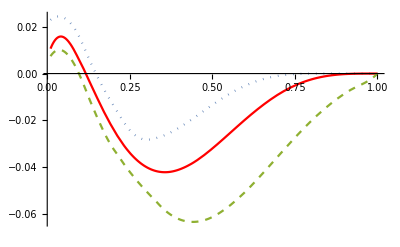

```mathematica
Plot[{xg2pMAX[x],xg2pOPT[x],xg2pMIN[x]},{x,0.01,1},PlotStyle->{Dotted,Red,Dashed}]
```

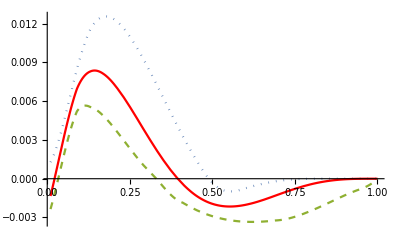

```mathematica
Plot[{xg2nMAX[x],xg2nOPT[x],xg2nMIN[x]},{x,0.01,1},PlotStyle->{Dotted,Red,Dashed}]
```

testing: leave out some points in interpolation to produce “smoother error band”

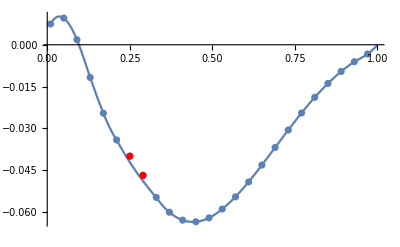

```mathematica
Show[Plot[xg2pMIN[x],{x,0.01,1}],ListPlot[{{0.01,0.0074567984706386346},{0.05,0.009565324917604935},{0.09,0.0018158297552566878},{0.13,-0.01173760468433521},{0.17,-0.0245946239539983},{0.21,-0.03416928703213165},{0.25,-0.039990130157839636},{0.29,-0.04689493127045056},{0.33,-0.054799954942295254},{0.37,-0.06013447585902606},{0.41,-0.06296174891717464},{0.45,-0.06354259400253644},{0.49,-0.06214581901583941},{0.53,-0.05897393457201082},{0.57,-0.05458401903887673},{0.61,-0.04923869042541562},{0.65,-0.043188795911295624},{0.69,-0.036890165011333374},{0.73,-0.030595289069410295},{0.77,-0.024491722041412114},{0.81,-0.018875270423784476},{0.85,-0.013906070621055384},{0.89,-0.00958609954238148},{0.93,-0.0060887150232514595},{0.97,-0.0033096231386689702}}],
ListPlot[{{0.25,-0.039990130157839636},,{0.29,-0.04689493127045056}},PlotStyle->Red]]
```

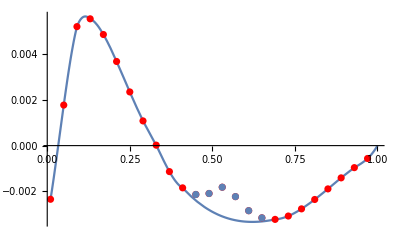

```mathematica
Show[Plot[xg2nMIN[x],{x,0.01,1}],
ListPlot[{{0.01,-0.0023507446870702138},{0.05,0.0017761730752249274},{0.09,0.005213261967918429},{0.13,0.005555364984504292},{0.17,0.004867825995349203},{0.21,0.003686367384482033},{0.25,0.002351526063436809},{0.29,0.0010823889763876768},{0.33,0.000019929754458139776},{0.37,-0.0011390638761695053},{0.41,-0.001850817358392434},{0.45,-0.002141529134834724},{0.49,-0.0020979698902119106},{0.53,-0.0018224252446631247},{0.57,-0.0022350521811370255},{0.61,-0.0028517747610469317},{0.65,-0.003164871007419303},{0.69,-0.0032326625730184815},{0.73,-0.003085513961895446},{0.77,-0.002771490371257938},{0.81,-0.002360580097013898},{0.85,-0.0018965507122053209},{0.89,-0.00141341571793455},{0.93,-0.0009651322230098856},{0.97,-0.0005642552477917136}},PlotStyle->Red],
ListPlot[{{0.45,-0.002141529134834724},{0.49,-0.0020979698902119106},{0.53,-0.0018224252446631247},{0.57,-0.0022350521811370255},{0.61,-0.0028517747610469317},{0.65,-0.003164871007419303}}]]
```

Data for g2

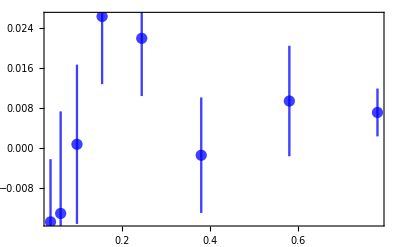

```mathematica
Clear[data,tab];
data=Cases[Import["data/g2_e155_neutron.dat","Table"],{_?NumberQ,___}];
tab =  Table[{{data[[i]][[3]],data[[i]][[9]]},ErrorBar[data[[i]][[10]]]},{i,Length[data]},{j,1}];
plotdatag2n=ErrorListPlot[tab, Frame-> True,PlotRange->{All,All}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]},{Blue,PointSize[0.02],Opacity[0.5]}}]
```

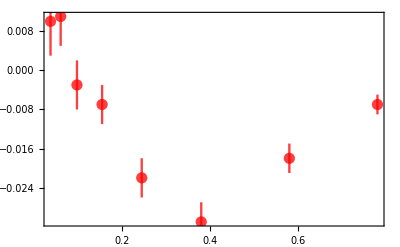

```mathematica
Clear[data,tab];
data=Cases[Import["data/g2_e155_all_proton.dat","Table"],{_?NumberQ,___}];
tab =  Table[{{data[[i]][[3]],data[[i]][[9]]},ErrorBar[data[[i]][[10]]]},{i,Length[data]},{j,1}];
plotdatag2=ErrorListPlot[tab, Frame-> True,PlotRange->{All,All}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]},{Red,PointSize[0.02],Opacity[0.5]}}]
```

WW relation for g2

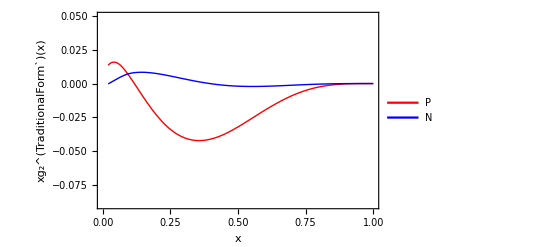

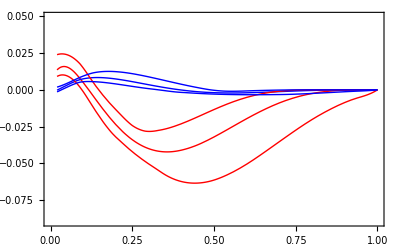

```mathematica
g2plot = Plot[{xg2pOPT[x],xg2nOPT[x]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.09,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue}}, FrameLabel->{"x","xg_2^(TraditionalForm`)(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"P","N"},{0.85,0.15}]]
g2plotagain = Plot[{xg2pOPT[x],xg2nOPT[x],xg2pMAX[x],xg2pMIN[x],xg2nMAX[x],xg2nMIN[x]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.09,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thin,Red},{Thin, Red},{Thin, Blue},{Thin, Blue}},BaseStyle->{FontSize->12,FontFamily->"Arial"}]
```

“better” error band for g2

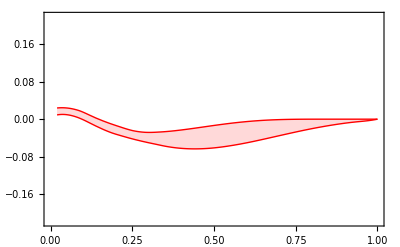

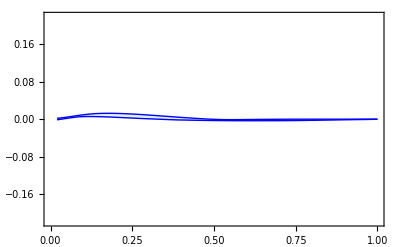

```mathematica
g2errorbandp = Plot[{xg2pMAX[x],xg2pMIN[x]},{x,0.02,1},Filling->{1->{{2},LightRed}},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.22,0.22}},PlotStyle->{{Thin,Red},{Thin, Red}}]
g2errorbandn = Plot[{xg2nMAX[x],xg2nMIN[x]},{x,0.02,1},Filling->{1->{{2},LightBlue}},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.22,0.22}},PlotStyle->{{Thin,Blue},{Thin, Blue}}]
```

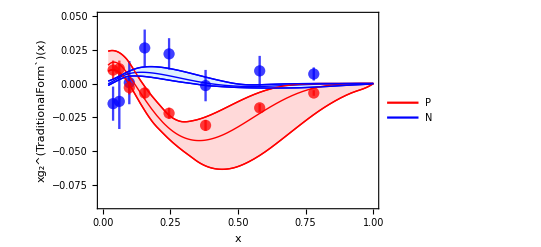

```mathematica
Show[g2plot,g2errorbandp,g2errorbandn,plotdatag2n,plotdatag2,g2plotagain]
```

```mathematica
Export["../tex/figs/g2.pdf",%,Background->None]
```

../tex/figs/g2.pdf

## WW-type relation for g_(1T)^⊥

```mathematica
g1Tperpu[x_,Q2_] := x NIntegrate[g1u[y,Q2]/y,{y,x,1.}];
g1Tperpd[x_,Q2_] := x NIntegrate[g1d[y,Q2]/y,{y,x,1.}];
g1Tperpubar[x_,Q2_] := x NIntegrate[g1ubar[y,Q2]/y,{y,x,1.}];
g1Tperpdbar[x_,Q2_] := x NIntegrate[g1dbar[y,Q2]/y,{y,x,1.}];
g1Tperps[x_,Q2_] := x NIntegrate[g1s[y,Q2]/y,{y,x,1.}];
g1Tperpsbar[x_,Q2_] := x NIntegrate[g1sbar[y,Q2]/y,{y,x,1.}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0204173}. NIntegrate obtained 7.32788 and 0.0000320626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0204173}. NIntegrate obtained -4.60653 and 0.0000401872 for the integral and error estimates.

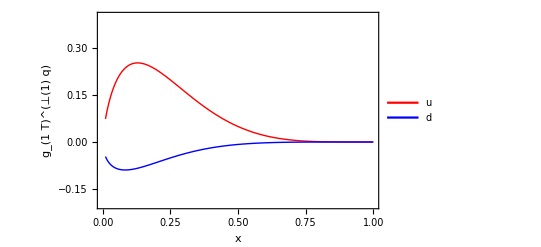

```mathematica
Plot[{g1Tperpu[x,2.4],g1Tperpd[x,2.4](*,g1Tperpubar[x,2.4],g1Tperpdbar[x,2.4]*)},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.2,0.4}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","g_(1  T)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d"(*,"ū","d̄"*)},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/g1t.pdf",%,Background->None]
```

../tex/figs/g1t.pdf

## Asymmetries SIDIS analytical calculation of all terms in SIDIS cross section using Bacchetta et al JHEP02 (2007) 093

## Definitions, Structure Functions, Convolutions, Etc :

```mathematica
Format[PhT]:=Subscript[P, hT];
Format[kt]:=Subscript[k, T];
Format[pt]:=Subscript[P, T];
Format[f1]:=Subscript[f, 1];
Format[hh1]:=Subscript[h, 1];
Format[hh1L]:=Subscript[h, 1L]^FIRST;
Format[g1]:=Subscript[g, 1];
Format[g1T]:=Subscript[g, 1T]^FIRST;
Format[H1FirstMoment] := Subscript[H, 1]^(perp FIRST);
Format[h1TperpSecondMoment] := Subscript[h, 1T]^(perp Second);
Format[f1TperpFirstMoment] := Subscript[f, 1T]^(perp FIRST);
Format[h1perpFirstMoment] := Subscript[h, 1]^(perp FIRST);
Format[D1]:=Subscript[D, 1];
Format[MBoerMulders]:=Subscript[M, BoerMulders];
Format[MCOLLINS]:=Subscript[M, COLLINS];
Format[MSIVERS]:=Subscript[M, SIVERS];
Format[Mhadron]:=Subscript[M, hadron];
Format[NBM]:=Subscript[N, BM];
Format[NCOLLINS]:= Subscript[N, COLLINS] ;
Format[NSIVERS]:=Subscript[N, SIVERS];
Format[kta]:=Subscript[k, TA]^2;
Format[pta]:=Subscript[p, TA]^2;
Format[ptC]:=Subscript[p, TCOLLINS]^2;
Format[ktg1]:=Subscript[k, Tg1]^2;
Format[kth1L]:=Subscript[k, Th1L]^2;
Format[ktg1T]:=Subscript[k, Tg1T]^2;
Format[kth1]:=Subscript[k, Th1]^2;
Format[kthL]:=Subscript[k, ThL]^2;
Format[ktBM]:=Subscript[k, TBM]^2;
Format[hh1]:=Subscript[hh, 1];
Format[ktS]:=Subscript[k, TSIVERS]^2;
Format[ktP]:=Subscript[k, TPRETZELOSITY]^2;
Format[ktBM]:=Subscript[k, BOERMULDERS]^2;
$Assumptions={z>0,Subscript[p, TA]^2>0,Subscript[k, TA]^2>0,Subscript[k, Tg1T]^2>0,Subscript[k, Th1L]^2>0,Subscript[k, Th1]^2>0,Subscript[k, BOERMULDERS]^2>0,Subscript[M, COLLINS]>0,ktH1>0,Subscript[M, BoerMulders]>0,Subscript[M, SIVERS]>0,z>0,z^2+Re[1/Subscript[k, Tg1T]^2] Subscript[p, TA]^2≥0&&((Re[Subscript[P, hT]]==0&&Im[Subscript[P, hT]]>0)||Re[Subscript[P, hT]]>0),Re[Subscript[P, hT]]>0||(Re[Subscript[P, hT]]≥0&&Im[Subscript[P, hT]]>0),z^2 Re[Subscript[k, Tg1T]^2]+Subscript[p, TA]^2>0,Re[1/MCollins^2] Subscript[p, TA]^2>-1,Re[Subscript[k, TSIVERS]^2]>0,Re[Subscript[k, TPRETZELOSITY]^2]>0,Re[Subscript[k, BOERMULDERS]^2]>0,Re[Subscript[p, TCOLLINS]^2]>0,PhT >0,ptC >0,Re[Subscript[P, hT]/Subscript[p, TCOLLINS]^2]≥0,Im[Subscript[P, hT]/Subscript[p, TCOLLINS]^2]>0,ptC+z^2 Re[kth1]>0, Re[kth1]>0,Re[ktP]>0,Re[ktBM]>0,Re[pta]>0,Re[pta+ktg1 z^2]>0,z^2 Re[ktg1]+Re[pta]>0,Re[pta+ktg1 z^2]>0,Re[kth1L]>0, Re[pta+kta z^2]>0,  Re[pta+ktS z^2]>0, Re[(PhT z)/pta]>0, Re[(PhT z)/pta]>0}
```

{z>0,p_TA^2>0,k_TA^2>0,k_Tg1T^2>0,k_Th1L^2>0,k_Th1^2>0,k_BOERMULDERS^2>0,M_COLLINS>0,ktH1>0,M_BoerMulders>0,M_SIVERS>0,z>0,z^2+Re[1/k_Tg1T^2] p_TA^2≥0&&((Re[P_hT]==0&&Im[P_hT]>0)||Re[P_hT]>0),Re[P_hT]>0||(Re[P_hT]≥0&&Im[P_hT]>0),z^2 Re[k_Tg1T^2]+p_TA^2>0,Re[1/MCollins^2] p_TA^2>-1,Re[k_TSIVERS^2]>0,Re[k_TPRETZELOSITY^2]>0,Re[k_BOERMULDERS^2]>0,Re[p_TCOLLINS^2]>0,P_hT>0,p_TCOLLINS^2>0,Re[P_hT/p_TCOLLINS^2]≥0,Im[P_hT/p_TCOLLINS^2]>0,p_TCOLLINS^2+z^2 Re[k_Th1^2]>0,Re[k_Th1^2]>0,Re[k_TPRETZELOSITY^2]>0,Re[k_BOERMULDERS^2]>0,Re[p_TA^2]>0,Re[p_TA^2+k_Tg1^2 z^2]>0,z^2 Re[k_Tg1^2]+Re[p_TA^2]>0,Re[p_TA^2+k_Tg1^2 z^2]>0,Re[k_Th1L^2]>0,Re[p_TA^2+k_TA^2 z^2]>0,Re[p_TA^2+k_TSIVERS^2 z^2]>0,Re[(P_hT z)/p_TA^2]>0,Re[(P_hT z)/p_TA^2]>0}

#### Moments :

k_T and p_Tmoments in Piet' s definition are

f_1^(n)(x) = ∫(k_T^2/(2 M^2))^n f_1(x,k_T)ⅆ^2 k_T=∫_0^∞ ∫_0^(2π) f_1(x,k_T)(k_T^2/(2 M^2))^n k_T ⅆ k_Tⅆφ
D_1^(n)(z) = ∫(p_T^2/(2 M_h^2))^n D_1(z,-zp_T)ⅆ^2 p_T=∫_0^∞ ∫_0^(2π) D_1(z,-zp_T)(p_T^2/(2 M^2))^n p_T ⅆ p_Tⅆφ

I will include -zk_Tinto the definition of Fragmentation functions

```mathematica
XMomentTMD[n_,func_]:=∫_0^∞ ∫_0^(2 π) kt (kt^2/(2 M^2))^n func[kt^2]ⅆphiⅆkt
ZMomentTMD[n_,func_]:= ∫_0^∞ ∫_0^(2 π) pt (pt^2/(2 z^2 Mhadron^2))^n func[pt^2]ⅆphiⅆpt
ZHalfMomentTMD[func_]:= ∫_0^∞ ∫_0^(2 π) pt (pt/(2 z Mhadron)) func[pt^2]ⅆphiⅆpt
```

#### Convolution is defined as (compare to formula 4.1 of Bacchetta et al) C[wfD] = x ∑_a e_a^2∫ⅆ^2 p_Tⅆ^2 k_T δ^(2)(p_T-k_T-P_hT/z)w(p_T,k_T)f^a(x,p_T^2)D^a(z,z^2k_T^2) fragmentation functions are defined with respect to vector K_T=-zk_T , so that, for example D^a(z) = ∫ⅆ^2 K_TD^a(z,K_T^2) =z^2∫ⅆ^2 k_TD^a(z,z^2k_T^2) . Convolution can be rewritten as C[wfD] = x ∑_a e_a^2∫ⅆ^2 p_Tⅆ^2 K_T δ^(2)(z p_T+K_T-P_hT)w(p_T,-K_T/z)f^a(x,p_T^2)D^a(z, K_T^2) which we will use in the following

```mathematica
ConvolutionTMD[weight_,f_,D_]:=∫_0^∞ ∫_0^(2 π) kt weight[kt,PhT,phi] f[kt^2]D[z z kt kt+ PhT PhT - 2 kt PhT z Cos[phi]]ⅆphiⅆkt
PTConvolutionTMD[PTweight_,weight_,f_,D_]:= ∫_0^∞ ∫_0^(2 π) PhT PTweight[PhT] ConvolutionTMD[weight,f,D] ⅆphiⅆPhT
```

#### Distributions and fragmentation function:

```mathematica
f1[kt2_] := f1 1/(π kta) Exp[-kt2/kta]; (* unpolarised distribution *)
D1[pt2_] := D1 1/(π pta) Exp[-pt2/pta]; (* unpolarised fragmentation *)
g1[kt2_] := g1 1/(π ktg1) Exp[-kt2/ktg1]; (* helicity distribution *)
h1[kt2_] :=  hh1 1/(π kth1) Exp[-kt2/kth1]; (* transversity distribution Torino notations *)

g1T[kt2_] := g1T (2 M^2)/(π ktg1T^2)Exp[-kt2/ktg1T];
(* g1T distribution Amsterdam notations *)
gT[kt2_] := gT 1/(π ktg1T)Exp[-kt2/ktg1T];
(* gT distribution PETER VERSION, using directly WW relation of gT(x) and Gauss model *)

h1Lperp[kt2_] := hh1L (2 M^2)/(π kth1L^2)Exp[-kt2/kth1L];
(* h1L distribution Amsterdam notations *)

hL[kt2_] := hL 1/(π kthL)Exp[-kt2/kthL];
(* twist-3 function hL distribution Amsterdam notations using directly WW relation of hL(x) and Gauss model*)
gTperp[kt2_] := gTperpSecondMoment (2 M^4)/(π ktgT^3) Exp[-kt2/ktgT];(*gTperp 1/(π ktgT) Exp[-kt2/ktgT]*);(*gTperpSecondMoment (2 M^4)/(π ktgT^3) Exp[-kt2/ktgT];*)
(* twist-3 function gTperp distribution PETER VERSION Amsterdam notations using directly WW relation of hL(x) and Gauss model*)


fT[kt2_] := fT 1/(π ktfT)Exp[-kt2/ktfT];
(* fT distribution PETER VERSION, using directly WW relation of fT(x) and Gauss model *)

hTperp[kt2_] := hTperpFirstMoment (2 M^2)/(π kth1^2)Exp[-kt2/kth1];
(* h1Tperp distribution Amsterdam notations, assuming the same width as h1 *)

hT[kt2_] := hTFirstMoment (2 M^2)/(π kth1^2)Exp[-kt2/kth1];
(* h1Tperp distribution Amsterdam notations, assuming the same width as h1 *)



h[kt2_] := h 1/(π kth)Exp[-kt2/kth];
(* h twist-3 distribution PETER VERSION *)



fperp[kt2_] := fperpFirstMoment (2 M^2)/(π ktf^2)Exp[-kt2/ktf];
(* fperp distribution Amsterdam notations PETER VERSION *)



fTperp[kt2_] := fTperpSecondMoment (2 M^4)/(π ktfT^3)Exp[-kt2/ktfT];
(* fTperp twist-3 distribution Amsterdam notations *)


H1perp[pt2_] := H1FirstMoment (2 z^2 Mhadron^2)/(π ptC^2) Exp[-pt2/ptC] ;
f1Tperp[pt2_]:=f1TperpFirstMoment (2 M^2)/(π ktS^2) Exp[-pt2/ktS];
(*Sivers function*)

h1Tperp[kt2_] :=   h1TperpSecondMoment  (2 M^4)/(π ktP^3) Exp[-kt2/ktP];
(* h1Tperp (pretzelosity, Kotzinian-Mulders) distribution Amsterdam notations *)

h1perp[kt2_] :=   h1perpFirstMoment  (2 M^2)/(π ktBM^2) Exp[-kt2/ktBM];
(* h1perp distribution Boer-Mulders Amsterdam notations *)
```

#### Moments of distributions and fragmentation function:

k_TA^2 = 0.25 (GeV^2), p_TA^2 = 0.2 (GeV^2)for us 

Integrating over kt only :

definitions are such that

f_1(x) = ∫f_1(x,p_T)ⅆ^2 p_T=∫_0^∞ ∫_0^(2π) f_1(x,p_T)p_T ⅆ p_Tⅆφ
D_1(z) = z^2∫D_1(z,-zk_T)ⅆ^2 k_T=z^2∫_0^∞ ∫_0^(2π) D_1(z,-zk_T)k_T ⅆ k_Tⅆφ

I already included -zk_T in the definition on D_1 see above.

```mathematica
Print["f_1(x) = "]
XMomentTMD[0,f1]
Print["f_1^(1)(x) = "]
XMomentTMD[1,f1]
```

f_1(x) =

ConditionalExpression[f_1,Re[k_TA^2]>0]

f_1^(1)(x) =

ConditionalExpression[(f_1 k_TA^2)/(2 M^2),Re[k_TA^2]>0]

```mathematica
Print["D_1(z) = "]
ZMomentTMD[0,D1]
Print["D_1^(1)(z) = "]
ZMomentTMD[1,D1]
```

D_1(z) =

D_1

D_1^(1)(z) =

(D_1 p_TA^2)/(2 M_hadron^2 z^2)

Integrating over kt only :

```mathematica
Print["h_1^(0)(x) = "]
XMomentTMD[0,h1]
Print["h_1^(1)(x) = "]
XMomentTMD[1,h1]
```

h_1^(0)(x) =

hh_1

h_1^(1)(x) =

(hh_1 k_Th1^2)/(2 M^2)

```mathematica
Print["h_(1  L)^(⊥(0))(x) = "]
XMomentTMD[0,h1Lperp]
Print["h_(1  L)^(⊥(1))(x) = "]
XMomentTMD[1,h1Lperp]
```

h_(1  L)^(⊥(0))(x) =

(2 h_L^FIRST M^2)/k_Th1L^2

h_(1  L)^(⊥(1))(x) =

h_L^FIRST

```mathematica
Print["h_1^(⊥(0))(x) = "]
XMomentTMD[0,h1perp]
Print["h_1^(⊥(1))(x) = "]
XMomentTMD[1,h1perp]
```

h_1^(⊥(0))(x) =

(2 h_1^(FIRST perp) M^2)/k_BOERMULDERS^2

h_1^(⊥(1))(x) =

h_1^(FIRST perp)

```mathematica
Print["h_(1  T)^(⊥(1))(x) = "]
XMomentTMD[2,h1Tperp]
```

h_(1  T)^(⊥(1))(x) =

h_T^(perp Second)

```mathematica
Print["H_1^(⊥(1))(z) = "]
ZMomentTMD[1,H1perp]
```

H_1^(⊥(1))(z) =

H_1^(FIRST perp)

```mathematica
Print["f_(1  T)^(⊥(0))(x) = "]
XMomentTMD[0,f1Tperp]
Print["f_(1  T)^(⊥(1))(x) = "]
 XMomentTMD[1,f1Tperp]
```

f_(1  T)^(⊥(0))(x) =

ConditionalExpression[(2 f_T^(FIRST perp) M^2)/k_TSIVERS^2,Re[k_TSIVERS^2]>0]

f_(1  T)^(⊥(1))(x) =

ConditionalExpression[f_T^(FIRST perp),Re[k_TSIVERS^2]>0]

## Leading Structure Functions and Asymmetries

Phenomenology of unpolarized structure function F_UU

## F_UU analytical result:

```mathematica
Print["Eq(2.18 a)  C[f1 D1]"]
omega0[kt_,PhT_,phi_] := 1;
PTweightUU[kt_] := 1;
```

Eq(2.18 a)  C[f1 D1]

```mathematica
Print["Eq(2.18 a)  C[f1 D1]"]
ConvolutionTMD[omega0,f1,D1]
```

Eq(2.18 a)  C[f1 D1]

(D_1 ⅇ^(-P_hT^2/(p_TA^2+k_TA^2 z^2)) f_1)/(π p_TA^2+k_TA^2 π z^2)

```mathematica
Print["Eq(4.1)  ∫ⅆ^2P_hT C[f1 D1]"]
PTConvolutionTMD[PTweightUU,omega0,f1,D1]
```

Eq(4.1)  ∫ⅆ^2P_hT C[f1 D1]

D_1 f_1

## F_UU numerics:

```mathematica
avPT[z_]:= avp+avk z^2;


FUU[pion_,x_,z_,Q2_,PT_] := ((4.0/9.0)f1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sdbar[x,Q2]D1sbar[pion,z,Q2])Exp[(-PT^2/avPT[z])]/(π avPT[z]) 

FUUIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)f1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sdbar[x,Q2]D1sbar[pion,z,Q2])
```

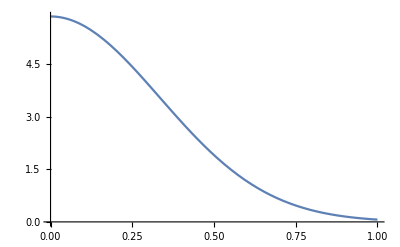

```mathematica
Plot[FUU["pi+",0.1,0.3,1,PT],{PT,0,1}]
```

HERMES data

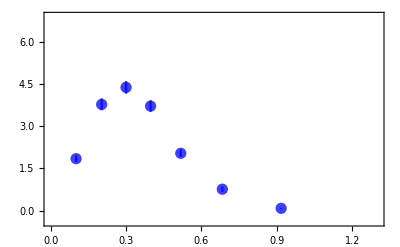

```mathematica
Clear[data,tab];
data=Cases[Import["./data/hermes.proton.zxpt-3D.vmsub.mults_piplus.list","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[8]],data[[i]][[2]]},ErrorBar[Sqrt[data[[i]][[3]]^2+data[[i]][[4]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMES=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.3},{-0.4,6.9}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]},{Blue,PointSize[0.02],Opacity[0.5]}}(*,PlotLegends->Placed[{"π^+ PRL"},{0.6,0.9}]*)]
```

```mathematica
PlotHERMES[func_,pion_,data_,color_] := {
npt = Length[data];
plot = Table[{0,0},npt];
For[i=1,i≤npt,i++,
x = data[[i]][[6]];
z = data[[i]][[7]] ;
Q2 = data[[i]][[5]] ;
PT = data[[i]][[8]] ;


plot[[i,1]] =  PT;
plot[[i,2]] =  func[pion,x,z,Q2,PT];



];

ListPlot[{plot},PlotStyle->{{color, Thick}},Frame-> False,PlotStyle->None, Joined-> True,InterpolationOrder->4,Frame-> True]
};
```

```mathematica
F2[x_,Q2_] := (4.0/9.0)f1u[x,Q2]  +(1.0/9.0)f1d[x,Q2] +(1.0/9.0)f1s[x,Q2]   + (4.0/9.0)f1ubar[x,Q2] +(1.0/9.0)f1dbar[x,Q2]  +(1.0/9.0)f1sdbar[x,Q2]
```

```mathematica
MULT[pion_,x_,z_,Q2_,PT_] :=2 π PT FUU[pion,x,z,Q2,PT]/F2[x,Q2]  ;
```

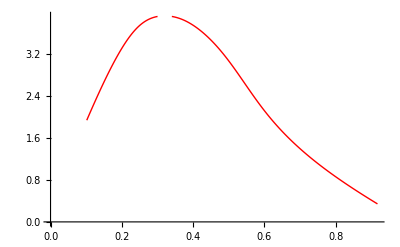

```mathematica
plotHERMES = PlotHERMES[MULT,"pi+",data,Red]
```

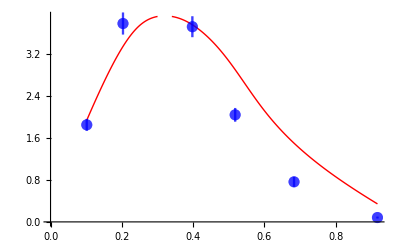

```mathematica
Show[plotHERMES,plotdataHERMES]
```

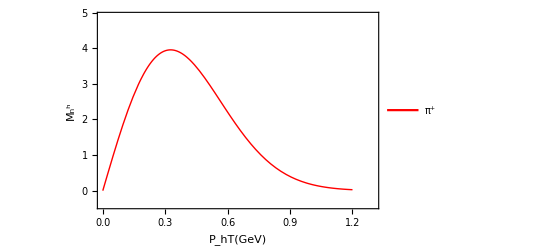

```mathematica
plotHERMESpip = Plot[MULT["pi+",0.1522067,0.2233066,2.87544,PT],{PT,0,1.2},Frame-> True,PlotRange->{{0,1.3},{-0.4,4.9}}, PlotStyle->{Thick,Red},FrameLabel->{"P_hT(GeV)","M_n^h"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+"},{0.6,0.9}]]
```

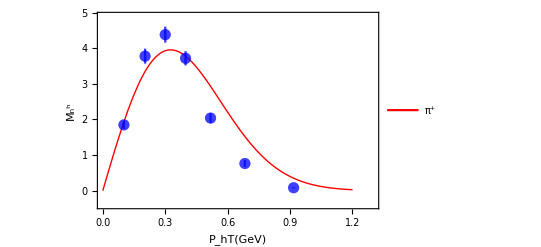

```mathematica
Show[plotHERMESpip,plotdataHERMES]
```

```mathematica
Export["../tex/figs/hermes_pip.pdf",%,Background->None]
```

../tex/figs/hermes_pip.pdf

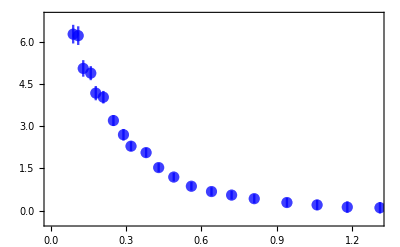

```mathematica
Clear[data,tab];
data=Cases[Import["./data/compass_deuteron_hplus.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[7]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASS=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.3},{-0.4,6.9}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]},{Blue,PointSize[0.02],Opacity[0.5]}}]
```

```mathematica
FUUneutron[pion_,x_,z_,Q2_,PT_] := ((4.0/9.0)f1d[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1u[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1dbar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1ubar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sdbar[x,Q2]D1sbar[pion,z,Q2])Exp[(-PT^2/avPT[z])]/(π avPT[z])
```

```mathematica
F2neutron[x_,Q2_] := (4.0/9.0)f1d[x,Q2]  +(1.0/9.0)f1u[x,Q2] +(1.0/9.0)f1s[x,Q2]   + (4.0/9.0)f1dbar[x,Q2] +(1.0/9.0)f1ubar[x,Q2]  +(1.0/9.0)f1sdbar[x,Q2]
```

```mathematica
MULTCOMPASS[pion_,x_,z_,Q2_,PT2_] :=π  (FUU[pion,x,z,Q2,Sqrt[PT2]]+FUUneutron[pion,x,z,Q2,Sqrt[PT2]])/(F2[x,Q2]+F2neutron[x,Q2])  ;
```

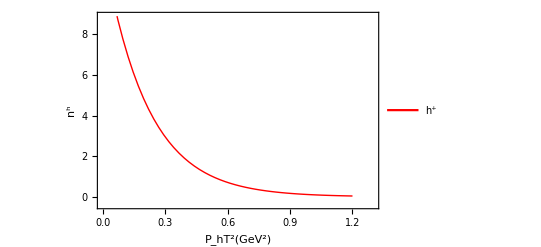

```mathematica
plotCOMPASSpip = Plot[MULTCOMPASS["pi+",0.157,0.2,20,PT],{PT,0,1.2},Frame-> True,PlotRange->{{0,1.3},{-0.4,8.9}}, PlotStyle->{Thick,Red},FrameLabel->{"P_hT^2(GeV^2)","n^h"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"h^+"},{0.6,0.9}]]
```

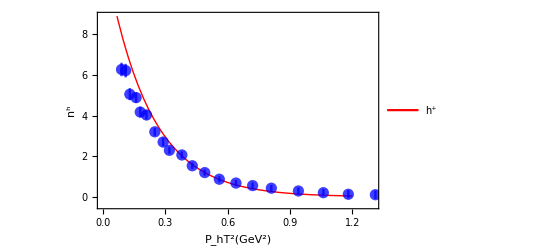

```mathematica
Show[plotCOMPASSpip,plotdataCOMPASS]
```

```mathematica
Export["../tex/figs/compass_hp.pdf",%,Background->None]
```

../tex/figs/compass_hp.pdf

```mathematica
Clear[data,tab, x, z, Q2, PT];
```

## P_hT-dependence of CLAS data (NEW)

```mathematica
avPT2JLab:= 0.17;


FUUonlyPTdep[PT2_] := Exp[(-PT2/avPT2JLab)]/(π avPT2JLab)
```

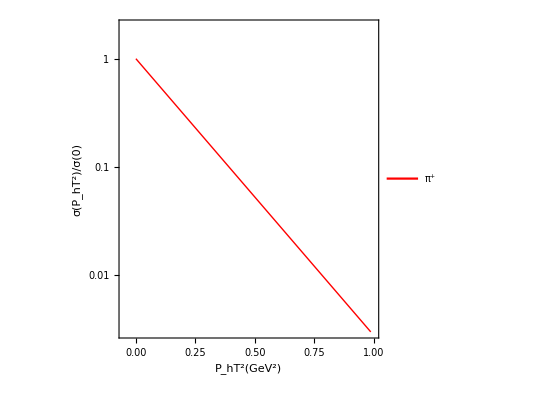

```mathematica
subtics[j_]:=Table[{i*10^j," ",{0.007,0}},{i,2,9,1}];

customizeLogTicksL=Join[
subtics[-3],{{10^-2,"10^-2"}},
subtics[-2],{{10^-1,"10^-1"}},
subtics[-1],{{10^0,"10^0"}}];

customizeLogTicksR=Join[
subtics[-3],{{10^-2," "}},
subtics[-2],{{10^-1," "}},
subtics[-1],{{10^0," "}}];

plotJLabpip = LogPlot[If[PT2≥0,FUUonlyPTdep[PT2]/FUUonlyPTdep[0]," "],{PT2,-1,1},
Frame-> True,PlotRange->{{-0.05,1},{3*10^-3,2}}, PlotStyle->{Thick,Red},AspectRatio->1,FrameLabel->{"P_hT^2(GeV^2)","σ(P_hT^2)/σ(0)"},BaseStyle->{FontSize->16,FontFamily->"Arial"},PlotLegends->Placed[{"π^+"},{0.7,0.9}],
FrameTicks->{{customizeLogTicksL,customizeLogTicksR},{Automatic,Automatic}}]
```

JLab data (problematic: should use Needs[“ErrorBarLogPlots`”] but this seems to have worked only in mathematica 6....)

```mathematica
Clear[data,tab];
data=Cases[Import["./data/data-JLAB-Osipenko-Fig14","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[2]]},ErrorBar[data[[i]][[3]]^2]},{i,Length[data]},{j,1}];
plotdataHERMES=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.3},{0,1}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]},{Blue,PointSize[0.02],Opacity[0.5]}}(*,PlotLegends->Placed[{"π^+ PRL"},{0.6,0.9}]*)]
```

-Graphics-

(work around)

```mathematica
PlotOsipenkoPoints= ListLogPlot[ Table[{data[[i]][[1]],data[[i]][[2]]},{i,Length[data]}],PlotStyle-> {Blue,PointSize[0.025]}]
```

ListLogPlot[{},PlotStyle→{RGBColor[0, 0, 1],PointSize[0.025]}]

```mathematica
eps:=0.0001
PlotOsipenkoError=Table[ ListLogPlot[ Table[{
{data[[i]][[1]],           data[[i]][[2]]+data[[i]][[3]]},
{data[[i]][[1]]-eps,data[[i]][[2]]+data[[i]][[3]]},
{data[[i]][[1]]+eps,data[[i]][[2]]+data[[i]][[3]]},
{data[[i]][[1]],           data[[i]][[2]]+data[[i]][[3]]},
{data[[i]][[1]],           data[[i]][[2]]-data[[i]][[3]]},
{data[[i]][[1]]-eps,data[[i]][[2]]-data[[i]][[3]]},
{data[[i]][[1]]+eps,data[[i]][[2]]-data[[i]][[3]]},
{data[[i]][[1]],           data[[i]][[2]]-data[[i]][[3]]}
},{i,jj,jj,1}],Joined->True,PlotStyle->Blue],{jj,1,Length[data]}]
```

{}

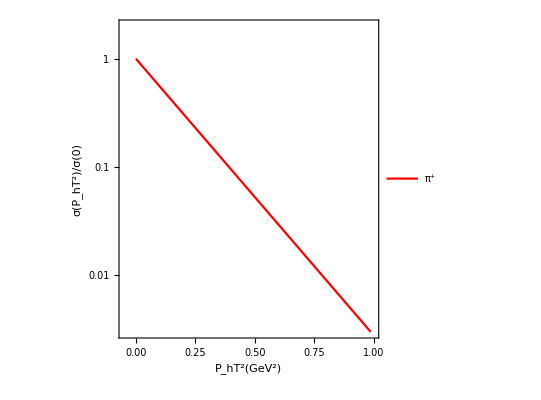
Show[-Graphics-,ListLogPlot[{},PlotStyle→{RGBColor[0, 0, 1],PointSize[0.025]}],{}]

```mathematica
Show[plotJLabpip ,PlotOsipenkoPoints,PlotOsipenkoError]
```

```mathematica
Export["../tex/figs/Fig02a-JLab-ratio-pT-v5-NEW.pdf",%,Background->None]
```

../tex/figs/Fig02a-JLab-ratio-pT-v5-NEW.pdf

```mathematica
Clear[data,tab, x, z, Q2, PT];
```

Phenomenology of leading twist double spin asymmetry A_LL

## F_LL analytical result:

```mathematica
Print["Eq(2.18 b)  C[g1 D1]"]
PTweightLL[pt_] := 1;
```

Eq(2.18 b)  C[g1 D1]

```mathematica
Print["Eq(2.18 b)   C[g1 D1]"]
ConvolutionTMD[omega0,g1,D1]
```

Eq(2.18 b)   C[g1 D1]

(D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1^2 z^2)) g_1)/(π p_TA^2+k_Tg1^2 π z^2)

```mathematica
Print["Eq(4.9) ∫ⅆ^2P_hT C[g1 D1]"]
PTConvolutionTMD[PTweightLL,omega0,g1,D1]
```

Eq(4.9) ∫ⅆ^2P_hT C[g1 D1]

D_1 g_1

## F_LL numerics:

```mathematica
avLLPT[z_]:= avp+avkg z^2;


FLL[pion_,x_,z_,Q2_,PT_] := ((4.0/9.0)g1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1sbar[x,Q2] D1sbar[pion,z,Q2] ) Exp[(-PT^2/avLLPT[z])]/(π avLLPT[z])


FLLIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)g1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1sbar[x,Q2] D1sbar[pion,z,Q2])
```

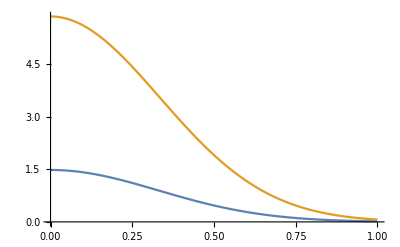

```mathematica
Plot[{FLL["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_LL numerics:

```mathematica
sjlab = Mp^2 + 2 5.7 Mp;  
y[Q2_,x_] :=  Q2/(sjlab x);

ALL[pion_,x_,z_,Q2_,PT_] := (y[Q2,x](2- y[Q2,x] )FLL[pion,x,z,Q2,PT])/((1+(1-y[Q2,x])^2)FUU[pion,x,z,Q2,PT])  ;

ALLIntegrated[pion_,x_,z_,Q2_] := (y[Q2,x](2- y[Q2,x] )FLLIntegrated[pion,x,z,Q2])/((1+(1-y[Q2,x])^2)FUUIntegrated[pion,x,z,Q2]);
```

```mathematica
PlotG1[func_,pion_,data_,color_] := {
npt = Length[data];
plot = Table[{0,0},npt];
For[i=1,i≤npt,i++,
x = data[[i]][[1]];
z = data[[i]][[3]] ;
Q2 = data[[i]][[2]] ;
PT = data[[i]][[4]] ;


plot[[i,1]] =  PT;
plot[[i,2]] =  func[pion,x,z,Q2,PT];



];

ListPlot[{plot},PlotStyle->{{color, Thick}},Frame-> False,PlotStyle->None, Joined-> True,InterpolationOrder->4,Frame-> True]
};
```

#### Jlab pi+ ALL

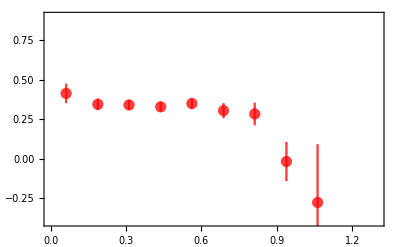

```mathematica
Clear[data,tab];
data=Cases[Import["./data/g1_jlab_pip_pt.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[4]],data[[i]][[5]]},ErrorBar[Sqrt[data[[i]][[6]]^2+data[[i]][[7]]^2]]},{i,Length[data]},{j,1}];
plotdataALLpipPRL=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.3},{-0.4,0.9}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]},{Red,PointSize[0.02],Opacity[0.5]}}(*,PlotLegends->Placed[{"π^+ PRL"},{0.6,0.9}]*)]
```

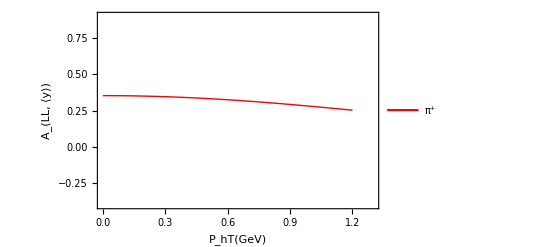

```mathematica
plotALLpip = Plot[ALL["pi+",0.257,0.504,1.667,PT],{PT,0,1.2},Frame-> True,PlotRange->{{0,1.3},{-0.4,0.9}}, PlotStyle->{Thick,Red},FrameLabel->{"P_hT(GeV)","A_(LL, ⟨y⟩)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+"},{0.6,0.9}]]
```

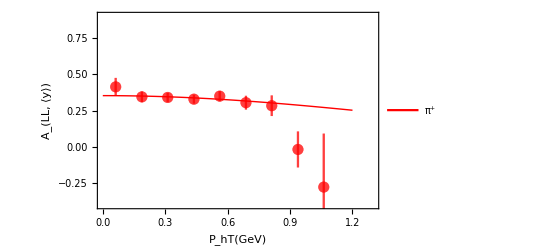

```mathematica
Show[plotALLpip,plotdataALLpipPRL]
```

```mathematica
Export["../tex/figs/all_jlab_pip.pdf",%,Background->None]
```

../tex/figs/all_jlab_pip.pdf

#### Jlab pi- ALL

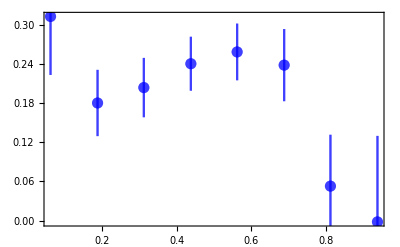

```mathematica
Clear[data,tab];
data=Cases[Import["./data/g1_jlab_pim_pt.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[4]],data[[i]][[5]]},ErrorBar[Sqrt[data[[i]][[6]]^2+data[[i]][[7]]^2]]},{i,Length[data]},{j,1}];
plotdataALLpim=ErrorListPlot[tab, Frame-> True,PlotRange->{All,All}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]},{Blue,PointSize[0.02],Opacity[0.5]}}]
```

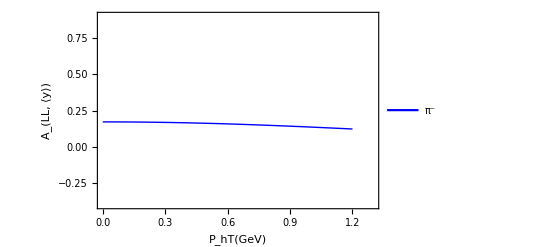

```mathematica
plotALLpim =  Plot[ALL["pi-",0.257,0.504,1.667,PT],{PT,0,1.2},Frame-> True,PlotRange->{{0,1.3},{-0.4,0.9}}, PlotStyle->{Thick,Blue},FrameLabel->{"P_hT(GeV)","A_(LL, ⟨y⟩)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^-"},{0.6,0.9}]]
```

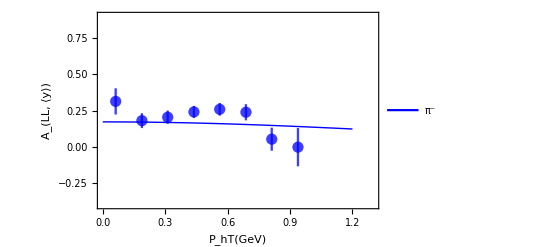

```mathematica
Show[plotALLpim,plotdataALLpim]
```

```mathematica
Export["../tex/figs/all_jlab_pim.pdf",%,Background->None]
```

../tex/figs/all_jlab_pim.pdf

#### Jlab pi0 ALL

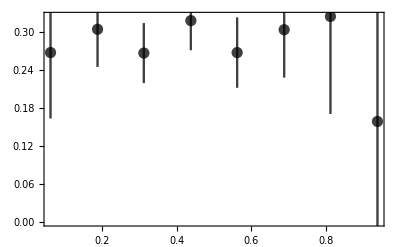

```mathematica
Clear[data,tab];
data=Cases[Import["./data/g1_jlab_pi0_pt.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[4]],data[[i]][[5]]},ErrorBar[Sqrt[data[[i]][[6]]^2+data[[i]][[7]]^2]]},{i,Length[data]},{j,1}];
plotdataALLpi0=ErrorListPlot[tab, Frame-> True,PlotRange->{All,All}, PlotStyle->{{Black,PointSize[0.02],Opacity[0.5]}},PlotRange->{{0,1.3},{-0.4,0.9}}]
```

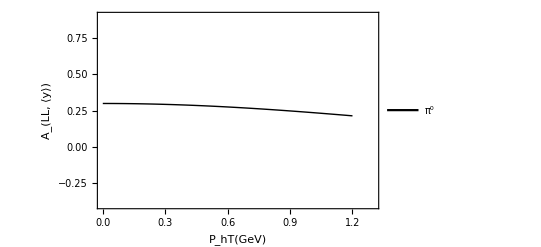

```mathematica
plotALLpi0 =  Plot[ALL["pi0",0.257,0.504,1.667,PT],{PT,0,1.2},Frame-> True,PlotRange->{{0,1.3},{-0.4,0.9}}, PlotStyle->{Thick,Black},FrameLabel->{"P_hT(GeV)","A_(LL, ⟨y⟩)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^0"},{0.6,0.9}]]
```

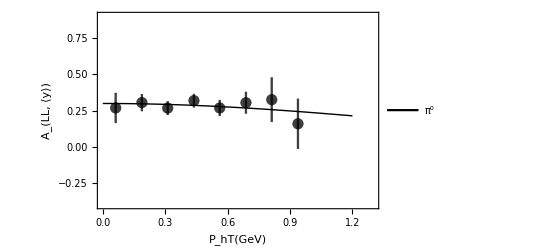

```mathematica
Show[plotALLpi0,plotdataALLpi0]
```

```mathematica
Export["../tex/figs/all_jlab_pi0.pdf",%,Background->None]
```

../tex/figs/all_jlab_pi0.pdf

Phenomenology of leading twist single spin asymmetry A_UT^sin[Φ_h-Φ_S]Sivers Asymmetry

## F_UT^sin[Φ_h-Φ_S] analytical result:

```mathematica
Print["Eq(2.18 d)  C[ -(h̄)/M f_(1  T)^perp D_1]"  ]
omega1B[kt_,PhT_,phi_] := (kt Cos[phi])/M;
PTweightUTf1tperp[kt_] := 1;
```

Eq(2.18 d)  C[ -(h̄)/M f_(1  T)^perp D_1]

```mathematica
Print["Eq(2.18 d)  F_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ -(h̄)/M f_(1  T)^perp D_1] ="  ]
-ConvolutionTMD[omega1B,f1Tperp,D1]
```

Eq(2.18 d)  F_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ -(h̄)/M f_(1  T)^perp D_1] =

-(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_TSIVERS^2 z^2)) f_T^(FIRST perp) M P_hT z)/(π (p_TA^2+k_TSIVERS^2 z^2)^2)

```mathematica
Print["Eq(2.18 d)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ -(h̄)/M f_(1  T)^perp D_1] ="  ]
-PTConvolutionTMD[PTweightUTf1tperp,omega1B,f1Tperp,D1]
```

Eq(2.18 d)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ -(h̄)/M f_(1  T)^perp D_1] =

-D_1 f_T^(FIRST perp) M √π z √(1/(p_TA^2+k_TSIVERS^2 z^2))

## F_UT^sin[Φ_h-Φ_S] numerics:

```mathematica
avUTPTf1tperp[z_]:= avp+avks z^2;

GUTf1tperp[z_,PT_] := -Mp^2/(π avUTPTf1tperp[z]^2) Exp[(-PT^2/avUTPTf1tperp[z])]
AUTf1tperp[z_] := -(Mp z √π)/(√avUTPTf1tperp[z])  

FUTf1tperp[pion_,x_,z_,Q2_,PT_] := (2z PT)/Mp((4.0/9.0)f1TperpuFirstMoment[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1TperpdFirstMoment[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1TperpsFirstMoment[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1TperpubarFirstMoment[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1TperpdbarFirstMoment[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1TperpsbFirstMoment[x,Q2] D1sbar[pion,z,Q2] ) GUTf1tperp[z,PT]


FUTf1tperpIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)f1TperpuFirstMoment[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1TperpdFirstMoment[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1TperpsFirstMoment[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1TperpubarFirstMoment[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1TperpdbarFirstMoment[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1TperpsbFirstMoment[x,Q2] D1sbar[pion,z,Q2] ) AUTf1tperp[z]
```

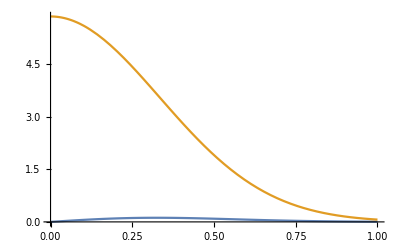

```mathematica
Plot[{FUTf1tperp["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UT^sin[Φ_h-Φ_S]numerics:

```mathematica
AUTSivers[pion_,x_,z_,Q2_,PT_] := FUTf1tperp[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUTSiversIntegrated[pion_,x_,z_,Q2_] := FUTf1tperpIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of PT dependence

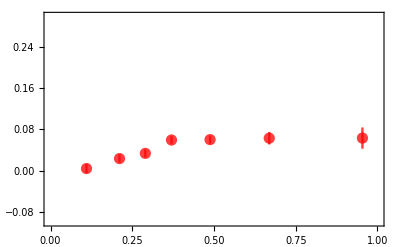

```mathematica
Clear[data,tab];
data=Cases[Import["./data/sivers_aut_pip_pt_09.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[6]],data[[i]][[7]]},ErrorBar[Sqrt[data[[i]][[8]]^2+data[[i]][[9]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}(*,PlotLegends->Placed[{"π^+ PRL"},{0.6,0.9}]*)]
```

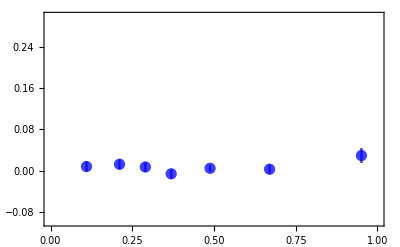

```mathematica
Clear[data,tab];
data=Cases[Import["./data/sivers_aut_pim_pt_09.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[6]],data[[i]][[7]]},ErrorBar[Sqrt[data[[i]][[8]]^2+data[[i]][[9]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}(*,PlotLegends->Placed[{"π^+ PRL"},{0.6,0.9}]*)]
```

```mathematica
AUTSiverspimfuncPT[PT_] :=AUTSivers["pi-",0.1,0.34,2.4, PT];
AUTSiverspipfuncPT[PT_] :=AUTSivers["pi+",0.1,0.34,2.4, PT];
```

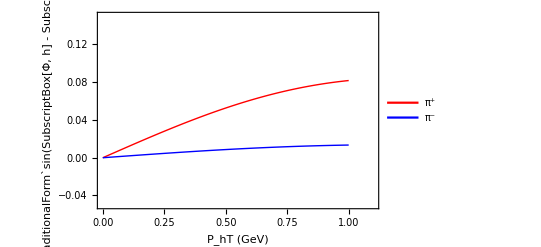

```mathematica
AUTSiverspipplotPT = Plot[{AUTSiverspipfuncPT[PT],AUTSiverspimfuncPT[PT]},{PT,0,1.},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1.1},{-0.05,0.15}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT (GeV)","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.85}]]
```

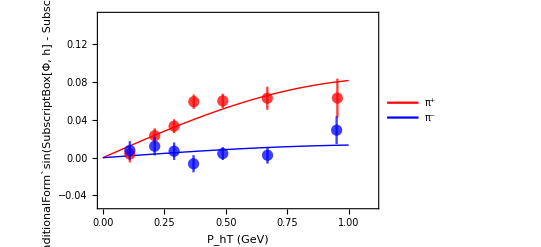

```mathematica
Show[AUTSiverspipplotPT,plotdataHERMESpip,plotdataHERMESpim]
```

```mathematica
Export["../tex/figs/AUTSivers_PT.pdf",%,Background->None]
```

../tex/figs/AUTSivers_PT.pdf

### Plot of x dependence

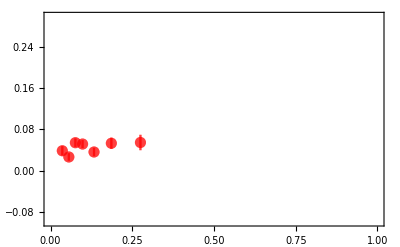

```mathematica
Clear[data,tab];
data=Cases[Import["./data/sivers_aut_pip_x_09.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[3]],data[[i]][[7]]},ErrorBar[Sqrt[data[[i]][[8]]^2+data[[i]][[9]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

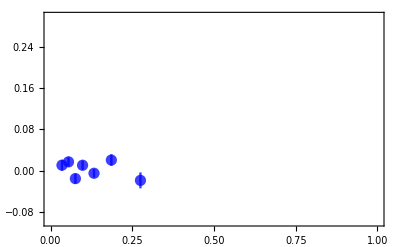

```mathematica
Clear[data,tab];
data=Cases[Import["./data/sivers_aut_pim_x_09.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[3]],data[[i]][[7]]},ErrorBar[Sqrt[data[[i]][[8]]^2+data[[i]][[9]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

```mathematica
(*AUTSiverspipfunc[x_] :=AUTSivers["pi+",x,0.34,2.4, 0.4];*)AUTSiverspipfunc[x_] :=AUTSiversIntegrated["pi+",x,0.34,2.4];
```

```mathematica
(*AUTSiverspimfunc[x_] :=AUTSivers["pi-",x,0.34,2.4, 0.4];*)AUTSiverspimfunc[x_] := AUTSiversIntegrated["pi-",x,0.34,2.4];
```

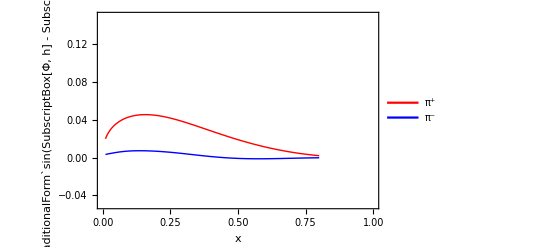

```mathematica
AUTSiverspipplot = Plot[{AUTSiverspipfunc[x] ,AUTSiverspimfunc[x] },{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.15}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.7}]]
```

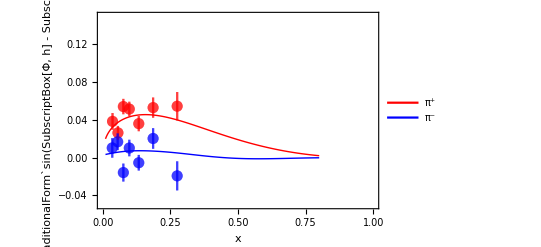

```mathematica
Show[AUTSiverspipplot,plotdataHERMESpip,plotdataHERMESpim]
```

```mathematica
Export["../tex/figs/AUTSivers_x.pdf",%,Background->None]
```

../tex/figs/AUTSivers_x.pdf

Phenomenology of leading twist single spin asymmetry A_UT^sin[Φ_h+Φ_S]Collins Asymmetry

## F_UT^sin[Φ_h+Φ_S] analytical result:

```mathematica
Print["Eq(2.18 c)  C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp]"  ]
omega1A[kt_,PhT_,phi_] := (PhT - z kt Cos[phi])/(z Mhadron);
PTweightUTh1[kt_] := 1;
```

Eq(2.18 c)  C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp]

```mathematica
Print["Eq(2.18 c)  F_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] + SubscriptBox[Φ, S]])= C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp] ="  ]
ConvolutionTMD[omega1A,h1,H1perp]
```

Eq(2.18 c)  F_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] + SubscriptBox[Φ, S]])= C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp] =

(2 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_Th1^2 z^2)) H_1^(FIRST perp) hh_1 M_hadron P_hT z)/(π (p_TCOLLINS^2+k_Th1^2 z^2)^2)

```mathematica
Print["Eq(2.18 c)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] + SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp] ="  ]
PTConvolutionTMD[PTweightUTh1,omega1A,h1,H1perp]
```

Eq(2.18 c)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] + SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp] =

(H_1^(FIRST perp) hh_1 M_hadron √π z)/(√(p_TCOLLINS^2+k_Th1^2 z^2))

## F_UT^sin[Φ_h+Φ_S] numerics:

```mathematica
avUTPTh1[z_]:= avp MC^2/(avp+MC^2)+avk z^2;

GUTh1[z_,PT_] := Mp^2/(π avUTPTh1[z]^2) Exp[(-PT^2/avUTPTh1[z])]
AUTh1[z_] := (Mh z √π)/(√avUTPTh1[z])  

FUTh1[pion_,x_,z_,Q2_,PT_] := (2z PT Mh)/Mp^2((4.0/9.0)h1u[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1d[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) GUTh1[z,PT]


FUTh1Integrated[pion_,x_,z_,Q2_] := ((4.0/9.0)h1u[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1d[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) AUTh1[z]
```

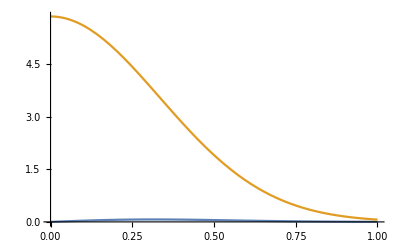

```mathematica
Plot[{FUTh1["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UT^sin[Φ_h+Φ_S]numerics:

```mathematica
AUTCollins[pion_,x_,z_,Q2_,PT_] := FUTh1[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUTCollinsIntegrated[pion_,x_,z_,Q2_] := FUTh1Integrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of PT dependence

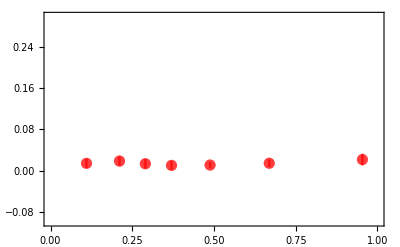

```mathematica
Clear[data,tab];
data=Cases[Import["./data/collins_aut_pip_pt_lba_10.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[5]],data[[i]][[6]]},ErrorBar[Sqrt[data[[i]][[7]]^2+data[[i]][[8]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

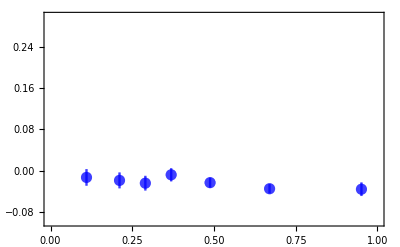

```mathematica
Clear[data,tab];
data=Cases[Import["./data/collins_aut_pim_pt_lba_10.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[5]],data[[i]][[6]]},ErrorBar[Sqrt[data[[i]][[7]]^2+data[[i]][[8]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

```mathematica
AUTCollinspimfuncPT[PT_] :=AUTCollins["pi-",0.1,0.34,2.4, PT];
AUTCollinspipfuncPT[PT_] :=AUTCollins["pi+",0.1,0.34,2.4, PT];
```

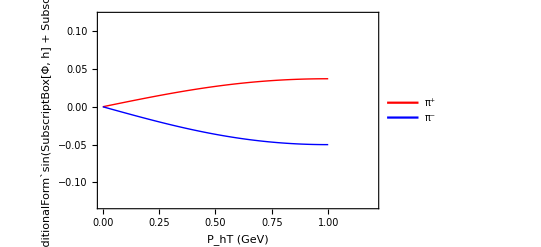

```mathematica
AUTCollinspipplotPT = Plot[{AUTCollinspipfuncPT[PT],AUTCollinspimfuncPT[PT]},{PT,0,1.},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1.2},{-0.13,0.12}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT (GeV)","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] + SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

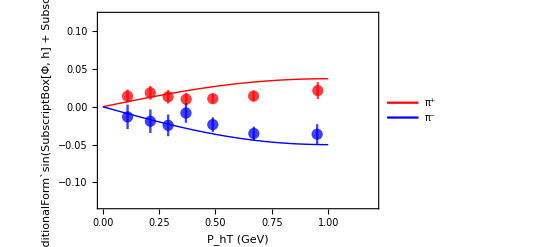

```mathematica
Show[AUTCollinspipplotPT,plotdataHERMESpip,plotdataHERMESpim]
```

```mathematica
Export["../tex/figs/AUTCollins_PT.pdf",%,Background->None]
```

../tex/figs/AUTCollins_PT.pdf

### Plot of x dependence

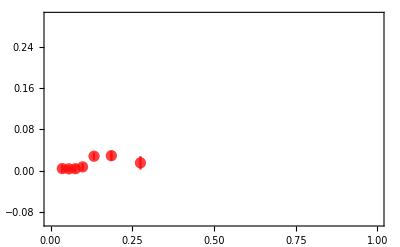

```mathematica
Clear[data,tab];
data=Cases[Import["./data/collins_aut_pip_x_lba_10.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[2]],data[[i]][[6]]},ErrorBar[Sqrt[data[[i]][[7]]^2+data[[i]][[8]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

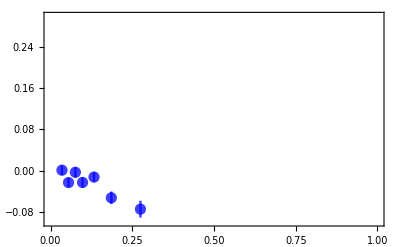

```mathematica
Clear[data,tab];
data=Cases[Import["./data/collins_aut_pim_x_lba_10.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[2]],data[[i]][[6]]},ErrorBar[Sqrt[data[[i]][[7]]^2+data[[i]][[8]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

```mathematica
AUTXCollinspipfunc[x_] :=AUTCollinsIntegrated["pi+",x,0.34,2.4];
```

```mathematica
AUTCollinspimfunc[x_] :=AUTCollinsIntegrated["pi-",x,0.34,2.4];
```

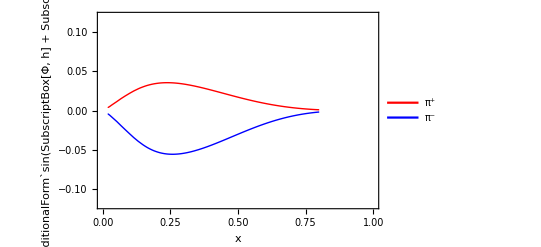

```mathematica
AUTCollinspipplot = Plot[{AUTXCollinspipfunc[x] ,AUTCollinspimfunc[x] },{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.12,0.12}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] + SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.7}]]
```

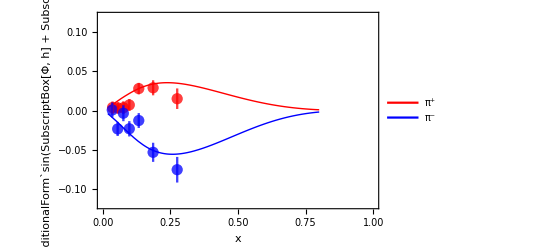

```mathematica
Show[AUTCollinspipplot,plotdataHERMESpip,plotdataHERMESpim]
```

```mathematica
Export["../tex/figs/AUTCollins_x.pdf",%,Background->None]
```

../tex/figs/AUTCollins_x.pdf

Phenomenology of leading twist single spin asymmetry A_UT^sin[3 Φ_h-Φ_S]Pretzelosity  Asymmetry

## F_UT^sin[3 Φ_h-Φ_S] analytical result:

```mathematica
Print["Eq(2.18 h)  C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp]"  ]  
omega3[kt_,PhT_,phi_] := -1/(2z M^2 Mhadron)(2 kt Cos[phi] (kt PhT Cos[phi] - z kt kt) + kt^2(PhT - z kt Cos[phi]) - 4 (kt Cos[phi])^2 (PhT - z kt Cos[phi]));
PTweightUTh1tp[PhT_] :=1;
```

Eq(2.18 h)  C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp]

```mathematica
Print["Eq(2.18 h)  F_UT^(TraditionalForm`sin[3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp] ="  ]
ConvolutionTMD[omega3,h1Tperp,H1perp]
```

Eq(2.18 h)  F_UT^(TraditionalForm`sin[3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp] =

(2 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_TPRETZELOSITY^2 z^2)) H_1^(FIRST perp) h_T^(perp Second) M^2 M_hadron P_hT^3 z^3)/(π (p_TCOLLINS^2+k_TPRETZELOSITY^2 z^2)^4)

```mathematica
Print["Eq(2.18 h)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp] ="  ]
PTConvolutionTMD[PTweightUTh1tp,omega3,h1Tperp,H1perp]
```

Eq(2.18 h)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp] =

(3 H_1^(FIRST perp) h_T^(perp Second) M^2 M_hadron √π z^3)/(2 (p_TCOLLINS^2+k_TPRETZELOSITY^2 z^2)^(3/2))

## F_UT^sin[3 Φ_h-Φ_S] numerics:

```mathematica
avkP = avk MTT^2/(avk+MTT^2);
avUTPTh1tp[z_]:= avp MC^2/(avp+MC^2)+avkP z^2;

GUTh1tp[z_,PT_] := (Mp^4 Mh)/(π avUTPTh1tp[z]^4) Exp[(-PT^2/avUTPTh1tp[z])]
AUTh1tp[z_] := (3 Mh Mp^2 z^3 √π)/(2 √(avUTPTh1tp[z]^3))  

FUTh1tp[pion_,x_,z_,Q2_,PT_] := (2 z^3 PT^3)/Mp^2((4.0/9.0)h1TperpuSecondMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1TperpdSecondMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) GUTh1tp[z,PT]


FUTh1tpIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)h1TperpuSecondMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1TperpdSecondMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) AUTh1tp[z]
```

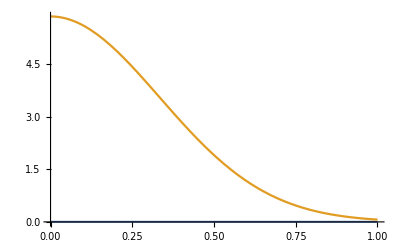

```mathematica
Plot[{FUTh1tp["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UT^sin[3 Φ_h-Φ_S]numerics:

```mathematica
AUTh1tp[pion_,x_,z_,Q2_,PT_] := FUTh1tp[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUTh1tpIntegrated[pion_,x_,z_,Q2_] := FUTh1tpIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of PT dependence

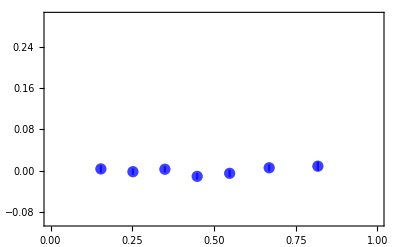

```mathematica
Clear[data,tab];
data=Cases[Import["./data/pretzelosity_compass_proton_hm_pt_13.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[5]],data[[i]][[6]]},ErrorBar[data[[i]][[7]]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

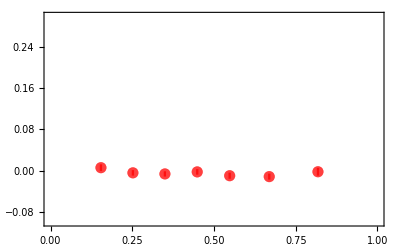

```mathematica
Clear[data,tab];
data=Cases[Import["./data/pretzelosity_compass_proton_hp_pt_13.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[5]],data[[i]][[6]]},ErrorBar[data[[i]][[7]]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

```mathematica
AUTh1tppimfuncPT[PT_] :=AUTh1tp["pi-",0.05,0.35,3.6, PT];
AUTh1tppipfuncPT[PT_] :=AUTh1tp["pi+",0.05,0.35,3.6, PT];
```

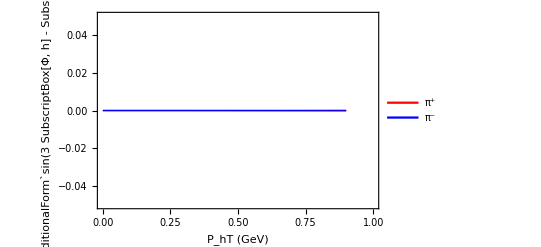

```mathematica
AUTh1tppipplotPT = Plot[{AUTh1tppipfuncPT[PT],AUTh1tppimfuncPT[PT]},{PT,0,0.9},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT (GeV)","A_UT^(TraditionalForm`sin(3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

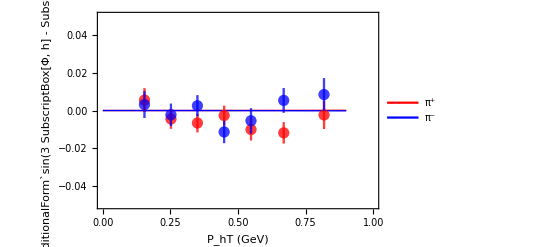

```mathematica
Show[AUTh1tppipplotPT,plotdataCOMPASSpip,plotdataCOMPASSpim]
```

```mathematica
Export["../tex/figs/AUTPretzelosity_PT.pdf",%,Background->None]
```

../tex/figs/AUTPretzelosity_PT.pdf

### Plot of x dependence

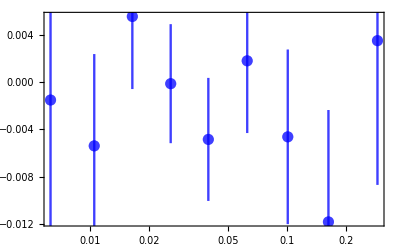

```mathematica
Clear[data,tab];
data=Cases[Import["./data/pretzelosity_compass_proton_hm_x_13.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[6]]},ErrorBar[data[[i]][[7]]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpim=ErrorListLogLinearPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

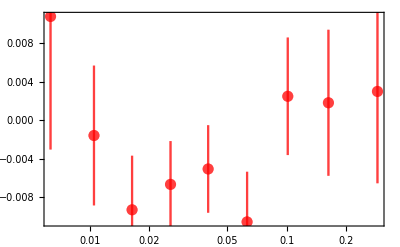

```mathematica
Clear[data,tab];
data=Cases[Import["./data/pretzelosity_compass_proton_hp_x_13.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[6]]},ErrorBar[data[[i]][[7]]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpip=ErrorListLogLinearPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

```mathematica
AUTh1tppipfunc[x_] :=AUTh1tpIntegrated["pi+",x,0.35,3.6];
```

```mathematica
AUTh1tppimfunc[x_] :=AUTh1tpIntegrated["pi-",x,0.35,3.6];
```

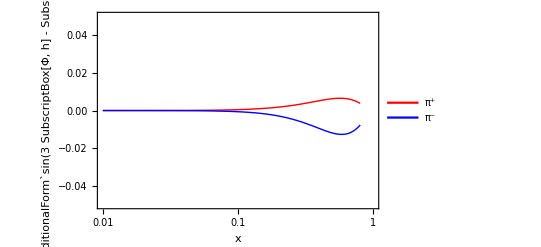

```mathematica
AUTh1tppipplot = LogLinearPlot[{AUTh1tpIntegrated["pi+",x,0.54,2.4],AUTh1tpIntegrated["pi-",x,0.54,2.4]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.78}]]
```

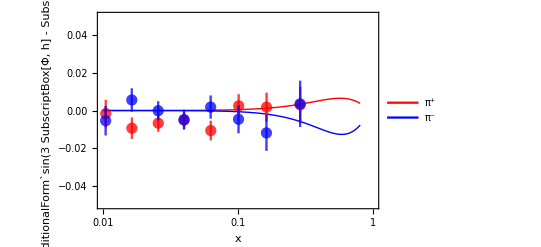

```mathematica
Show[AUTh1tppipplot,plotdataCOMPASSpip,plotdataCOMPASSpim]
```

```mathematica
Export["../tex/figs/AUTPretzelosity_x.pdf",%,Background->None]
```

../tex/figs/AUTPretzelosity_x.pdf

Phenomenology of leading twist single spin asymmetry A_UU^cos[2 Φ_h]Boer-Mulders Asymmetry

## F_UU^cos[2 Φ_h] analytical result:

```mathematica
Print["Eq(2.18 f)  C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp]"  ]
omega2A[kt_,PhT_,phi_] := 1/(z M Mhadron)(2 kt Cos[phi] (PhT - z kt Cos[phi]));
omega2B[kt_,PhT_,phi_] := 1/(z M Mhadron)(-kt PhT Cos[phi] + z kt kt);

omega2AB[kt_,PhT_,phi_] := omega2A[kt,PhT,phi]+omega2B[kt,PhT,phi];
PTweightUTh1perp[kt_] := 1;
```

Eq(2.18 f)  C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp]

```mathematica
Print["Eq(...)  F_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])= C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp] ="  ]
ConvolutionTMD[omega2AB,h1perp,H1perp]
```

Eq(...)  F_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])= C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_BOERMULDERS^2 z^2)) H_1^(FIRST perp) h_1^(FIRST perp) M M_hadron P_hT^2 z^2)/(π (p_TCOLLINS^2+k_BOERMULDERS^2 z^2)^3)

```mathematica
Print["Eq(...)  ∫ⅆ^2P_hTF_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])=∫ⅆ^2P_hT C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp] ="  ]
PTConvolutionTMD[PTweightUTh1perp,omega2AB,h1perp,H1perp]
```

Eq(...)  ∫ⅆ^2P_hTF_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])=∫ⅆ^2P_hT C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp] =

(4 H_1^(FIRST perp) h_1^(FIRST perp) M M_hadron z^2)/(p_TCOLLINS^2+k_BOERMULDERS^2 z^2)

## F_UU^cos[2 Φ_h] numerics:

```mathematica
avc = MC^2 avp/(MC^2 + avp);
avUUcos2phiPT[z_]:= avc+avkBM z^2;

GfactorUUcos2phi[z_,PT_] := (4 Mp^3 Mh)/(π avUUcos2phiPT[z]^3) Exp[(-PT^2/avUUcos2phiPT[z])]
AfactorUUcos2phi[z_] := (4 Mh Mp z^2)/avUUcos2phiPT[z]  

FUUcos2phi[pion_,x_,z_,Q2_,PT_] := (z^2 PT^2)/Mp^2((4.0/9.0)h1perpuFirstMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2]+(1.0/9.0)h1perpdFirstMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) GfactorUUcos2phi[z,PT]


FUUcos2phiIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)h1perpuFirstMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1perpdFirstMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) AfactorUUcos2phi[z]
```

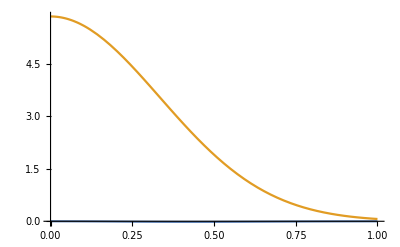

```mathematica
Plot[{FUUcos2phi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UU^cos[2 Φ_h]numerics:

```mathematica
AUUcos2phi[pion_,x_,z_,Q2_,PT_] := FUUcos2phi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUUcos2phiIntegrated[pion_,x_,z_,Q2_] := FUUcos2phiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of pt dependence

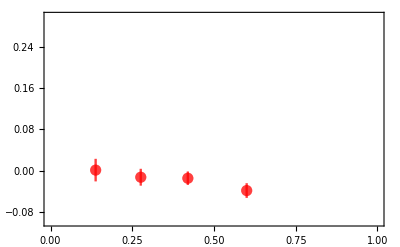

```mathematica
Clear[data,tab];
data=Cases[Import["./data/boermulders_hermes_hp_pt.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[2]]},ErrorBar[Sqrt[data[[i]][[3]]^2+data[[i]][[4]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

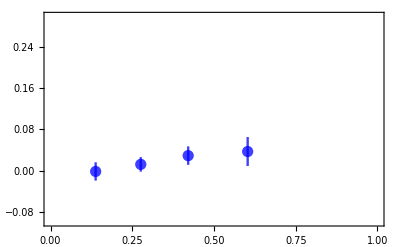

```mathematica
Clear[data,tab];
data=Cases[Import["./data/boermulders_hermes_hm_pt.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[2]]},ErrorBar[Sqrt[data[[i]][[3]]^2+data[[i]][[4]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

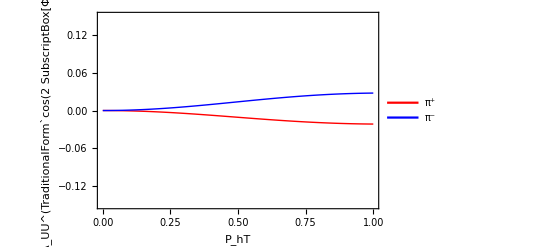

```mathematica
AUTBMlot = Plot[{AUUcos2phi["pi+",0.1,0.34,2.4,PT],AUUcos2phi["pi-",0.1,0.34,2.4,PT]},{PT,0,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.15,0.15}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT","A_UU^(TraditionalForm`cos(2 SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.1,0.7}]]
```

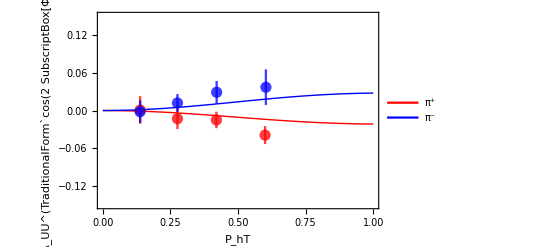

```mathematica
Show[AUTBMlot,plotdataHERMESpip,plotdataHERMESpim]
```

```mathematica
Export["../tex/figs/AUUcos2phi_PT.pdf",%,Background->None]
```

../tex/figs/AUUcos2phi_PT.pdf

### Plot of x dependence

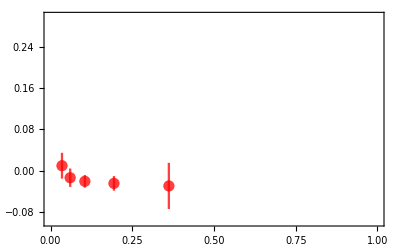

```mathematica
Clear[data,tab];
data=Cases[Import["./data/boermulders_hermes_hp_x.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[2]]},ErrorBar[Sqrt[data[[i]][[3]]^2+data[[i]][[4]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

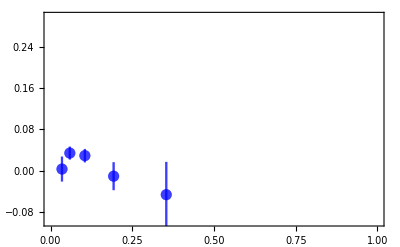

```mathematica
Clear[data,tab];
data=Cases[Import["./data/boermulders_hermes_hm_x.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[2]]},ErrorBar[Sqrt[data[[i]][[3]]^2+data[[i]][[4]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

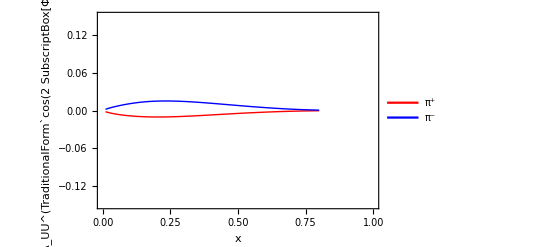

```mathematica
AUTBMlot = Plot[{AUUcos2phiIntegrated["pi+",x,0.34,2.4],AUUcos2phiIntegrated["pi-",x,0.34,2.4]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.15,0.15}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UU^(TraditionalForm`cos(2 SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.7}]]
```

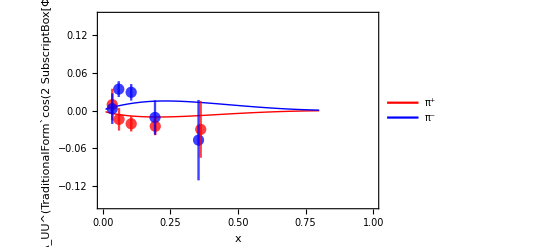

```mathematica
Show[AUTBMlot,plotdataHERMESpip,plotdataHERMESpim]
```

```mathematica
Export["../tex/figs/AUUcos2phi_x.pdf",%,Background->None]
```

../tex/figs/AUUcos2phi_x.pdf

## F_UU^cos[2 Φ_h] twist-4 analytical result:

```mathematica
Print["Eq()  2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1]"  ]
weightUTcos2phi1[kt_,PhT_,phi_] := (2 (kt Cos[phi])^2 - kt kt);
PTweightUTcos2phi1[kt_] := 1;
```

Eq()  2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1]

```mathematica
Print["Eq(...)  F_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])= 2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1] ="  ]
2/Q^2 ConvolutionTMD[weightUTcos2phi1,f1,D1]
```

Eq(...)  F_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])= 2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1] =

(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_TA^2 z^2)) f_1 (k_TA^2)^2 P_hT^2 z^2)/(π Q^2 (p_TA^2+k_TA^2 z^2)^3)

```mathematica
Print["Eq(...)  ∫ⅆ^2P_hTF_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])=∫ⅆ^2P_hT 2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1] ="  ]
2/Q^2 PTConvolutionTMD[PTweightUTcos2phi1,weightUTcos2phi1,f1,D1]
```

Eq(...)  ∫ⅆ^2P_hTF_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])=∫ⅆ^2P_hT 2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1] =

(2 D_1 f_1 (k_TA^2)^2 z^2)/(Q^2 (p_TA^2+k_TA^2 z^2))

Phenomenology of leading twist double spin asymmetry A_LT^cos[Φ_h-Φ_S]

## F_LT^cos[Φ_h-Φ_S] analytical result:

```mathematica
Print["Eq(2.18 e, 4.1a)  C[ (h̄)/M g_(1  T) D_1]"  ]
PTweightLTg1t[kt_] := 1;
```

Eq(2.18 e, 4.1a)  C[ (h̄)/M g_(1  T) D_1]

```mathematica
Print["Eq(2.18 e)  F_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ (h̄)/M g_(1  T) D_1] ="  ]
ConvolutionTMD[omega1B,g1T,D1]
```

Eq(2.18 e)  F_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ (h̄)/M g_(1  T) D_1] =

(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1T^2 z^2)) g_T^FIRST M P_hT z)/(π (p_TA^2+k_Tg1T^2 z^2)^2)

```mathematica
Print["Eq(2.18 e)  F_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ (h̄)/M g_(1  T) D_1] ="  ]
ConvolutionTMD[omega1B,g1T,D1]
```

Eq(2.18 e)  F_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ (h̄)/M g_(1  T) D_1] =

(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1T^2 z^2)) g_T^FIRST M P_hT z)/(π (p_TA^2+k_Tg1T^2 z^2)^2)

```mathematica
Print["Eq(54)  ∫ⅆ^2P_hTF_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ (h̄)/M g_(1  T) D_1] ="  ]
PTConvolutionTMD[PTweightLTg1t,omega1B,g1T,D1]
```

Eq(54)  ∫ⅆ^2P_hTF_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ (h̄)/M g_(1  T) D_1] =

ConditionalExpression[D_1 g_T^FIRST M √π z √(1/(p_TA^2+k_Tg1T^2 z^2)),Re[p_TA^2+k_Tg1T^2 z^2]>0]

## F_LT^cos[Φ_h-Φ_S] numerics:

```mathematica
avkg1T = avkg; (*assumption*)
avLLPT[z_]:= avp+avkg1T z^2;

GLT[z_,PT_] := (2 Mp^2)/(π avLLPT[z]^2) Exp[(-PT^2/avLLPT[z])]
ALT[z_] := (Mp z √π)/(√avLLPT[z])  

FLT[pion_,x_,z_,Q2_,PT_] := (z PT)/Mp((4.0/9.0)g1Tperpu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1Tperpd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1Tperps[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1Tperpubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1Tperpdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1Tperpsbar[x,Q2] D1sbar[pion,z,Q2] ) GLT[z,PT]


FLTIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)g1Tperpu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1Tperpd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1Tperps[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1Tperpubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1Tperpdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1Tperpsbar[x,Q2] D1sbar[pion,z,Q2] ) ALT[z]
```

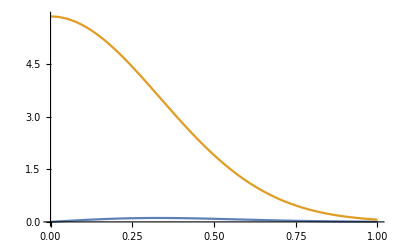

```mathematica
Plot[{FLT["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_LT^cos[Φ_h-Φ_S]numerics:

```mathematica
ALT[pion_,x_,z_,Q2_,PT_] := FLT[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

ALTIntegrated[pion_,x_,z_,Q2_] := FLTIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;
```

```mathematica
ALTCOMpimfunc[x_] :=ALTIntegrated["pi-",x,zcom,Q2com];
ALTCOMpipfunc[x_] :=ALTIntegrated["pi+",x,zcom,Q2com];
```

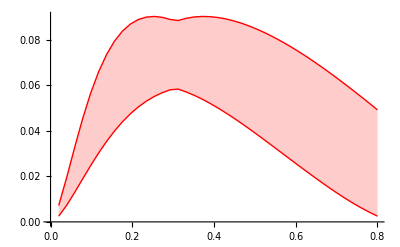

```mathematica
ALTCOMpiperrorband = ErrorBandX[ALTCOMpipfunc,0.02,0.8,40,Red]
```

```mathematica
ErrorBandPrint[ALTCOMpipfunc,0.02,0.8,40,"./bakur/alt_compass_x_pip.csv"]
```

{./bakur/alt_compass_x_pip.csv}

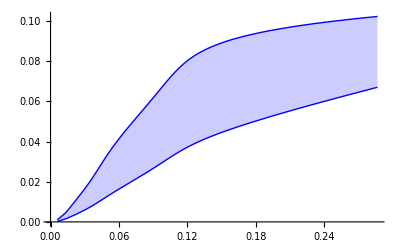

```mathematica
ErrorBandCOMPASS[ALT,"pi+",Blue,"./bakur/alt_compass_x_pip.csv"]
```

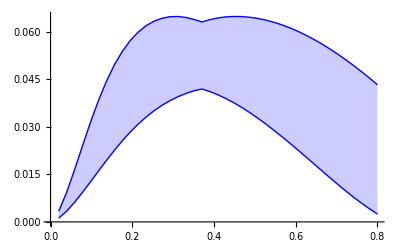

```mathematica
ALTCOMpimerrorband = ErrorBandX[ALTCOMpimfunc,0.02,0.8,40,Blue]
```

```mathematica
ErrorBandPrint[ALTCOMpimfunc,0.02,0.8,40,"./bakur/alt_compass_x_pim.csv"]
```

{./bakur/alt_compass_x_pim.csv}

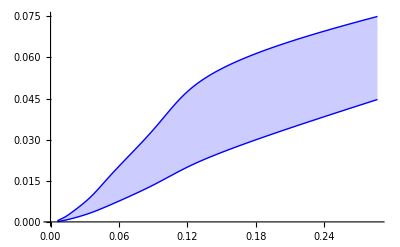

```mathematica
ErrorBandCOMPASS[ALT,"pi-",Blue,"./bakur/alt_compass_x_pim.csv"]
```

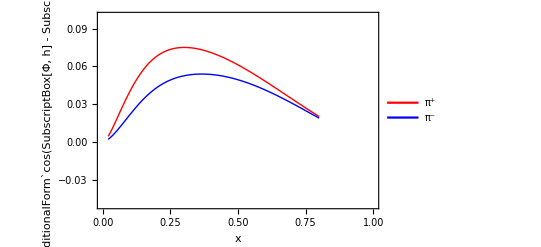

```mathematica
ALTCOMpiplot = Plot[{ALTCOMpipfunc[x],ALTCOMpimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_LT^(TraditionalForm`cos(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

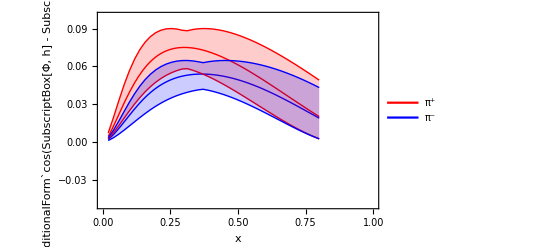

```mathematica
Show[ALTCOMpiplot,ALTCOMpiperrorband,ALTCOMpimerrorband]
```

```mathematica
Export["../tex/figs/ALT_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/ALT_COMPASS_x.pdf

### Positivity

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 M^2))^1 g1T[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[((g_T^FIRST)^2)/(4 k_Tg1T^2 π),Re[k_Tg1T^2]>0]

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 M^2))^1 f1Tperp[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[((f_T^(FIRST perp))^2)/(4 k_TSIVERS^2 π),Re[k_TSIVERS^2]>0]

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 M^2))^1 (f1[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[f_1^2/(16 M^2 π),Re[k_TA^2]>0]

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 M^2))^1 (g1[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[g_1^2/(16 M^2 π),Re[k_Tg1^2]>0]

```mathematica
Positivityu[x_,Q2_] :=((f1u[x,Q2])/(4 Mp √π)-√((g1u[x,Q2])^2/(16 Mp^2 π)+(f1TperpuFirstMoment[x,Q2])^2/(4 avks  π)+(g1Tperpu[x,Q2])^2/(4 avkg1T π)))/((f1u[x,Q2])/(4 Mp √π)+√((g1u[x,Q2])^2/(16 Mp^2 π)+(f1TperpuFirstMoment[x,Q2])^2/(4 avks  π)+(g1Tperpu[x,Q2])^2/(4 avkg1T π)))
```

```mathematica
Positivityd[x_,Q2_] :=((f1d[x,Q2])/(4 Mp √π)-√((g1d[x,Q2])^2/(16 Mp^2 π)+(f1TperpdFirstMoment[x,Q2])^2/(4 avks  π)+(g1Tperpd[x,Q2])^2/(4 avkg1T π)))/((f1d[x,Q2])/(4 Mp √π)+√((g1d[x,Q2])^2/(16 Mp^2 π)+(f1TperpdFirstMoment[x,Q2])^2/(4 avks  π)+(g1Tperpd[x,Q2])^2/(4 avkg1T π)))
```

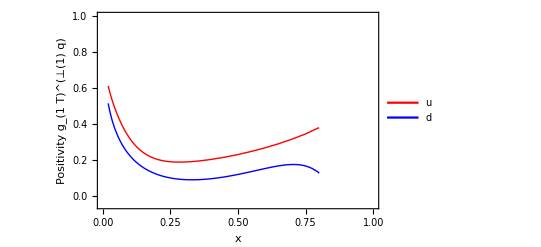

```mathematica
ALTCOMpiplot = Plot[{Positivityu[x,2.4],Positivityd[x,2.4]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,1.}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","Positivity g_(1  T)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d"},{0.7,0.55}]]
```

```mathematica
Export["../tex/figs/g1t_positivity.pdf",%,Background->None]
```

../tex/figs/g1t_positivity.pdf

Phenomenology of leading twist double spin asymmetry A_UL^sin[2 Φ_S](Kotzinian-Mulders)

## F_UL^sin[2 Φ_h] analytical result:

```mathematica
Print["Eq(2.18 g, 4.1b)  C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp]"  ]
PTweightULsin2phi[PhT_] :=1;
```

Eq(2.18 g, 4.1b)  C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp]

```mathematica
Print["Eq(2.18 g)   F_UL^(TraditionalForm`sin[2 SubscriptBox[Φ, h]])= C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp] ="  ]
ConvolutionTMD[omega2AB,h1Lperp,H1perp]
```

Eq(2.18 g)   F_UL^(TraditionalForm`sin[2 SubscriptBox[Φ, h]])= C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_Th1L^2 z^2)) H_1^(FIRST perp) h_L^FIRST M M_hadron P_hT^2 z^2)/(π (p_TCOLLINS^2+k_Th1L^2 z^2)^3)

```mathematica
Print["Eq(2.18 g)  ∫ⅆ^2P_hT F_UL^(TraditionalForm`sin[2 SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp] ="  ]
PTConvolutionTMD[PTweightULsin2phi,omega2AB,h1Lperp,H1perp]
```

Eq(2.18 g)  ∫ⅆ^2P_hT F_UL^(TraditionalForm`sin[2 SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp] =

(4 H_1^(FIRST perp) h_L^FIRST M M_hadron z^2)/(p_TCOLLINS^2+k_Th1L^2 z^2)

## F_UL^sin[2 Φ_h] numerics:

```mathematica
avc = MC^2 avp/(MC^2 + avp);
avkh1l = avk; (* assumption *)
avULsin2phiPT[z_]:= avc+avkh1l z^2;

GfactorULsin2phi[z_,PT_] := (4 Mp^3 Mh)/(π avULsin2phiPT[z]^3) Exp[(-PT^2/avULsin2phiPT[z])]
AfactorULsin2phi[z_] := (4 Mh Mp z^2)/avULsin2phiPT[z]  

FULsin2phi[pion_,x_,z_,Q2_,PT_] := (z^2 PT^2)/Mp^2((4.0/9.0)h1Lu[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1Ld[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) GfactorULsin2phi[z,PT]


FULsin2phiIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)h1Lu[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1Ld[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) AfactorULsin2phi[z]
```

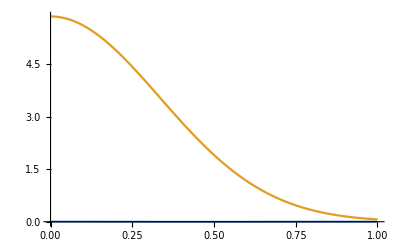

```mathematica
Plot[{FULsin2phi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UL^sin[2 Φ_h]numerics:

```mathematica
AULsin2phi[pion_,x_,z_,Q2_,PT_] := FULsin2phi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AULsin2phiIntegrated[pion_,x_,z_,Q2_] := FULsin2phiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;
```

```mathematica
AULsin2phipimfunc[x_] :=AULsin2phiIntegrated["pi-",x,zcom,Q2com];
AULsin2phipipfunc[x_] :=AULsin2phiIntegrated["pi+",x,zcom,Q2com];
```

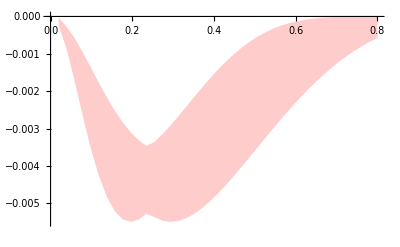

```mathematica
AULsin2phipiperrorband = ErrorBand[AULsin2phipipfunc,0.02,0.8,40,Red]
```

```mathematica
ErrorBandPrint[AULsin2phipipfunc,0.02,0.8,40,"./bakur/AULsin2phi_compass_x_pip.csv"]
```

{./bakur/AULsin2phi_compass_x_pip.csv}

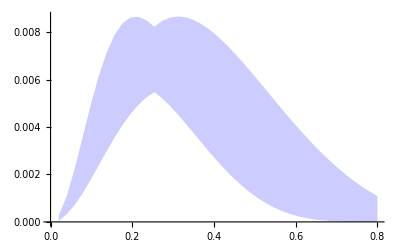

```mathematica
AULsin2phipimerrorband = ErrorBand[AULsin2phipimfunc,0.02,0.8,40,Blue]
```

```mathematica
ErrorBandPrint[AULsin2phipimfunc,0.02,0.8,40,"./bakur/AULsin2phi_compass_x_pim.csv"]
```

{./bakur/AULsin2phi_compass_x_pim.csv}

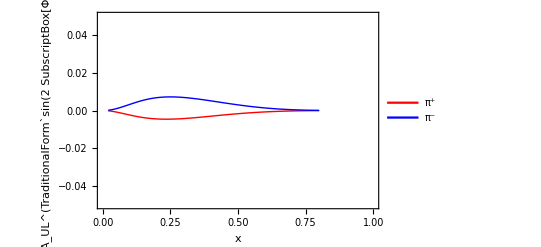

```mathematica
AULsin2phipiplot = Plot[{AULsin2phipipfunc[x],AULsin2phipimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UL^(TraditionalForm`sin(2 SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

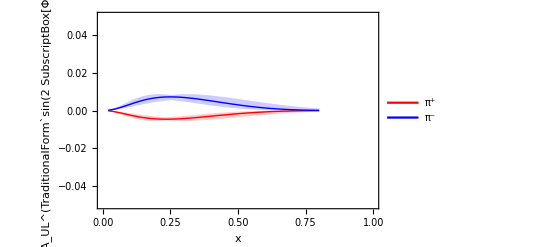

```mathematica
Show[AULsin2phipiplot,AULsin2phipiperrorband,AULsin2phipimerrorband]
```

```mathematica
Export["../tex/figs/AULsin2phi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AULsin2phi_COMPASS_x.pdf

### Plot of x dependence COMPASS NEW

```mathematica
AULsin2phipimerrorband =ErrorBandCOMPASS[AULsin2phi,"pi-",Blue,"./bakur/AULsin2phi_compass_x_pim.csv"]
centralpim = central;
```

{-Graphics-}

```mathematica
AULsin2phipiperrorband =ErrorBandCOMPASS[AULsin2phi,"pi+",Red,"./bakur/AULsin2phi_compass_x_pip.csv"]
centralpip = central;
```

{-Graphics-}

```mathematica
AULsin2phipiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.05,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue}}, FrameLabel->{"x","A_UL^(TraditionalForm`sin(2 SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

-Graphics-

```mathematica
Show[AULsin2phipiplot,AULsin2phipiperrorband,AULsin2phipimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/AULsin2phi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AULsin2phi_COMPASS_x.pdf

### Positivity

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 M^2))^1 h1Lperp[kt^2])^2 ⅆphiⅆkt
```

((h_L^FIRST)^2)/(4 k_Th1L^2 π)

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 M^2))^1 h1perp[kt^2])^2 ⅆphiⅆkt
```

((h_1^(FIRST perp))^2)/(4 k_BOERMULDERS^2 π)

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 M^2))^1 (f1[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[f_1^2/(16 M^2 π),Re[k_TA^2]>0]

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 M^2))^1 (g1[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[g_1^2/(16 M^2 π),Re[k_Tg1^2]>0]

```mathematica
Positivityu[x_,Q2_] := ((f1u[x,Q2])/(4 Mp √π)-√((g1u[x,Q2])^2/(16 Mp^2 π)+(h1perpuFirstMoment[x,Q2])^2/(4 avks  π)+(h1Lu[x,Q2])^2/(4 avkg1T π)))/((f1u[x,Q2])/(4 Mp √π)+√((g1u[x,Q2])^2/(16 Mp^2 π)+(h1perpuFirstMoment[x,Q2])^2/(4 avks  π)+(h1Lu[x,Q2])^2/(4 avkg1T π)))
```

```mathematica
Positivityd[x_,Q2_] :=((f1d[x,Q2])/(4 Mp √π)-√((g1d[x,Q2])^2/(16 Mp^2 π)+(h1perpdFirstMoment[x,Q2])^2/(4 avks  π)+(h1Ld[x,Q2])^2/(4 avkg1T π)))/((f1d[x,Q2])/(4 Mp √π)+√((g1d[x,Q2])^2/(16 Mp^2 π)+(h1perpdFirstMoment[x,Q2])^2/(4 avks  π)+(h1Ld[x,Q2])^2/(4 avkg1T π)))
```

```mathematica
AULsin2phipiplot = Plot[{Positivityu[x,2.4],Positivityd[x,2.4]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0.,1.}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","Positivity h_(1  L)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d"},{0.7,0.15}]]
```

-Graphics-

```mathematica
Export["../tex/figs/h1lperp_positivity.pdf",%,Background->None]
```

../tex/figs/h1lperp_positivity.pdf

## A_UL^sin[2 Φ_h]numerics JLab:

### Plot of x dependence

```mathematica
sjlab = Mp^2 + 2 5.7 Mp; 
Clear[x,y,z,Q2,PT]; 
y[Q2_,x_] :=  Q2/(sjlab x);

AULsin2phiY[pion_,x_,z_,Q2_,PT_] := (2(1- y[Q2,x] )FULsin2phi[pion,x,z,Q2,PT])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUU[pion,x,z,Q2,PT])  ;

AULsin2phiIntegratedY[pion_,x_,z_,Q2_] := ((2- y[Q2,x] )√(1-y[Q2,x])FULsin2phiIntegrated[pion,x,z,Q2])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUUIntegrated[pion,x,z,Q2]);
```

```mathematica
AULsin2phi0funcY[x_] :=(AULsin2phiY["pi+",x,0.5,2.,0.4]+AULsin2phiY["pi-",x,0.5,2.,0.4])/2;
```

```mathematica
AULsin2phi0errorbandY = ErrorBand[AULsin2phi0funcY,0.02,0.8,40,Red]
```

{-Graphics-}

```mathematica
Clear[data,tab];
datapi0=Cases[Import["./data/pi0-eg1dvcs/pi0-aul-sin2-x-dep3.dat","Table"],{_?NumberQ,___}]; 
tabpi0 =  Table[{{datapi0[[i]][[3]],datapi0[[i]][[4]]},ErrorBar[Sqrt[datapi0[[i]][[5]]^2+datapi0[[i]][[6]]^2]]},{i,9,12(*Length[datapip]*)},{j,1}];
plotdataAULpi0=ErrorListPlot[tabpi0, Frame-> True,PlotRange->{{0,1},{-0.2,0.35}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

-Graphics-

```mathematica
AULsin2philotY = Plot[{AULsin2phi0funcY[x]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.1,0.2}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_(UL, ⟨y⟩)^(TraditionalForm`sin 2 SubscriptBox[Φ, h])"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^0"},{0.7,0.7}]]
```

-Graphics-

```mathematica
Show[AULsin2philotY,plotdataAULpi0,AULsin2phi0errorbandY]
```

-Graphics-

```mathematica
Export["../tex/figs/AULsin2phi_JLAB_x.pdf",%,Background->None]
```

../tex/figs/AULsin2phi_JLAB_x.pdf

## Sub-leading Structure Functions and Asymmetries

Phenomenology of sub-leading twist double spin asymmetry A_LT^cos[Φ_S]not preserving WW-type relations, variant in the paper

## F_LT^cos[Φ_S] analytical result:

```mathematica
Print["Eq(4.2 b)(2 M)/QC[ -x g_TD_1], " ]
PTweightLTcosphiS[PhT_] :=1;
```

Eq(4.2 b)(2 M)/QC[ -x g_TD_1],

```mathematica
Print["Eq()   F_LT^(TraditionalForm`cos[SubscriptBox[Φ, S]])= (2 M)/QC[ -x g_TD_1] ="  ]
(2 M)/Q(-xBj)ConvolutionTMD[omega0,gT,D1]
```

Eq()   F_LT^(TraditionalForm`cos[SubscriptBox[Φ, S]])= (2 M)/QC[ -x g_TD_1] =

-(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1T^2 z^2)) gT M xBj)/(Q (π p_TA^2+k_Tg1T^2 π z^2))

```mathematica
Print["Eq()  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT (2 M)/QC[ -x g_TD_1]] ="  ]
(2 M)/Q(-xBj)PTConvolutionTMD[PTweightLTcosphiS,omega0,gT,D1]
```

Eq()  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT (2 M)/QC[ -x g_TD_1]] =

ConditionalExpression[-(2 D_1 gT M xBj)/Q,Re[p_TA^2+k_Tg1T^2 z^2]>0]

## F_LT^cos[Φ_S] numerics:

```mathematica
avLLPT[z_]:= avp+avkg z^2;

GLTCOSPhi[z_,PT_] := 1/(π avLLPT[z]) Exp[(-PT^2/avLLPT[z])]
ALTCOSPhi[z_] := 1.  
(* did I miss x ? See formula x gt ....*) 
FLTcosPhi[pion_,x_,z_,Q2_,PT_] := (-2 Mp x)/Sqrt[Q2]((4.0/9.0)gTu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)gTd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)gTs[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)gTubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)gTdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)gTsbar[x,Q2] D1sbar[pion,z,Q2] ) GLTCOSPhi[z,PT];


FLTcosPhiIntegrated[pion_,x_,z_,Q2_] := (-2 Mp x)/Sqrt[Q2]((4.0/9.0)gTu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)gTd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)gTs[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)gTubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)gTdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)gTsbar[x,Q2] D1sbar[pion,z,Q2] ) ALTCOSPhi[z];
```

```mathematica
Plot[{FLTcosPhi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.11061486030073391061134824298051171354018151760101318359375}. NIntegrate obtained -0.0262016 and 3.01517×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.120682927156044721150873755277643795125186443328857421875}. NIntegrate obtained -0.169845 and 1.84949×10^-7 for the integral and error estimates.

-Graphics-

## A_LT^cos[Φ_S]numerics:

```mathematica
ALTcosPhi[pion_,x_,z_,Q2_,PT_] := FLTcosPhi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

ALTcosPhiIntegrated[pion_,x_,z_,Q2_] := FLTcosPhiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;
```

```mathematica
ALTcosPhipimfunc[x_] :=ALTcosPhiIntegrated["pi-",x,zcom,Q2com];
ALTcosPhipipfunc[x_] :=ALTcosPhiIntegrated["pi+",x,zcom,Q2com];
```

```mathematica
ALTcosPhipiperrorband = ErrorBand[ALTcosPhipipfunc,0.02,0.8,40,Red]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 6.76732 and 0.000028186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained -3.72263 and 0.0000267306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 0.066699 and 0.0000109926 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-Graphics-}

```mathematica
ErrorBandPrint[ALTcosPhipipfunc,0.02,0.8,40,"./bakur/ALTcosPhi_compass_x_pip.csv"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 6.76732 and 0.000028186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained -3.72263 and 0.0000267306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 0.066699 and 0.0000109926 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{./bakur/ALTcosPhi_compass_x_pip.csv}

```mathematica
ALTcosPhipimerrorband = ErrorBand[ALTcosPhipimfunc,0.02,0.8,40,Blue]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 6.76732 and 0.000028186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained -3.72263 and 0.0000267306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 0.066699 and 0.0000109926 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-Graphics-}

```mathematica
ErrorBandPrint[ALTcosPhipimfunc,0.02,0.8,40,"./bakur/ALTcosPhi_compass_x_pim.csv"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 6.76732 and 0.000028186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained -3.72263 and 0.0000267306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 0.066699 and 0.0000109926 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{./bakur/ALTcosPhi_compass_x_pim.csv}

```mathematica
ALTcosPhipiplot = Plot[{ALTcosPhipipfunc[x],ALTcosPhipimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.07,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_LT^(TraditionalForm`cos(SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained 6.17231 and 7.09466×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained -3.23325 and 9.47265×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained 0.122419 and 3.74596×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

```mathematica
Show[ALTcosPhipiplot,ALTcosPhipiperrorband,ALTcosPhipimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/ALTcosPhi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/ALTcosPhi_COMPASS_x.pdf

### Plot of x dependence COMPASS NEW

```mathematica
ALTcosPhipimerrorband =ErrorBandCOMPASS[ALTcosPhi,"pi-",Blue,"./bakur/ALTcosPhi_compass_x_pim.csv"]
centralpim = central;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained 8.26376 and 0.0023887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.03588 and 0.00527687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.0285 and 0.00941914 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-Graphics-}

```mathematica
ALTcosPhipiperrorband =ErrorBandCOMPASS[ALTcosPhi,"pi+",Red,"./bakur/ALTcosPhi_compass_x_pip.csv"]
centralpip = central;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained 8.26376 and 0.0023887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.03588 and 0.00527687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.0285 and 0.00941914 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-Graphics-}

```mathematica
ALTcosPhipiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.07,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue}}, FrameLabel->{"x","A_LT^(TraditionalForm`cos(SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

-Graphics-

```mathematica
Show[ALTcosPhipiplot,ALTcosPhipiperrorband,ALTcosPhipimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/AULsin2phi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AULsin2phi_COMPASS_x.pdf

### WW-type approximation comparison Eq. 3.3 e

```mathematica
WWplot = Plot[{0.1 gTu[0.1,2.4] 1/(π avkg) Exp[(-kT^2/avkg)],g1Tperpu[0.1,2.4] kT^2/(π avkg^2) Exp[(-kT^2/avkg)]},{kT,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.2,0.5}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"k_⊥ (GeV)","WW-type approximation x g_T^q vs g_(1  T)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"x g_T^q","g_(1  T)^(⊥(1) q)"},{0.7,0.15}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

```mathematica
Export["../tex/figs/gT_vs_g1Tperp_wwtype.pdf",%,Background->None]
```

../tex/figs/gT_vs_g1Tperp_wwtype.pdf

Phenomenology of sub-leading twist spin asymmetry A_UL^sin[Φ_h]not preserving WW-type relations, variant in the paper

## F_UL^sin[Φ_h] analytical result:

```mathematica
Clear[x,y,z,Q2,PT]
```

```mathematica
Print["Eq(4.2 e)(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥], x h_L(x) = - 2 h1Lperp(1)(x)" ]
PTweightULsinphih[PhT_] :=1;
```

Eq(4.2 e)(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥], x h_L(x) = - 2 h1Lperp(1)(x)

```mathematica
Print["Eq(4.2 e)   F_UL^(TraditionalForm`sin[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥] ="  ]
(2 M xBj)/Q ConvolutionTMD[omega1A, hL,H1perp]
```

Eq(4.2 e)   F_UL^(TraditionalForm`sin[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_ThL^2 z^2)) H_1^(FIRST perp) hL M M_hadron P_hT xBj z)/(π Q (p_TCOLLINS^2+k_ThL^2 z^2)^2)

```mathematica
Print["Eq(4.2 e)  ∫ⅆ^2P_hT F_UL^(TraditionalForm`sin[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥] ="  ]

(2 M xBj)/Q PTConvolutionTMD[PTweightULsinphih,omega1A, hL,H1perp]
```

Eq(4.2 e)  ∫ⅆ^2P_hT F_UL^(TraditionalForm`sin[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥] =

ConditionalExpression[(2 H_1^(FIRST perp) hL M M_hadron √π xBj z)/(Q √(p_TCOLLINS^2+k_ThL^2 z^2)),p_TCOLLINS^2+z^2 Re[k_ThL^2]>0]

## F_UL^sin[Φ_h] numerics:

```mathematica
avc = MC^2 avp/(MC^2 + avp);
avkh1l = avk; (* assumption *)
avULsinphiPT[z_]:= avc+avkh1l z^2;
(* x hL = h_1L^perp(1) *)
GfactorULsinphi[z_,PT_] := (2 Mp^2)/(π avULsinphiPT[z]^2) Exp[(-PT^2/avULsinphiPT[z])]
AfactorULsinphi[z_] := (Mh z √Pi)/avULsinphiPT[z]^(1/2)  

FULsinphi[pion_,x_,z_,Q2_,PT_] := ((2 Mp)/Sqrt[Q2])(z PT Mh)/Mp^2(-2)((4.0/9.0)h1Lu[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1Ld[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) GfactorULsinphi[z,PT]


FULsinphiIntegrated[pion_,x_,z_,Q2_] := ((2 Mp)/Sqrt[Q2])(-2)((4.0/9.0)h1Lu[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1Ld[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) AfactorULsinphi[z]
```

```mathematica
Plot[{FULsinphi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

-Graphics-

## A_UL^sin[Φ_h]numerics:

```mathematica
AULsinphi[pion_,x_,z_,Q2_,PT_] := FULsinphi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AULsinphiIntegrated[pion_,x_,z_,Q2_] := FULsinphiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;
```

```mathematica
AULsinphipimfunc[x_] :=AULsinphiIntegrated["pi-",x,zcom,Q2com];
AULsinphipipfunc[x_] :=AULsinphiIntegrated["pi+",x,zcom,Q2com];
```

```mathematica
AULsinphipiperrorband = ErrorBand[AULsinphipipfunc,0.02,0.8,40,Red]
```

ErrorBand[AULsinphipipfunc,0.02,0.8,40,RGBColor[1, 0, 0]]

```mathematica
ErrorBandPrint[AULsinphipipfunc,0.02,0.8,40,"./bakur/AULsinphi_compass_x_pip.csv"]
```

ErrorBandPrint[AULsinphipipfunc,0.02,0.8,40,./bakur/AULsinphi_compass_x_pip.csv]

```mathematica
AULsinphipimerrorband = ErrorBand[AULsinphipimfunc,0.02,0.8,40,Blue]
```

ErrorBand[AULsinphipimfunc,0.02,0.8,40,RGBColor[0, 0, 1]]

```mathematica
ErrorBandPrint[AULsinphipimfunc,0.02,0.8,40,"./bakur/AULsinphi_compass_x_pim.csv"]
```

ErrorBandPrint[AULsinphipimfunc,0.02,0.8,40,./bakur/AULsinphi_compass_x_pim.csv]

```mathematica
AULsinphipiplot = Plot[{AULsinphipipfunc[x],AULsinphipimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.02,0.03}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UL^(TraditionalForm`sin(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

-Graphics-

```mathematica
Show[AULsinphipiplot,AULsinphipiperrorband,AULsinphipimerrorband]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,ErrorBand[AULsinphipipfunc,0.02,0.8,40,RGBColor[1, 0, 0]],ErrorBand[AULsinphipimfunc,0.02,0.8,40,RGBColor[0, 0, 1]]]

```mathematica
Export["../tex/figs/AULsinphi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AULsinphi_COMPASS_x.pdf

### Plot of x dependence COMPASS NEW

```mathematica
AULsinphipimerrorband =ErrorBandCOMPASS[AULsinphi,"pi-",Blue,"./bakur/AULsinphi_compass_x_pim.csv"]
centralpim = central;
```

ErrorBandCOMPASS[AULsinphi,pi-,RGBColor[0, 0, 1],./bakur/AULsinphi_compass_x_pim.csv]

```mathematica
AULsinphipiperrorband =ErrorBandCOMPASS[AULsinphi,"pi+",Red,"./bakur/AULsinphi_compass_x_pip.csv"]
centralpip = central;
```

ErrorBandCOMPASS[AULsinphi,pi+,RGBColor[1, 0, 0],./bakur/AULsinphi_compass_x_pip.csv]

```mathematica
AULsinphipiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.03,0.03}},PlotStyle->{{Thick,Red},{Thick,Blue}}, FrameLabel->{"x","A_UL^(TraditionalForm`sin(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

ListPlot::iodeg: 4 is not a valid interpolation order specification, or the given order is too high for the input array {{1.,central},{2.,central}}.

-Graphics-

```mathematica
Show[AULsinphipiplot,AULsinphipiperrorband,AULsinphipimerrorband]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,ErrorBandCOMPASS[AULsinphi,pi+,RGBColor[1, 0, 0],./bakur/AULsinphi_compass_x_pip.csv],ErrorBandCOMPASS[AULsinphi,pi-,RGBColor[0, 0, 1],./bakur/AULsinphi_compass_x_pim.csv]]

```mathematica
Export["../tex/figs/AULsinphi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AULsinphi_COMPASS_x.pdf

## A_UL^(<y>sin[Φ_h])numerics:

### Plot of x dependence

```mathematica
shermes = Mp^2 + 2 27.5 Mp; 
Clear[x,y,z,Q2,PT]; 
y[Q2_,x_] :=  Q2/(shermes x);

AULsinphiY[pion_,x_,z_,Q2_,PT_] := ((2- y[Q2,x] )√(1-y[Q2,x])FULsinphi[pion,x,z,Q2,PT])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUU[pion,x,z,Q2,PT])  ;

AULsinphiIntegratedY[pion_,x_,z_,Q2_] := ((2- y[Q2,x] )√(1-y[Q2,x])FULsinphiIntegrated[pion,x,z,Q2])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUUIntegrated[pion,x,z,Q2]);
```

```mathematica
AULsinphipipfuncY[x_] :=AULsinphiIntegratedY["pi+",x,0.4,3.];
```

```mathematica
AULsinphiY["pi-",0.1,0.3,1,1]
```

-0.0219906

```mathematica
AULsinphipiperrorbandY = ErrorBand[AULsinphipipfuncY,0.02,0.8,40,Red]
```

GreaterEqual::nord: Invalid comparison with 0.-0.000109662 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with 0.-0.000109662 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

{-Graphics-}

```mathematica
AULsinphipimfuncY[x_] :=AULsinphiIntegratedY["pi-",x,0.4,3.];
```

```mathematica
AULsinphipimerrorbandY = ErrorBand[AULsinphipimfuncY,0.02,0.8,40,Blue]
```

GreaterEqual::nord: Invalid comparison with 0.+0.000121675 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with 0.+0.000121675 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

{-Graphics-}

```mathematica
Clear[data,tab];
datapip=Cases[Import["./data/AULsinPhi_hermes_x.dat","Table"],{_?NumberQ,___}]; 
tabpip =  Table[{{datapip[[i]][[1]],datapip[[i]][[12]]},ErrorBar[Sqrt[datapip[[i]][[13]]^2+datapip[[i]][[14]]^2]]},{i,Length[datapip]},{j,1}];
plotdataAULpip=ErrorListPlot[tabpip, Frame-> True,PlotRange->{{0,1},{-0.1,0.2}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

-Graphics-

```mathematica
Clear[data,tab];
datapim=Cases[Import["./data/AULsinPhi_hermes_x.dat","Table"],{_?NumberQ,___}]; 
tabpim =  Table[{{datapim[[i]][[1]],datapim[[i]][[15]]},ErrorBar[Sqrt[datapim[[i]][[16]]^2+datapim[[i]][[17]]^2]]},{i,Length[datapim]},{j,1}];
plotdataAULpim=ErrorListPlot[tabpim, Frame-> True,PlotRange->{{0,1},{-0.1,0.2}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

-Graphics-

```mathematica
AULsinphipipplotY = Plot[{AULsinphiIntegratedY["pi+",x,0.4,3.],AULsinphiIntegratedY["pi-",x,0.4,3.]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.1,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_(UL, <y>)^(TraditionalForm`sin SubscriptBox[Φ, h])"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.7}]]
```

-Graphics-

```mathematica
Show[AULsinphipipplotY,AULsinphipiperrorbandY,AULsinphipimerrorbandY,plotdataAULpip,plotdataAULpim]
```

-Graphics-

```mathematica
Export["../tex/figs/AULsinphi_HERMES_x.pdf",%,Background->None]
```

../tex/figs/AULsinphi_HERMES_x.pdf

## A_UL^sin[Φ_h]numerics JLab:

### Plot of x dependence

```mathematica
sjlab = Mp^2 + 2 5.7 Mp; 
Clear[x,y,z,Q2,PT]; 
y[Q2_,x_] :=  Q2/(sjlab x);

AULsinphiY[pion_,x_,z_,Q2_,PT_] := ((2- y[Q2,x] )√(1-y[Q2,x])FULsinphi[pion,x,z,Q2,PT])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUU[pion,x,z,Q2,PT])  ;

AULsinphiIntegratedY[pion_,x_,z_,Q2_] := ((2- y[Q2,x] )√(1-y[Q2,x])FULsinphiIntegrated[pion,x,z,Q2])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUUIntegrated[pion,x,z,Q2]);
```

```mathematica
AULsinphi0funcY[x_] :=(AULsinphiY["pi+",x,0.5,2.,0.4]+AULsinphiY["pi-",x,0.5,2.,0.4])/2;
```

```mathematica
AULsinphi0errorbandY = ErrorBand[AULsinphi0funcY,0.02,0.8,40,Red]
```

GreaterEqual::nord: Invalid comparison with 0.+4.99449×10^-6 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with 0.+4.99449×10^-6 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

{-Graphics-}

```mathematica
Clear[data,tab];
datapi0=Cases[Import["./data/pi0-eg1dvcs/pi0-aul-sin-x-dep3.dat","Table"],{_?NumberQ,___}]; 
tabpi0 =  Table[{{datapi0[[i]][[3]],datapi0[[i]][[4]]},ErrorBar[Sqrt[datapi0[[i]][[5]]^2+datapi0[[i]][[6]]^2]]},{i,9,12(*Length[datapip]*)}];
plotdataAULpi0=ErrorListPlot[tabpi0, Frame-> True,PlotRange->{{0,1},{-0.1,0.35}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

-Graphics-

```mathematica
AULsinphilotY = Plot[{(AULsinphiY["pi+",x,0.5,2.,0.4]+AULsinphiY["pi-",x,0.5,2.,0.4])/2},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.1,0.2}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_(UL, ⟨y⟩)^(TraditionalForm`sin SubscriptBox[Φ, h])"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^0"},{0.7,0.7}]]
```

-Graphics-

```mathematica
Show[AULsinphilotY,plotdataAULpi0,AULsinphi0errorbandY]
```

-Graphics-

```mathematica
Export["../tex/figs/AULsinphi_JLAB_x.pdf",%,Background->None]
```

../tex/figs/AULsinphi_JLAB_x.pdf

Phenomenology of sub-leading twist spin asymmetry A_LL^cos[Φ_h]agreement with Peter

## F_LL^cos[Φ_h] analytical result:

```mathematica
Print["Eq(3.3 e 4.2 c)(2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1], x g_L^⊥ = g1" ]
PTweightLLcosphih[PhT_] :=1;
```

Eq(3.3 e 4.2 c)(2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1], x g_L^⊥ = g1

```mathematica
Print["Eq(3.3 e 4.2 c)   F_LL^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1] ="  ]
-(2 M)/Q ConvolutionTMD[omega1B, g1,D1]
```

Eq(3.3 e 4.2 c)   F_LL^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1] =

-(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1^2 z^2)) g_1 k_Tg1^2 P_hT z)/(π Q (p_TA^2+k_Tg1^2 z^2)^2)

```mathematica
Print["Eq(3.3 e 4.2 c)  ∫ⅆ^2P_hT F_LL^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1] ="  ]
-(2 M)/Q PTConvolutionTMD[PTweightLLcosphih,omega1B,  g1,D1]
```

Eq(3.3 e 4.2 c)  ∫ⅆ^2P_hT F_LL^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1] =

-(D_1 g_1 k_Tg1^2 √π z √(1/(p_TA^2+k_Tg1^2 z^2)))/Q

## F_LL^cos[Φ_h] numerics:

```mathematica
avLLcosphiPT[z_]:= avp+avkg z^2;

GfactorLLcosphi[z_,PT_] := avkg/(π avLLcosphiPT[z]^2) Exp[(-PT^2/avLLcosphiPT[z])]
AfactorLLcosphi[z_] := (z √Pi avkg)/(2 Mp √avLLcosphiPT[z]) ; 

FLLcosphi[pion_,x_,z_,Q2_,PT_] := (-(2 Mp)/Sqrt[Q2])(z PT)/Mp((4.0/9.0)g1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1sbar[x,Q2] D1sbar[pion,z,Q2] )GfactorLLcosphi[z,PT]


FLLcosphiIntegrated[pion_,x_,z_,Q2_] := (-(2 Mp)/Sqrt[Q2])((4.0/9.0)g1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1sbar[x,Q2] D1sbar[pion,z,Q2] )AfactorLLcosphi[z]
```

```mathematica
Plot[{FLLcosphi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

-Graphics-

## A_LL^cos[Φ_h]numerics:

```mathematica
ALLcosphi[pion_,x_,z_,Q2_,PT_] := FLLcosphi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

ALLcosphiIntegrated[pion_,x_,z_,Q2_] := FLLcosphiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;
```

```mathematica
ALLcosphipimfunc[x_] :=ALLcosphiIntegrated["pi-",x,zcom,Q2com];
ALLcosphipipfunc[x_] :=ALLcosphiIntegrated["pi+",x,zcom,Q2com];
```

```mathematica
ALLcosphipiperrorband = ErrorBand[ALLcosphipipfunc,0.02,0.8,40,Red]
```

{-Graphics-}

```mathematica
ErrorBandPrint[ALLcosphipipfunc,0.02,0.8,40,"./bakur/ALLcosphi_compass_x_pip.csv"]
```

{./bakur/ALLcosphi_compass_x_pip.csv}

```mathematica
ALLcosphipimerrorband = ErrorBand[ALLcosphipimfunc,0.02,0.8,40,Blue]
```

{-Graphics-}

```mathematica
ErrorBandPrint[ALLcosphipimfunc,0.02,0.8,40,"./bakur/ALLcosphi_compass_x_pim.csv"]
```

{./bakur/ALLcosphi_compass_x_pim.csv}

```mathematica
ALLcosphipiplot = Plot[{ALLcosphipipfunc[x],ALLcosphipimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.07,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_LL^(TraditionalForm`cos(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.75}]]
```

-Graphics-

```mathematica
Show[ALLcosphipiplot,ALLcosphipiperrorband,ALLcosphipimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/ALLcosphi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/ALLcosphi_COMPASS_x.pdf

### Plot of x dependence COMPASS NEW

```mathematica
ALLcosphipimerrorband =ErrorBandCOMPASS[ALLcosphi,"pi-",Blue,"./bakur/ALLcosphi_compass_x_pim.csv"]
centralpim = central;
```

{-Graphics-}

```mathematica
ALLcosphipiperrorband =ErrorBandCOMPASS[ALLcosphi,"pi+",Red,"./bakur/ALLcosphi_compass_x_pip.csv"]
centralpip = central;
```

{-Graphics-}

```mathematica
ALLcosphipiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.07,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue}}, FrameLabel->{"x","A_LL^(TraditionalForm`cos(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.85,0.75}]]
```

-Graphics-

```mathematica
Show[ALLcosphipiplot,ALLcosphipiperrorband,ALLcosphipimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/ALLcosphi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/ALLcosphi_COMPASS_x.pdf

Phenomenology of sub-leading twist spin asymmetry A_LT^cos[2 Φ_h-Φ_S]

## F_LT^cos[2 Φ_h-Φ_S] analytical result:

```mathematica
Print["Eq(4.2 d)(2 M)/QC[ -(2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1], x g_T^⊥ = g_(1  T)^⊥" ]
omega2C[kt_,PhT_,phi_] := (2(kt Cos[phi])^2-kt^2)/(2 M^2);
PTweightLTcos2phih[PhT_] :=1;
```

Eq(4.2 d)(2 M)/QC[ -(2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1], x g_T^⊥ = g_(1  T)^⊥

```mathematica
Print["Eq(4.2 d)   F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] ="  ]
-(2 M)/Q ConvolutionTMD[omega2C, gTperp,D1]
```

Eq(4.2 d)   F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] =

-(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+ktgT z^2)) gTperpSecondMoment M^3 P_hT^2 z^2)/(π Q (p_TA^2+ktgT z^2)^3)

```mathematica
XMomentTMD[2,gTperp]
```

ConditionalExpression[gTperpSecondMoment,Re[ktgT]>0]

```mathematica
XMomentTMD[0,g1T]
```

ConditionalExpression[(2 g_T^FIRST M^2)/k_Tg1T^2,Re[k_Tg1T^2]>0]

```mathematica
XMomentTMD[0,gTperp]
```

ConditionalExpression[(2 gTperpSecondMoment M^4)/ktgT^2,Re[ktgT]>0]

So that relation of gTperp (2) and g1Tperp is gTperpSecondMoment = (k_Tg1T^2 g_T^FIRST)/M^2

```mathematica
Print["Eq(4.2 d)  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] ="  ]
-(2 M)/Q PTConvolutionTMD[PTweightLTcos2phih,omega2C,  gTperp,D1]
```

Eq(4.2 d)  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] =

ConditionalExpression[-(2 D_1 gTperpSecondMoment M^3 z^2)/(Q (p_TA^2+ktgT z^2)),Re[p_TA^2+ktgT z^2]>0]

## F_LT^cos[2 Φ_h-Φ_S] analytical result(directly from WW):

```mathematica
Print["Eq(4.2 d)(2 M)/QC[ -(2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1], x g_T^⊥ = g_(1  T)^⊥" ]
PTweightLTcos2phih[PhT_] :=1;
```

Eq(4.2 d)(2 M)/QC[ -(2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1], x g_T^⊥ = g_(1  T)^⊥

```mathematica
Print["Eq(4.2 d)   F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] ="  ]
-(2 M)/Q ConvolutionTMD[omega2C, g1T,D1]
```

Eq(4.2 d)   F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] =

-(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1T^2 z^2)) g_T^FIRST k_Tg1T^2 M P_hT^2 z^2)/(π Q (p_TA^2+k_Tg1T^2 z^2)^3)

So that relation of gTperp (2) and g1Tperp is gTperpSecondMoment = (k_Tg1T^2 g_T^FIRST)/M^2 and the result is the same as above

```mathematica
Print["Eq(4.2 d)  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] ="  ]
(2 M)/Q PTConvolutionTMD[PTweightLTcos2phih,omega2C,  g1T,D1]
```

Eq(4.2 d)  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] =

ConditionalExpression[(2 D_1 g_T^FIRST k_Tg1T^2 M z^2)/(Q (p_TA^2+k_Tg1T^2 z^2)),Re[p_TA^2+k_Tg1T^2 z^2]>0]

## F_LT^cos[2 Φ_h-Φ_S] numerics:

```mathematica
avkg1T = avkg; (*assumption*)
avLTcos2phiPT[z_]:= avp+avkg1T z^2;

GLTcos2phi[z_,PT_] := (Mp^2 avkg1T)/(π avLTcos2phiPT[z]^3) Exp[(-PT^2/avLTcos2phiPT[z])]
AfactorLTcos2phi[z_] := -(z^2 avkg1T)/avLTcos2phiPT[z]  

FLTcos2phi[pion_,x_,z_,Q2_,PT_] := ((2 Mp)/Sqrt[Q2])(-(z^2 PT^2)/Mp^2)((4.0/9.0)g1Tperpu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1Tperpd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1Tperps[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1Tperpubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1Tperpdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1Tperpsbar[x,Q2] D1sbar[pion,z,Q2] ) GLTcos2phi[z,PT]


FLTcos2phiIntegrated[pion_,x_,z_,Q2_] := ((2 Mp)/Sqrt[Q2])((4.0/9.0)g1Tperpu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1Tperpd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1Tperps[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1Tperpubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1Tperpdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1Tperpsbar[x,Q2] D1sbar[pion,z,Q2] ) AfactorLTcos2phi[z]
```

```mathematica
Plot[{FLTcos2phi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.11061486030073391061134824298051171354018151760101318359375}. NIntegrate obtained -0.0262016 and 3.01517×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.120682927156044721150873755277643795125186443328857421875}. NIntegrate obtained -0.169845 and 1.84949×10^-7 for the integral and error estimates.

-Graphics-

## A_LT^cos[2 Φ_h-Φ_S]numerics:

```mathematica
ALTcos2PhiminusPhiS[pion_,x_,z_,Q2_,PT_] := FLTcos2phi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

ALTcos2PhiminusPhiSIntegrated[pion_,x_,z_,Q2_] := FLTcos2phiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;
```

```mathematica
ALTcos2PhiminusPhiSpimfunc[x_] :=ALTcos2PhiminusPhiSIntegrated["pi-",x,zcom,Q2com];
ALTcos2PhiminusPhiSpipfunc[x_] :=ALTcos2PhiminusPhiSIntegrated["pi+",x,zcom,Q2com];
```

```mathematica
ALTcos2PhiminusPhiSpiperrorband = ErrorBand[ALTcos2PhiminusPhiSpipfunc,0.02,0.8,40,Red]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 6.76732 and 0.000028186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained -3.72263 and 0.0000267306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 0.066699 and 0.0000109926 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-Graphics-}

```mathematica
ErrorBandPrint[ALTcos2PhiminusPhiSpipfunc,0.02,0.8,40,"./bakur/ALTcos2PhiminusPhiS_compass_x_pip.csv"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 6.76732 and 0.000028186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained -3.72263 and 0.0000267306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 0.066699 and 0.0000109926 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{./bakur/ALTcos2PhiminusPhiS_compass_x_pip.csv}

```mathematica
ALTcos2PhiminusPhiSpimerrorband = ErrorBand[ALTcos2PhiminusPhiSpimfunc,0.02,0.8,40,Blue]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 6.76732 and 0.000028186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained -3.72263 and 0.0000267306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 0.066699 and 0.0000109926 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-Graphics-}

```mathematica
ErrorBandPrint[ALTcos2PhiminusPhiSpimfunc,0.02,0.8,40,"./bakur/ALTcos2PhiminusPhiS_compass_x_pim.csv"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 6.76732 and 0.000028186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained -3.72263 and 0.0000267306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 0.066699 and 0.0000109926 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{./bakur/ALTcos2PhiminusPhiS_compass_x_pim.csv}

```mathematica
ALTcos2PhiminusPhiSpiplot = Plot[{ALTcos2PhiminusPhiSpipfunc[x],ALTcos2PhiminusPhiSpimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.07,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_LT^(TraditionalForm`cos(2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.75}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained 6.17231 and 7.09466×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained -3.23325 and 9.47265×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained 0.122419 and 3.74596×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

```mathematica
Show[ALTcos2PhiminusPhiSpiplot,ALTcos2PhiminusPhiSpiperrorband,ALTcos2PhiminusPhiSpimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/ALTcos2PhiminusPhiS_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/ALTcos2PhiminusPhiS_COMPASS_x.pdf

### Plot of x dependence COMPASS NEW

```mathematica
ALTcos2PhiminusPhiSpimerrorband =ErrorBandCOMPASS[ALTcos2PhiminusPhiS,"pi-",Blue,"./bakur/ALTcos2PhiminusPhiS_compass_x_pim.csv"]
centralpim = central;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained 8.26376 and 0.0023887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.03588 and 0.00527687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.0285 and 0.00941914 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-Graphics-}

```mathematica
ALTcos2PhiminusPhiSpiperrorband =ErrorBandCOMPASS[ALTcos2PhiminusPhiS,"pi+",Red,"./bakur/ALTcos2PhiminusPhiS_compass_x_pip.csv"]
centralpip = central;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained 8.26376 and 0.0023887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.03588 and 0.00527687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.0285 and 0.00941914 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-Graphics-}

```mathematica
ALTcos2PhiminusPhiSpiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.01,0.01}},PlotStyle->{{Thick,Red},{Thick,Blue}}, FrameLabel->{"x","A_LT^(TraditionalForm`cos(2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.85,0.75}]]
```

-Graphics-

```mathematica
Show[ALTcos2PhiminusPhiSpiplot,ALTcos2PhiminusPhiSpiperrorband,ALTcos2PhiminusPhiSpimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/ALTcos2PhiminusPhiS_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/ALTcos2PhiminusPhiS_COMPASS_x.pdf

Phenomenology of subleading twist spin asymmetry A_UU^cos[Φ_h]

## F_UU^cos[Φ_h] analytical result:

```mathematica
Print["Eq(4.2 f)(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥-(h̄)/Mxf^⊥ D_1], xh = -2SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2]) h_1^⊥, xf^⊥ = f_1" ]

PTweightUUcosphih[PhT_] :=1;
```

Eq(4.2 f)(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥-(h̄)/Mxf^⊥ D_1], xh = -2SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2]) h_1^⊥, xf^⊥ = f_1

```mathematica
Print["Eq(4.2 f)   F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥] ="  ]
(2 M)/Q xBj ConvolutionTMD[omega1A, h,H1perp]
```

Eq(4.2 f)   F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+kth z^2)) h H_1^(FIRST perp) M M_hadron P_hT xBj z)/(π Q (p_TCOLLINS^2+kth z^2)^2)

```mathematica
Print["Eq(4.2 f)  ∫ⅆ^2P_hT F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥] ="  ]
(2 M)/Q xBj PTConvolutionTMD[PTweightUUcosphih,omega1A, h,H1perp]
```

Eq(4.2 f)  ∫ⅆ^2P_hT F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥] =

ConditionalExpression[(2 h H_1^(FIRST perp) M M_hadron √π xBj z)/(Q √(p_TCOLLINS^2+kth z^2)),p_TCOLLINS^2+z^2 Re[kth]>0]

```mathematica
Print["Eq(4.2 f)   F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ -(h̄)/Mxf^⊥ D_1] ="  ]
-(2 M)/Q xBj ConvolutionTMD[omega1B, fperp,D1]
```

Eq(4.2 f)   F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ -(h̄)/Mxf^⊥ D_1] =

-(4 D_1 ⅇ^(-P_hT^2/(p_TA^2+ktf z^2)) fperpFirstMoment M^2 P_hT xBj z)/(π Q (p_TA^2+ktf z^2)^2)

```mathematica
Print["Eq()  ∫ⅆ^2P_hT F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[  -(h̄)/Mxf^⊥ D_1] ="  ]
-(2 M)/Q PTConvolutionTMD[PTweightUUcosphih,omega1B, fperp,D1]
```

Eq()  ∫ⅆ^2P_hT F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[  -(h̄)/Mxf^⊥ D_1] =

ConditionalExpression[-(2 D_1 fperpFirstMoment M^2 √π z √(1/(p_TA^2+ktf z^2)))/Q,Re[p_TA^2+ktf z^2]>0]

## F_UU^cos[Φ_h] numerics:

```mathematica
avUUcosphi2PT[z_]:= avp+avk z^2;
GfactorUUcosphi2[z_,PT_] := 1/(π avUUcosphi2PT[z]) Exp[(-PT^2/avUUcosphi2PT[z])]
AfactorUUcosphi2[z_] := (z √Pi avk)/(2 Mp  √avUUcosphi2PT[z]) ;

FUUcosphi[pion_,x_,z_,Q2_,PT_] := (-(2 Mp)/Sqrt[Q2])(z PT 2 Mp)/avUUcosphi2PT[z] avk/(2 Mp^2)((4.0/9.0)f1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sdbar[x,Q2]D1sbar[pion,z,Q2])GfactorUUcosphi2[z,PT]


FUUcosphiIntegrated[pion_,x_,z_,Q2_] := 
(-(2 Mp)/Sqrt[Q2])((4.0/9.0)f1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sdbar[x,Q2]D1sbar[pion,z,Q2])AfactorUUcosphi2[z]
```

```mathematica
Plot[{FUUcosphi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

-Graphics-

## A_UU^cos[Φ_h]numerics:

```mathematica
AUUcosphi[pion_,x_,z_,Q2_,PT_] := FUUcosphi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUUcosphiIntegrated[pion_,x_,z_,Q2_] := FUUcosphiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of PT dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;
```

```mathematica
AUUcosphiPTpimfunc[PT_] :=AUUcosphi["pi-",xcom,zcom,Q2com,PT];
AUUcosphiPTpipfunc[PT_] :=AUUcosphi["pi+",xcom,zcom,Q2com,PT];
```

```mathematica
AUUcosphiPTpiperrorband = ErrorBand[AUUcosphiPTpipfunc,0.02,0.8,40,Red]
```

{-Graphics-}

```mathematica
ErrorBandPrint[AUUcosphiPTpipfunc,0.02,0.8,40,"./bakur/AUUcosphi_compass_PT_pip.csv"]
```

{./bakur/AUUcosphi_compass_PT_pip.csv}

```mathematica
AUUcosphiPTpimerrorband = ErrorBand[AUUcosphiPTpimfunc,0.02,0.8,40,Blue]
```

{-Graphics-}

```mathematica
ErrorBandPrint[AUUcosphiPTpimfunc,0.02,0.8,40,"./bakur/AUUcosphi_compass_PT_pim.csv"]
```

{./bakur/AUUcosphi_compass_PT_pim.csv}

```mathematica
AUUcosphiPTpiplot = Plot[{AUUcosphiPTpipfunc[x],AUUcosphiPTpimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.55,0.15}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT (GeV)","A_UU^(TraditionalForm`cos(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.75}]]
```

-Graphics-

```mathematica
Show[AUUcosphiPTpiplot,AUUcosphiPTpiperrorband,AUUcosphiPTpimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/AUUcosphi_COMPASS_PT.pdf",%,Background->None]
```

../tex/figs/AUUcosphi_COMPASS_PT.pdf

### Plot of x dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;
```

```mathematica
AUUcosphipimfunc[x_] :=AUUcosphiIntegrated["pi-",x,zcom,Q2com];
AUUcosphipipfunc[x_] :=AUUcosphiIntegrated["pi+",x,zcom,Q2com];
```

```mathematica
AUUcosphipiperrorband = ErrorBand[AUUcosphipipfunc,0.02,0.8,40,Red]
```

{-Graphics-}

```mathematica
ErrorBandPrint[AUUcosphipipfunc,0.02,0.8,40,"./bakur/AUUcosphi_compass_x_pip.csv"]
```

{./bakur/AUUcosphi_compass_x_pip.csv}

```mathematica
AUUcosphipimerrorband = ErrorBand[AUUcosphipimfunc,0.02,0.8,40,Blue]
```

{-Graphics-}

```mathematica
ErrorBandPrint[AUUcosphipimfunc,0.02,0.8,40,"./bakur/AUUcosphi_compass_x_pim.csv"]
```

{./bakur/AUUcosphi_compass_x_pim.csv}

```mathematica
AUUcosphipiplot = Plot[{AUUcosphipipfunc[x],AUUcosphipimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.27,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UU^(TraditionalForm`cos(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.75}]]
```

-Graphics-

```mathematica
Show[AUUcosphipiplot,AUUcosphipiperrorband,AUUcosphipimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/AUUcosphi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AUUcosphi_COMPASS_x.pdf

### Plot of x dependence COMPASS NEW

```mathematica
AUUcosphipimerrorband =ErrorBandCOMPASS[AUUcosphi,"pi-",Blue,"./bakur/AUUcosphi_compass_x_pim.csv"]
centralpim = central;
```

{-Graphics-}

```mathematica
AUUcosphipiperrorband =ErrorBandCOMPASS[AUUcosphi,"pi+",Red,"./bakur/AUUcosphi_compass_x_pip.csv"]
centralpip = central;
```

{-Graphics-}

```mathematica
AUUcosphipiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.55,0.2}},PlotStyle->{{Thick,Red},{Thick,Blue}}, FrameLabel->{"x","A_UU^(TraditionalForm`cos(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.85,0.85}]]
```

-Graphics-

```mathematica
Show[AUUcosphipiplot,AUUcosphipiperrorband,AUUcosphipimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/AUUcosphi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AUUcosphi_COMPASS_x.pdf

Phenomenology of subleading twist spin asymmetry A_UT^sin[Φ_S]

## F_UT^sin[Φ_S] analytical result:

```mathematica
Print["Eq(4.2 g)(2 M)/QC[ xf_T D_1-p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥], xf_T = -SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2]) f_(1  T)^⊥, xh_T-xh_T^⊥ = -2 h_1 " ]
(* weightUTsinphih1[kt_,PhT_,phi_] := 1;
weightUTsinphih2[kt_,PhT_,phi_] := -1/(2 z M Mhadron)(kt PhT Cos[phi] - z kt kt); *)

PTweightUTsinphih[PhT_] :=1;
```

Eq(4.2 g)(2 M)/QC[ xf_T D_1-p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥], xf_T = -SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2]) f_(1  T)^⊥, xh_T-xh_T^⊥ = -2 h_1

```mathematica
Print["Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ xf_T D_1] ="  ]
(2 M)/Q ConvolutionTMD[omega0, fT,D1]
```

Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ xf_T D_1] =

(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+ktfT z^2)) fT M)/(Q (π p_TA^2+ktfT π z^2))

```mathematica
Print["Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ xf_T D_1] ="  ]
(2 M)/Q PTConvolutionTMD[PTweightUTsinphih,omega0, fT,D1]
```

Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ xf_T D_1] =

ConditionalExpression[(2 D_1 fT M)/Q,Re[p_TA^2+ktfT z^2]>0]

```mathematica
Print["Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] ="  ]
(2 M)/Q(-xBj/2)ConvolutionTMD[omega2B, hT,H1perp]
```

Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] =

-(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_Th1^2 z^2)) H_1^(FIRST perp) hTFirstMoment M^2 M_hadron xBj z^2 (-P_hT^2+p_TCOLLINS^2+k_Th1^2 z^2))/(π Q (p_TCOLLINS^2+k_Th1^2 z^2)^3)

```mathematica
Print["Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] ="  ]
-(2 M)/Q(-xBj/2)ConvolutionTMD[omega2B, hTperp,H1perp]
```

Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_Th1^2 z^2)) H_1^(FIRST perp) hTperpFirstMoment M^2 M_hadron xBj z^2 (-P_hT^2+p_TCOLLINS^2+k_Th1^2 z^2))/(π Q (p_TCOLLINS^2+k_Th1^2 z^2)^3)

```mathematica
Print["Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, hS]])= ∫ⅆ^2P_hT(2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] ="  ]
(2 M)/Q(-xBj/2)PTConvolutionTMD[PTweightUTsinphih,omega2B, hT,H1perp]
```

Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, hS]])= ∫ⅆ^2P_hT(2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] =

0

```mathematica
Print["Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, hS]])= ∫ⅆ^2P_hT(2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] ="  ]
-(2 M)/Q(-xBj/2)PTConvolutionTMD[PTweightUTsinphih,omega2B, hTperp,H1perp]
```

Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, hS]])= ∫ⅆ^2P_hT(2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] =

0

## F_UT^sin[Φ_S] numerics:

```mathematica
avkh1 = avk; (*asumption*)
avc = MC^2 avp/(MC^2 + avp);
avUTsinphi2PT[z_]:= avc+avkh1 z^2;
GfactorUTsinphi2[z_,PT_] := (1-PT^2/avUTsinphi2PT[z])/(π avUTsinphi2PT[z]) Exp[(-PT^2/avUTsinphi2PT[z])]
AfactorUTsinphi2[z_] := 0. ;

FUTsinphiS[pion_,x_,z_,Q2_,PT_] := ((2 Mp)/Sqrt[Q2])(4 z^2 Mh Mp)/avUTsinphi2PT[z] avkh1/(2 Mp^2)((4.0/9.0)h1u[x,Q2] If[pion=="pi+",H1perpFavFirstMoment[z,Q2],H1perpUnfFirstMoment[z,Q2]] +(1.0/9.0)h1d[x,Q2] If[pion=="pi+",H1perpUnfFirstMoment[z,Q2],H1perpFavFirstMoment[z,Q2]])GfactorUTsinphi2[z,PT]


FUTsinphiSIntegrated[pion_,x_,z_,Q2_] := 0
```

```mathematica
Plot[{FUTsinphiS["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

-Graphics-

## A_UT^sin[Φ_S]numerics:

```mathematica
AUTsinphiS[pion_,x_,z_,Q2_,PT_] := FUTsinphiS[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUTsinphiSIntegrated[pion_,x_,z_,Q2_] := FUTsinphiSIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;  PTcom = 0.4;
```

```mathematica
AUTsinphiSpimfunc[x_] :=AUTsinphiS["pi-",x,zcom,Q2com,PTcom];
AUTsinphiSpipfunc[x_] :=AUTsinphiS["pi+",x,zcom,Q2com,PTcom];
```

```mathematica
AUTsinphiSpiperrorband = ErrorBand[AUTsinphiSpipfunc,0.02,0.8,40,Red]
```

{-Graphics-}

```mathematica
ErrorBandPrint[AUTsinphiSpipfunc,0.02,0.8,40,"./bakur/AUTsinphiS_compass_x_pip.csv"]
```

{./bakur/AUTsinphiS_compass_x_pip.csv}

```mathematica
AUTsinphiSpimerrorband = ErrorBand[AUTsinphiSpimfunc,0.02,0.8,40,Blue]
```

{-Graphics-}

```mathematica
ErrorBandPrint[AUTsinphiSpimfunc,0.02,0.8,40,"./bakur/AUTsinphiS_compass_x_pim.csv"]
```

{./bakur/AUTsinphiS_compass_x_pim.csv}

```mathematica
AUTsinphiSpiplot = Plot[{AUTsinphiSpipfunc[x],AUTsinphiSpimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.005,0.005}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.85}]]
```

-Graphics-

```mathematica
Show[AUTsinphiSpiplot,AUTsinphiSpiperrorband,AUTsinphiSpimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/AUTsinphiS_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AUTsinphiS_COMPASS_x.pdf

### Plot of x dependence COMPASS NEW

```mathematica
AUTsinphiSpimerrorband =ErrorBandCOMPASS[AUTsinphiS,"pi-",Blue,"./bakur/AUTsinphiS_compass_x_pim.csv"]
centralpim = central;
```

{-Graphics-}

```mathematica
AUTsinphiSpiperrorband =ErrorBandCOMPASS[AUTsinphiS,"pi+",Red,"./bakur/AUTsinphiS_compass_x_pip.csv"]
centralpip = central;
```

{-Graphics-}

```mathematica
AUTsinphiSpiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.01,0.01}},PlotStyle->{{Thick,Red},{Thick,Blue}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.85,0.85}]]
```

-Graphics-

```mathematica
Show[AUTsinphiSpiplot,AUTsinphiSpiperrorband,AUTsinphiSpimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/AUTsinphiS_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AUTsinphiS_COMPASS_x.pdf

Phenomenology of subleading twist spin asymmetry A_UT^sin[2 Φ_h-Φ_S]

## F_UT^sin[2 Φ_h-Φ_S] analytical result:

```mathematica
Print["Eq(4.2 h)(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1+(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥], xf_T^⊥ =  f_(1  T)^⊥, xh_T+xh_T^⊥ = -2 SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2])h_(1  T)^⊥ " ]
PTweightUTsin2phih[PhT_] :=1;
```

Eq(4.2 h)(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1+(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥], xf_T^⊥ =  f_(1  T)^⊥, xh_T+xh_T^⊥ = -2 SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2])h_(1  T)^⊥

```mathematica
Print["Eq(4.2 h)   F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1] ="  ]
(2 M)/Q xBj ConvolutionTMD[omega2C, fTperp,D1]
```

Eq(4.2 h)   F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1] =

(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+ktfT z^2)) fTperpSecondMoment M^3 P_hT^2 xBj z^2)/(π Q (p_TA^2+ktfT z^2)^3)

```mathematica
Print["Eq(4.2 h)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1] ="  ]
(2 M)/Q xBj PTConvolutionTMD[PTweightUTsin2phih,omega2C, fTperp,D1]
```

Eq(4.2 h)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1] =

ConditionalExpression[(2 D_1 fTperpSecondMoment M^3 xBj z^2)/(Q (p_TA^2+ktfT z^2)),Re[p_TA^2+ktfT z^2]>0]

```mathematica
Print["Eq(4.2 h)   F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥] ="  ]
(2 M)/Q xBj 1/2 ConvolutionTMD[omega2AB, hT,H1perp]
```

Eq(4.2 h)   F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_Th1^2 z^2)) H_1^(FIRST perp) hTFirstMoment M^2 M_hadron P_hT^2 xBj z^2)/(π Q (p_TCOLLINS^2+k_Th1^2 z^2)^3)

```mathematica
Print["Eq(4.2 h)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥] ="  ]
(2 M)/Q xBj 1/2 PTConvolutionTMD[PTweightUTsin2phih,omega2AB,  hT,H1perp]
```

Eq(4.2 h)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥] =

(4 H_1^(FIRST perp) hTFirstMoment M^2 M_hadron xBj z^2)/(Q (p_TCOLLINS^2+k_Th1^2 z^2))

## F_UT^sin[2 Φ_h-Φ_S] numerics:

```mathematica
avUTsin2phi1PT[z_]:= avp+avks z^2;

GfactorUTsin2phi1[z_,PT_] := Mp^2/(π avUTsin2phi1PT[z]) Exp[(-PT^2/avUTsin2phi1PT[z])]
AfactorUTsin2phi1[z_] :=(Mp^2 z^2)/avUTsin2phi1PT[z] ; 

avkP = avk MTT^2/(avk+MTT^2);
avc = MC^2 avp/(MC^2 + avp);
avUTsin2phi2PT[z_]:= avc+avkP z^2;
GfactorUTsin2phi2[z_,PT_] :=1/(π avUTsin2phi2PT[z]) Exp[(-PT^2/avUTsin2phi2PT[z])]
AfactorUTsin2phi2[z_] := (4 Mh Mp z^2)/avUTsin2phi1PT[z] ;

FUTsin2phi[pion_,x_,z_,Q2_,PT_] := ((2 Mp)/Sqrt[Q2])(z^2 PT^2)/avUTsin2phi1PT[z]^2 avks/Mp^2((4.0/9.0)f1TperpuFirstMoment[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1TperpdFirstMoment[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1TperpsFirstMoment[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1TperpubarFirstMoment[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1TperpdbarFirstMoment[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1TperpsbFirstMoment[x,Q2] D1sbar[pion,z,Q2] )GfactorUTsin2phi1[z,PT] + ((2 Mp)/Sqrt[Q2])(z^2 PT^2 4Mp Mh)/avUTsin2phi2PT[z]^2(-1)((4.0/9.0)h1TperpuSecondMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1TperpdSecondMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2])GfactorUTsin2phi2[z,PT]


FUTsin2phiIntegrated[pion_,x_,z_,Q2_] := ((2 Mp)/Sqrt[Q2])avks/Mp^2((4.0/9.0)f1TperpuFirstMoment[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1TperpdFirstMoment[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1TperpsFirstMoment[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1TperpubarFirstMoment[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1TperpdbarFirstMoment[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1TperpsbFirstMoment[x,Q2] D1sbar[pion,z,Q2] )AfactorUTsin2phi1[z]+
((2 Mp)/Sqrt[Q2]) (-1)((4.0/9.0)h1TperpuSecondMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1TperpdSecondMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2])AfactorUTsin2phi2[z]
```

```mathematica
Plot[{FUTsin2phi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

-Graphics-

## A_UT^sin[2 Φ_h-Φ_S]numerics:

```mathematica
AUTsin2PhiminusPhiS[pion_,x_,z_,Q2_,PT_] := FUTsin2phi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUTsin2PhiminusPhiSIntegrated[pion_,x_,z_,Q2_] := FUTsin2phiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;
```

```mathematica
AUTsin2PhiminusPhiSpimfunc[x_] :=AUTsin2PhiminusPhiSIntegrated["pi-",x,zcom,Q2com];
AUTsin2PhiminusPhiSpipfunc[x_] :=AUTsin2PhiminusPhiSIntegrated["pi+",x,zcom,Q2com];
```

```mathematica
AUTsin2PhiminusPhiSpiperrorband = ErrorBand[AUTsin2PhiminusPhiSpipfunc,0.02,0.8,40,Red]
```

{-Graphics-}

```mathematica
ErrorBandPrint[AUTsin2PhiminusPhiSpipfunc,0.02,0.8,40,"./bakur/AUTsin2PhiminusPhiS_compass_x_pip.csv"]
```

{./bakur/AUTsin2PhiminusPhiS_compass_x_pip.csv}

```mathematica
AUTsin2PhiminusPhiSpimerrorband = ErrorBand[AUTsin2PhiminusPhiSpimfunc,0.02,0.8,40,Blue]
```

{-Graphics-}

```mathematica
ErrorBandPrint[AUTsin2PhiminusPhiSpimfunc,0.02,0.8,40,"./bakur/AUTsin2PhiminusPhiS_compass_x_pim.csv"]
```

{./bakur/AUTsin2PhiminusPhiS_compass_x_pim.csv}

```mathematica
AUTsin2PhiminusPhiSpiplot = Plot[{AUTsin2PhiminusPhiSpipfunc[x],AUTsin2PhiminusPhiSpimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.07,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.85}]]
```

-Graphics-

```mathematica
Show[AUTsin2PhiminusPhiSpiplot,AUTsin2PhiminusPhiSpiperrorband,AUTsin2PhiminusPhiSpimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/AUTsin2PhiminusPhiS_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AUTsin2PhiminusPhiS_COMPASS_x.pdf

### Plot of x dependence COMPASS NEW

```mathematica
AUTsin2PhiminusPhiSpimerrorband =ErrorBandCOMPASS[AUTsin2PhiminusPhiS,"pi-",Blue,"./bakur/AUTsin2PhiminusPhiS_compass_x_pim.csv"]
centralpim = central;
```

{-Graphics-}

```mathematica
AUTsin2PhiminusPhiSpiperrorband =ErrorBandCOMPASS[AUTsin2PhiminusPhiS,"pi+",Red,"./bakur/AUTsin2PhiminusPhiS_compass_x_pip.csv"]
centralpip = central;
```

{-Graphics-}

```mathematica
AUTsin2PhiminusPhiSpiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.02,0.02}},PlotStyle->{{Thick,Red},{Thick,Blue}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.85,0.85}]]
```

-Graphics-

```mathematica
Show[AUTsin2PhiminusPhiSpiplot,AUTsin2PhiminusPhiSpiperrorband,AUTsin2PhiminusPhiSpimerrorband]
```

-Graphics-

```mathematica
Export["../tex/figs/AUTsin2PhiminusPhiS_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AUTsin2PhiminusPhiS_COMPASS_x.pdf